```mathematica
KroneckerProduct[PauliMatrix[1],PauliMatrix[1]]
```

{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}}

```mathematica
Splus={{0,0},{1,0}};
Sminus={{0,1},{0,0}};
```

```mathematica
Commute[A_,B_]:=A.B-B.A;
AntiCommute[A_,B_]:=A.B+B.A;
Dso[A_,ρ_]:=A.ρ.ConjugateTranspose[A]-1/2(AntiCommute[ConjugateTranspose[A].A,ρ]);
```

```mathematica
MasterEq[α_,κ_,ρ_]:=-I α Commute[KroneckerProduct[PauliMatrix[1],PauliMatrix[1]],ρ]+κ Dso[KroneckerProduct[IdentityMatrix[2],Sminus],ρ]
```

```mathematica
Fbasis={KroneckerProduct[IdentityMatrix[2],IdentityMatrix[2]],KroneckerProduct[IdentityMatrix[2],PauliMatrix[1]],KroneckerProduct[IdentityMatrix[2],PauliMatrix[2]],KroneckerProduct[IdentityMatrix[2],PauliMatrix[3]],KroneckerProduct[PauliMatrix[1],IdentityMatrix[2]],KroneckerProduct[PauliMatrix[1],PauliMatrix[1]],KroneckerProduct[PauliMatrix[1],PauliMatrix[2]],KroneckerProduct[PauliMatrix[1],PauliMatrix[3]],KroneckerProduct[PauliMatrix[2],IdentityMatrix[2]],KroneckerProduct[PauliMatrix[2],PauliMatrix[1]],KroneckerProduct[PauliMatrix[2],PauliMatrix[2]],KroneckerProduct[PauliMatrix[2],PauliMatrix[3]],KroneckerProduct[PauliMatrix[3],IdentityMatrix[2]],KroneckerProduct[PauliMatrix[3],PauliMatrix[1]],KroneckerProduct[PauliMatrix[3],PauliMatrix[2]],KroneckerProduct[PauliMatrix[3],PauliMatrix[3]]};
```

```mathematica
n=3
Factor[MasterEq[α,κ,Fbasis[[n]]]]
Fbasis[[n]]
```

3

{{0,(ⅈ κ)/2,2 α,0},{-(ⅈ κ)/2,0,0,-2 α},{2 α,0,0,(ⅈ κ)/2},{0,-2 α,-(ⅈ κ)/2,0}}

{{0,-ⅈ,0,0},{ⅈ,0,0,0},{0,0,0,-ⅈ},{0,0,ⅈ,0}}

```mathematica
m={{2,3},{4,-5}};
ResourceFunction["LinearCombination"][m,{IdentityMatrix[2],PauliMatrix[1],I PauliMatrix[2],PauliMatrix[3]},"FullDecomposition"]//TraditionalForm
```

(-3/2)×(1 | 0
0 | 1)+7/2×(0 | 1
1 | 0)+(-1/2)×(0 | 1
-1 | 0)+7/2×(1 | 0
0 | -1)

```mathematica
M[α_,κ_,η_]:=({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, -κ/2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, -κ/2, 0, 0, 0, 0, -2α, 0, 0, 0, 0, 0, 0, 0, 0}, {-κ, 0, 0, -κ, 0, 0, 2α, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, -η, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -η-κ/2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -2α, 0, 0, -η-κ/2, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 2α, 0, -κ, 0, 0, -η-κ, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, -η, 0, 0, 0, 0, -2α, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, -η-κ/2, 0, 0, -2α, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -η-κ/2, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, -κ, 0, 0, -η-κ, 0, 0, 0, 0}, {η, 0, 0, 0, 0, 0, 0, 0, 0, 2α, 0, 0, -η, 0, 0, 0}, {0, η, 0, 0, 0, 0, 0, 0, 2α, 0, 0, 0, 0, -η-κ/2, 0, 0}, {0, 0, η, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -η-κ/2, 0}, {0, 0, 0, η, 0, 0, 0, 0, 0, 0, 0, 0, -κ, 0, 0, -η-κ}});
Eigenvalues[M[α,κ,h]]
```

{0,-h,1/2 (-2 h-κ),1/2 (-2 h-κ),1/2 (-2 h-κ),-κ/2,-h-κ,-h-κ,1/4 (-4 h-κ-√(-64 α^2+κ^2)),1/4 (-4 h-κ-√(-64 α^2+κ^2)),1/4 (-4 h-κ+√(-64 α^2+κ^2)),1/4 (-4 h-κ+√(-64 α^2+κ^2)),1/4 (-2 h-3 κ-√(4 h^2-64 α^2-4 h κ+κ^2)),1/4 (-2 h-3 κ+√(4 h^2-64 α^2-4 h κ+κ^2)),1/4 (-2 h-3 κ-√(4 h^2-64 α^2+4 h κ+κ^2)),1/4 (-2 h-3 κ+√(4 h^2-64 α^2+4 h κ+κ^2))}

```mathematica
ConstantArray[0,{13,13}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
MOresh[R_]:=({{0, -6, 0, 0, 3R, 0, 0, 0, 0, 0, 0, 0, 0}, {1, -R, -2, -2, 0-1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 2, -R, 0, 0, -1, -1, -2, 0, 0, 0, 0, 0}, {0, 2, 0, -R, 0, -2, 0, -2, 0, 0, 0, 0, 0}, {0, 2, 0, 0, -R, 0, 0, -4, 0, 0, 0, 0, 0}, {0, 0, 1, 2, 0, -R, 0, 0, 0, -2, -1, 0, 0}, {0, 0, 3, 0, 0, -3R, 0, 0, 0, 0, -3, 0, 0}, {0, 0, 1, 1, 1, 0, 0, -R, -1, -1, -1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 4, -R, 0, 0, -2, 0}, {0, 0, 0, 0, 0, 2, 0, 2, 0, -R, 0, -2, 0}, {0, 0, 0, 0, 0, 1, 1, 2, 0, 0, -R, -2, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 2, 2, -R, -1}, {0, 0, 0, 0, 0, 0, 0, 0, 3R, 0, 0, 6, 0}})
Eigenvalues[MOresh[R]]
```

{0,-2 ⅈ-R,2 ⅈ-R,-4 ⅈ-R,4 ⅈ-R,-R,-R,Root[576+288 R #1+(304+44 R^2+R^4) #1^2+(88 R+4 R^3) #1^3+(44+6 R^2) #1^4+4 R #1^5+#1^6&,1],Root[576+288 R #1+(304+44 R^2+R^4) #1^2+(88 R+4 R^3) #1^3+(44+6 R^2) #1^4+4 R #1^5+#1^6&,2],Root[576+288 R #1+(304+44 R^2+R^4) #1^2+(88 R+4 R^3) #1^3+(44+6 R^2) #1^4+4 R #1^5+#1^6&,3],Root[576+288 R #1+(304+44 R^2+R^4) #1^2+(88 R+4 R^3) #1^3+(44+6 R^2) #1^4+4 R #1^5+#1^6&,4],Root[576+288 R #1+(304+44 R^2+R^4) #1^2+(88 R+4 R^3) #1^3+(44+6 R^2) #1^4+4 R #1^5+#1^6&,5],Root[576+288 R #1+(304+44 R^2+R^4) #1^2+(88 R+4 R^3) #1^3+(44+6 R^2) #1^4+4 R #1^5+#1^6&,6]}

```mathematica
IntegerDigits[2^4-1,2]
Do[Print[IntegerDigits[i-1,2]],{n,2}]
```

{1,1,1,1}

IntegerDigits[-1+i,2]

IntegerDigits[-1+i,2]

```mathematica
For[i=0,i<2^6,i++,Print[{IntegerDigits[i,2,6],i}]]
```

{{0,0,0,0,0,0},0}

{{0,0,0,0,0,1},1}

{{0,0,0,0,1,0},2}

{{0,0,0,0,1,1},3}

{{0,0,0,1,0,0},4}

{{0,0,0,1,0,1},5}

{{0,0,0,1,1,0},6}

{{0,0,0,1,1,1},7}

{{0,0,1,0,0,0},8}

{{0,0,1,0,0,1},9}

{{0,0,1,0,1,0},10}

{{0,0,1,0,1,1},11}

{{0,0,1,1,0,0},12}

{{0,0,1,1,0,1},13}

{{0,0,1,1,1,0},14}

{{0,0,1,1,1,1},15}

{{0,1,0,0,0,0},16}

{{0,1,0,0,0,1},17}

{{0,1,0,0,1,0},18}

{{0,1,0,0,1,1},19}

{{0,1,0,1,0,0},20}

{{0,1,0,1,0,1},21}

{{0,1,0,1,1,0},22}

{{0,1,0,1,1,1},23}

{{0,1,1,0,0,0},24}

{{0,1,1,0,0,1},25}

{{0,1,1,0,1,0},26}

{{0,1,1,0,1,1},27}

{{0,1,1,1,0,0},28}

{{0,1,1,1,0,1},29}

{{0,1,1,1,1,0},30}

{{0,1,1,1,1,1},31}

{{1,0,0,0,0,0},32}

{{1,0,0,0,0,1},33}

{{1,0,0,0,1,0},34}

{{1,0,0,0,1,1},35}

{{1,0,0,1,0,0},36}

{{1,0,0,1,0,1},37}

{{1,0,0,1,1,0},38}

{{1,0,0,1,1,1},39}

{{1,0,1,0,0,0},40}

{{1,0,1,0,0,1},41}

{{1,0,1,0,1,0},42}

{{1,0,1,0,1,1},43}

{{1,0,1,1,0,0},44}

{{1,0,1,1,0,1},45}

{{1,0,1,1,1,0},46}

{{1,0,1,1,1,1},47}

{{1,1,0,0,0,0},48}

{{1,1,0,0,0,1},49}

{{1,1,0,0,1,0},50}

{{1,1,0,0,1,1},51}

{{1,1,0,1,0,0},52}

{{1,1,0,1,0,1},53}

{{1,1,0,1,1,0},54}

{{1,1,0,1,1,1},55}

{{1,1,1,0,0,0},56}

{{1,1,1,0,0,1},57}

{{1,1,1,0,1,0},58}

{{1,1,1,0,1,1},59}

{{1,1,1,1,0,0},60}

{{1,1,1,1,0,1},61}

{{1,1,1,1,1,0},62}

{{1,1,1,1,1,1},63}

```mathematica
fX[v_,n_]:=Module[{r,newvec} ,
newvec=v;
r=v[[n]];
newvec[[n]]=Mod[r+1,2];
newvec]
```

```mathematica
For[i=0,i<2^3,i++,Print[{IntegerDigits[i,2,3],fX[IntegerDigits[i,2,3],1],fX[IntegerDigits[i,2,3],2],fX[IntegerDigits[i,2,3],3]}]]
```

{{0,0,0},{1,0,0},{0,1,0},{0,0,1}}

{{0,0,1},{1,0,1},{0,1,1},{0,0,0}}

{{0,1,0},{1,1,0},{0,0,0},{0,1,1}}

{{0,1,1},{1,1,1},{0,0,1},{0,1,0}}

{{1,0,0},{0,0,0},{1,1,0},{1,0,1}}

{{1,0,1},{0,0,1},{1,1,1},{1,0,0}}

{{1,1,0},{0,1,0},{1,0,0},{1,1,1}}

{{1,1,1},{0,1,1},{1,0,1},{1,1,0}}

```mathematica
Allcoefs=Table[IntegerDigits[i,2,6],{i,0,2^6-1}]
```

{{0,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,0,1,0},{0,0,0,0,1,1},{0,0,0,1,0,0},{0,0,0,1,0,1},{0,0,0,1,1,0},{0,0,0,1,1,1},{0,0,1,0,0,0},{0,0,1,0,0,1},{0,0,1,0,1,0},{0,0,1,0,1,1},{0,0,1,1,0,0},{0,0,1,1,0,1},{0,0,1,1,1,0},{0,0,1,1,1,1},{0,1,0,0,0,0},{0,1,0,0,0,1},{0,1,0,0,1,0},{0,1,0,0,1,1},{0,1,0,1,0,0},{0,1,0,1,0,1},{0,1,0,1,1,0},{0,1,0,1,1,1},{0,1,1,0,0,0},{0,1,1,0,0,1},{0,1,1,0,1,0},{0,1,1,0,1,1},{0,1,1,1,0,0},{0,1,1,1,0,1},{0,1,1,1,1,0},{0,1,1,1,1,1},{1,0,0,0,0,0},{1,0,0,0,0,1},{1,0,0,0,1,0},{1,0,0,0,1,1},{1,0,0,1,0,0},{1,0,0,1,0,1},{1,0,0,1,1,0},{1,0,0,1,1,1},{1,0,1,0,0,0},{1,0,1,0,0,1},{1,0,1,0,1,0},{1,0,1,0,1,1},{1,0,1,1,0,0},{1,0,1,1,0,1},{1,0,1,1,1,0},{1,0,1,1,1,1},{1,1,0,0,0,0},{1,1,0,0,0,1},{1,1,0,0,1,0},{1,1,0,0,1,1},{1,1,0,1,0,0},{1,1,0,1,0,1},{1,1,0,1,1,0},{1,1,0,1,1,1},{1,1,1,0,0,0},{1,1,1,0,0,1},{1,1,1,0,1,0},{1,1,1,0,1,1},{1,1,1,1,0,0},{1,1,1,1,0,1},{1,1,1,1,1,0},{1,1,1,1,1,1}}

```mathematica
gray=Pick[Allcoefs,(Count[#,0]==6)&/@Allcoefs]
pink=Pick[Allcoefs,(Count[#,1]==1)&/@Allcoefs]
lilac=Pick[Allcoefs,(Count[#,1]==6)&/@Allcoefs]
```

{{0,0,0,0,0,0}}

{{0,0,0,0,0,1},{0,0,0,0,1,0},{0,0,0,1,0,0},{0,0,1,0,0,0},{0,1,0,0,0,0},{1,0,0,0,0,0}}

{{1,1,1,1,1,1}}

```mathematica
red=Pick[Allcoefs,(Count[#,1]==2&&((#[[1]]== 0 &&#[[2]]== 0&&#[[3]]== 0)||#[[4]]== 0 &&#[[5]]== 0&&#[[6]]== 0) )&/@Allcoefs]
yellow=Pick[Allcoefs,(Count[#,1]==2&&#[[1]]==#[[4]] &&#[[2]]==#[[5]] &&#[[3]]==#[[6]] ) &/@Allcoefs]
orange=Pick[Allcoefs,(Count[#,1]==2&&(#[[1]]+#[[2]]+#[[3]]== 1)&&(#[[1]]!=#[[4]] ||#[[2]]!=#[[5]] ||#[[3]]!=#[[6]]))&/@Allcoefs]
```

{{0,0,0,0,1,1},{0,0,0,1,0,1},{0,0,0,1,1,0},{0,1,1,0,0,0},{1,0,1,0,0,0},{1,1,0,0,0,0}}

{{0,0,1,0,0,1},{0,1,0,0,1,0},{1,0,0,1,0,0}}

{{0,0,1,0,1,0},{0,0,1,1,0,0},{0,1,0,0,0,1},{0,1,0,1,0,0},{1,0,0,0,0,1},{1,0,0,0,1,0}}

```mathematica
colorf[v_]:=Module[{u,strin} ,
u=v;
strin="error";
Which[Count[u,0]==6,strin="gray",Count[u,1]==1,strin="pink",
(Count[u,1]==2&&((u[[1]]== 0 &&u[[2]]== 0&&u[[3]]== 0)||u[[4]]== 0 &&u[[5]]== 0&&u[[6]]== 0) ),strin="red",Count[u,1]==2&&u[[1]]==u[[4]] &&u[[2]]==u[[5]] &&u[[3]]==u[[6]],strin="yellow",(Count[u,1]==2&&(u[[1]]+u[[2]]+u[[3]]== 1)&&(u[[1]]!=u[[4]] ||u[[2]]!=u[[5]] ||u[[3]]!=u[[6]])),strin="orange",Count[u,1]==3&&(u[[1]]+u[[2]]+u[[3]]== 3||u[[4]]+u[[5]]+u[[6]]== 3),strin="Navy green",Count[u,1]==3&&(u[[1]]+u[[4]]== 1&&u[[2]]+u[[5]]== 1&&u[[3]]+u[[6]]== 1),strin="Yellow green",Count[u,1]==3&&({u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {2,1,0}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {2,0,1}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {1,2,0}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {1,0,2}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {0,1,2}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {0,2,1}),strin="Green",Count[u,1]==4&&(u[[1]]==u[[4]]&&u[[2]]==u[[5]]&&u[[3]]==u[[6]]),strin="Aqua",(Count[u,1]==4&&(u[[1]]+u[[2]]+u[[3]]== 2)&&(u[[1]]!=u[[4]] ||u[[2]]!=u[[5]] ||u[[3]]!=u[[6]])),strin="sky",Count[u,1]==4&&(u[[1]]==u[[2]]==u[[3]]==1||u[[4]]==u[[5]]==u[[6]]==1),strin="Blue",Count[u,1]==5,strin="Purple",
Count[u,1]==6,strin="lilac"];
strin
]
```

```mathematica
colorf[{1,1,1,1,1,1}]
```

lilac

```mathematica
Table[{IntegerDigits[i,2,6],colorf[IntegerDigits[i,2,6]]},{i,0,2^6-1}]
```

{{{0,0,0,0,0,0},gray},{{0,0,0,0,0,1},pink},{{0,0,0,0,1,0},pink},{{0,0,0,0,1,1},red},{{0,0,0,1,0,0},pink},{{0,0,0,1,0,1},red},{{0,0,0,1,1,0},red},{{0,0,0,1,1,1},Navy green},{{0,0,1,0,0,0},pink},{{0,0,1,0,0,1},yellow},{{0,0,1,0,1,0},orange},{{0,0,1,0,1,1},Green},{{0,0,1,1,0,0},orange},{{0,0,1,1,0,1},Green},{{0,0,1,1,1,0},Yellow green},{{0,0,1,1,1,1},Blue},{{0,1,0,0,0,0},pink},{{0,1,0,0,0,1},orange},{{0,1,0,0,1,0},yellow},{{0,1,0,0,1,1},Green},{{0,1,0,1,0,0},orange},{{0,1,0,1,0,1},Yellow green},{{0,1,0,1,1,0},Green},{{0,1,0,1,1,1},Blue},{{0,1,1,0,0,0},red},{{0,1,1,0,0,1},Green},{{0,1,1,0,1,0},Green},{{0,1,1,0,1,1},Aqua},{{0,1,1,1,0,0},Yellow green},{{0,1,1,1,0,1},sky},{{0,1,1,1,1,0},sky},{{0,1,1,1,1,1},Purple},{{1,0,0,0,0,0},pink},{{1,0,0,0,0,1},orange},{{1,0,0,0,1,0},orange},{{1,0,0,0,1,1},Yellow green},{{1,0,0,1,0,0},yellow},{{1,0,0,1,0,1},Green},{{1,0,0,1,1,0},Green},{{1,0,0,1,1,1},Blue},{{1,0,1,0,0,0},red},{{1,0,1,0,0,1},Green},{{1,0,1,0,1,0},Yellow green},{{1,0,1,0,1,1},sky},{{1,0,1,1,0,0},Green},{{1,0,1,1,0,1},Aqua},{{1,0,1,1,1,0},sky},{{1,0,1,1,1,1},Purple},{{1,1,0,0,0,0},red},{{1,1,0,0,0,1},Yellow green},{{1,1,0,0,1,0},Green},{{1,1,0,0,1,1},sky},{{1,1,0,1,0,0},Green},{{1,1,0,1,0,1},sky},{{1,1,0,1,1,0},Aqua},{{1,1,0,1,1,1},Purple},{{1,1,1,0,0,0},Navy green},{{1,1,1,0,0,1},Blue},{{1,1,1,0,1,0},Blue},{{1,1,1,0,1,1},Purple},{{1,1,1,1,0,0},Blue},{{1,1,1,1,0,1},Purple},{{1,1,1,1,1,0},Purple},{{1,1,1,1,1,1},lilac}}

```mathematica
For[i=0,i<2^6,i++,Print[IntegerDigits[i,2,6],colorf[IntegerDigits[i,2,6]]]]
```

{0,0,0,0,0,0}gray

{0,0,0,0,0,1}pink

{0,0,0,0,1,0}pink

{0,0,0,0,1,1}red

{0,0,0,1,0,0}pink

{0,0,0,1,0,1}red

{0,0,0,1,1,0}red

{0,0,0,1,1,1}Navy green

{0,0,1,0,0,0}pink

{0,0,1,0,0,1}yellow

{0,0,1,0,1,0}orange

{0,0,1,0,1,1}Green

{0,0,1,1,0,0}orange

{0,0,1,1,0,1}Green

{0,0,1,1,1,0}Yellow green

{0,0,1,1,1,1}Blue

{0,1,0,0,0,0}pink

{0,1,0,0,0,1}orange

{0,1,0,0,1,0}yellow

{0,1,0,0,1,1}Green

{0,1,0,1,0,0}orange

{0,1,0,1,0,1}Yellow green

{0,1,0,1,1,0}Green

{0,1,0,1,1,1}Blue

{0,1,1,0,0,0}red

{0,1,1,0,0,1}Green

{0,1,1,0,1,0}Green

{0,1,1,0,1,1}Aqua

{0,1,1,1,0,0}Yellow green

{0,1,1,1,0,1}sky

{0,1,1,1,1,0}sky

{0,1,1,1,1,1}Purple

{1,0,0,0,0,0}pink

{1,0,0,0,0,1}orange

{1,0,0,0,1,0}orange

{1,0,0,0,1,1}Yellow green

{1,0,0,1,0,0}yellow

{1,0,0,1,0,1}Green

{1,0,0,1,1,0}Green

{1,0,0,1,1,1}Blue

{1,0,1,0,0,0}red

{1,0,1,0,0,1}Green

{1,0,1,0,1,0}Yellow green

{1,0,1,0,1,1}sky

{1,0,1,1,0,0}Green

{1,0,1,1,0,1}Aqua

{1,0,1,1,1,0}sky

{1,0,1,1,1,1}Purple

{1,1,0,0,0,0}red

{1,1,0,0,0,1}Yellow green

{1,1,0,0,1,0}Green

{1,1,0,0,1,1}sky

{1,1,0,1,0,0}Green

{1,1,0,1,0,1}sky

{1,1,0,1,1,0}Aqua

{1,1,0,1,1,1}Purple

{1,1,1,0,0,0}Navy green

{1,1,1,0,0,1}Blue

{1,1,1,0,1,0}Blue

{1,1,1,0,1,1}Purple

{1,1,1,1,0,0}Blue

{1,1,1,1,0,1}Purple

{1,1,1,1,1,0}Purple

{1,1,1,1,1,1}lilac

```mathematica
For[i=0,i<2^6,i++,Print[IntegerDigits[i,2,6],colorf[fX[IntegerDigits[i,2,6],1]],colorf[fX[IntegerDigits[i,2,6],2]],colorf[ fX[IntegerDigits[i,2,6],3]],colorf[fX[IntegerDigits[i,2,6],4]],colorf[ fX[IntegerDigits[i,2,6],5]],colorf[fX[IntegerDigits[i,2,6],6]]  ]]
```

{0,0,0,0,0,0}pinkpinkpinkpinkpinkpink

{0,0,0,0,0,1}orangeorangeyellowredredgray

{0,0,0,0,1,0}orangeyelloworangeredgrayred

{0,0,0,0,1,1}Yellow greenGreenGreenNavy greenpinkpink

{0,0,0,1,0,0}yelloworangeorangegrayredred

{0,0,0,1,0,1}GreenYellow greenGreenpinkNavy greenpink

{0,0,0,1,1,0}GreenGreenYellow greenpinkpinkNavy green

{0,0,0,1,1,1}BlueBlueBlueredredred

{0,0,1,0,0,0}redredgrayorangeorangeyellow

{0,0,1,0,0,1}GreenGreenpinkGreenGreenpink

{0,0,1,0,1,0}Yellow greenGreenpinkYellow greenpinkGreen

{0,0,1,0,1,1}skyAquaredBlueyelloworange

{0,0,1,1,0,0}GreenYellow greenpinkpinkYellow greenGreen

{0,0,1,1,0,1}AquaskyredyellowBlueorange

{0,0,1,1,1,0}skyskyredorangeorangeBlue

{0,0,1,1,1,1}PurplePurpleNavy greenGreenGreenYellow green

{0,1,0,0,0,0}redgrayredorangeyelloworange

{0,1,0,0,0,1}Yellow greenpinkGreenYellow greenGreenpink

{0,1,0,0,1,0}GreenpinkGreenGreenpinkGreen

{0,1,0,0,1,1}skyredAquaBlueorangeyellow

{0,1,0,1,0,0}GreenpinkYellow greenpinkGreenYellow green

{0,1,0,1,0,1}skyredskyorangeBlueorange

{0,1,0,1,1,0}AquaredskyyelloworangeBlue

{0,1,0,1,1,1}PurpleNavy greenPurpleGreenYellow greenGreen

{0,1,1,0,0,0}Navy greenpinkpinkYellow greenGreenGreen

{0,1,1,0,0,1}BlueyelloworangeskyAquared

{0,1,1,0,1,0}BlueorangeyellowskyredAqua

{0,1,1,0,1,1}PurpleGreenGreenPurpleGreenGreen

{0,1,1,1,0,0}Blueorangeorangeredskysky

{0,1,1,1,0,1}PurpleGreenYellow greenGreenPurpleYellow green

{0,1,1,1,1,0}PurpleYellow greenGreenGreenYellow greenPurple

{0,1,1,1,1,1}lilacBlueBlueAquaskysky

{1,0,0,0,0,0}grayredredyelloworangeorange

{1,0,0,0,0,1}pinkYellow greenGreenGreenYellow greenpink

{1,0,0,0,1,0}pinkGreenYellow greenGreenpinkYellow green

{1,0,0,0,1,1}redskyskyBlueorangeorange

{1,0,0,1,0,0}pinkGreenGreenpinkGreenGreen

{1,0,0,1,0,1}redskyAquaorangeBlueyellow

{1,0,0,1,1,0}redAquaskyorangeyellowBlue

{1,0,0,1,1,1}Navy greenPurplePurpleYellow greenGreenGreen

{1,0,1,0,0,0}pinkNavy greenpinkGreenYellow greenGreen

{1,0,1,0,0,1}yellowBlueorangeAquaskyred

{1,0,1,0,1,0}orangeBlueorangeskyredsky

{1,0,1,0,1,1}GreenPurpleYellow greenPurpleGreenYellow green

{1,0,1,1,0,0}orangeBlueyellowredskyAqua

{1,0,1,1,0,1}GreenPurpleGreenGreenPurpleGreen

{1,0,1,1,1,0}Yellow greenPurpleGreenYellow greenGreenPurple

{1,0,1,1,1,1}BluelilacBlueskyAquasky

{1,1,0,0,0,0}pinkpinkNavy greenGreenGreenYellow green

{1,1,0,0,0,1}orangeorangeBlueskyskyred

{1,1,0,0,1,0}yelloworangeBlueAquaredsky

{1,1,0,0,1,1}GreenYellow greenPurplePurpleYellow greenGreen

{1,1,0,1,0,0}orangeyellowBlueredAquasky

{1,1,0,1,0,1}Yellow greenGreenPurpleYellow greenPurpleGreen

{1,1,0,1,1,0}GreenGreenPurpleGreenGreenPurple

{1,1,0,1,1,1}BlueBluelilacskyskyAqua

{1,1,1,0,0,0}redredredBlueBlueBlue

{1,1,1,0,0,1}GreenGreenYellow greenPurplePurpleNavy green

{1,1,1,0,1,0}GreenYellow greenGreenPurpleNavy greenPurple

{1,1,1,0,1,1}AquaskyskylilacBlueBlue

{1,1,1,1,0,0}Yellow greenGreenGreenNavy greenPurplePurple

{1,1,1,1,0,1}skyAquaskyBluelilacBlue

{1,1,1,1,1,0}skyskyAquaBlueBluelilac

{1,1,1,1,1,1}PurplePurplePurplePurplePurplePurple

```mathematica
alldata=Table[{colorf[IntegerDigits[i,2,6]],colorf[fX[IntegerDigits[i,2,6],1]],colorf[fX[IntegerDigits[i,2,6],2]],colorf[ fX[IntegerDigits[i,2,6],3]],colorf[fX[IntegerDigits[i,2,6],4]],colorf[ fX[IntegerDigits[i,2,6],5]],colorf[fX[IntegerDigits[i,2,6],6]]},{i,0,2^6-1}];
```

```mathematica
matdata=Table[{alldata[[i,1]],Count[alldata[[i,2;;]],"gray"],Count[alldata[[i,2;;]],"pink"],Count[alldata[[i,2;;]],"red"],Count[alldata[[i,2;;]],"orange"],Count[alldata[[i,2;;]],"yellow"],Count[alldata[[i,2;;]],"Yellow green"],Count[alldata[[i,2;;]],"Navy green"],Count[alldata[[i,2;;]],"Green"],Count[alldata[[i,2;;]],"Aqua"],Count[alldata[[i,2;;]],"sky"],Count[alldata[[i,2;;]],"Blue"],Count[alldata[[i,2;;]],"Purple"],Count[alldata[[i,2;;]],"lilac"]},{i,1,2^6}]
```

{{gray,0,6,0,0,0,0,0,0,0,0,0,0,0},{pink,1,0,2,2,1,0,0,0,0,0,0,0,0},{pink,1,0,2,2,1,0,0,0,0,0,0,0,0},{red,0,2,0,0,0,1,1,2,0,0,0,0,0},{pink,1,0,2,2,1,0,0,0,0,0,0,0,0},{red,0,2,0,0,0,1,1,2,0,0,0,0,0},{red,0,2,0,0,0,1,1,2,0,0,0,0,0},{Navy green,0,0,3,0,0,0,0,0,0,0,3,0,0},{pink,1,0,2,2,1,0,0,0,0,0,0,0,0},{yellow,0,2,0,0,0,0,0,4,0,0,0,0,0},{orange,0,2,0,0,0,2,0,2,0,0,0,0,0},{Green,0,0,1,1,1,0,0,0,1,1,1,0,0},{orange,0,2,0,0,0,2,0,2,0,0,0,0,0},{Green,0,0,1,1,1,0,0,0,1,1,1,0,0},{Yellow green,0,0,1,2,0,0,0,0,0,2,1,0,0},{Blue,0,0,0,0,0,1,1,2,0,0,0,2,0},{pink,1,0,2,2,1,0,0,0,0,0,0,0,0},{orange,0,2,0,0,0,2,0,2,0,0,0,0,0},{yellow,0,2,0,0,0,0,0,4,0,0,0,0,0},{Green,0,0,1,1,1,0,0,0,1,1,1,0,0},{orange,0,2,0,0,0,2,0,2,0,0,0,0,0},{Yellow green,0,0,1,2,0,0,0,0,0,2,1,0,0},{Green,0,0,1,1,1,0,0,0,1,1,1,0,0},{Blue,0,0,0,0,0,1,1,2,0,0,0,2,0},{red,0,2,0,0,0,1,1,2,0,0,0,0,0},{Green,0,0,1,1,1,0,0,0,1,1,1,0,0},{Green,0,0,1,1,1,0,0,0,1,1,1,0,0},{Aqua,0,0,0,0,0,0,0,4,0,0,0,2,0},{Yellow green,0,0,1,2,0,0,0,0,0,2,1,0,0},{sky,0,0,0,0,0,2,0,2,0,0,0,2,0},{sky,0,0,0,0,0,2,0,2,0,0,0,2,0},{Purple,0,0,0,0,0,0,0,0,1,2,2,0,1},{pink,1,0,2,2,1,0,0,0,0,0,0,0,0},{orange,0,2,0,0,0,2,0,2,0,0,0,0,0},{orange,0,2,0,0,0,2,0,2,0,0,0,0,0},{Yellow green,0,0,1,2,0,0,0,0,0,2,1,0,0},{yellow,0,2,0,0,0,0,0,4,0,0,0,0,0},{Green,0,0,1,1,1,0,0,0,1,1,1,0,0},{Green,0,0,1,1,1,0,0,0,1,1,1,0,0},{Blue,0,0,0,0,0,1,1,2,0,0,0,2,0},{red,0,2,0,0,0,1,1,2,0,0,0,0,0},{Green,0,0,1,1,1,0,0,0,1,1,1,0,0},{Yellow green,0,0,1,2,0,0,0,0,0,2,1,0,0},{sky,0,0,0,0,0,2,0,2,0,0,0,2,0},{Green,0,0,1,1,1,0,0,0,1,1,1,0,0},{Aqua,0,0,0,0,0,0,0,4,0,0,0,2,0},{sky,0,0,0,0,0,2,0,2,0,0,0,2,0},{Purple,0,0,0,0,0,0,0,0,1,2,2,0,1},{red,0,2,0,0,0,1,1,2,0,0,0,0,0},{Yellow green,0,0,1,2,0,0,0,0,0,2,1,0,0},{Green,0,0,1,1,1,0,0,0,1,1,1,0,0},{sky,0,0,0,0,0,2,0,2,0,0,0,2,0},{Green,0,0,1,1,1,0,0,0,1,1,1,0,0},{sky,0,0,0,0,0,2,0,2,0,0,0,2,0},{Aqua,0,0,0,0,0,0,0,4,0,0,0,2,0},{Purple,0,0,0,0,0,0,0,0,1,2,2,0,1},{Navy green,0,0,3,0,0,0,0,0,0,0,3,0,0},{Blue,0,0,0,0,0,1,1,2,0,0,0,2,0},{Blue,0,0,0,0,0,1,1,2,0,0,0,2,0},{Purple,0,0,0,0,0,0,0,0,1,2,2,0,1},{Blue,0,0,0,0,0,1,1,2,0,0,0,2,0},{Purple,0,0,0,0,0,0,0,0,1,2,2,0,1},{Purple,0,0,0,0,0,0,0,0,1,2,2,0,1},{lilac,0,0,0,0,0,0,0,0,0,0,0,6,0}}

```mathematica
"gray","pink","red","orange","yellow","Yellow green","Navy green","Green","Aqua","sky","Blue","Purple","lilac"
```

```mathematica
For[i=1,i<2^6+1,i++,Which[matdata[[i,1]]=="lilac",Print[matdata[[i,2;;]]]]]
```

{0,0,0,0,0,0,0,0,0,0,0,6,0}

```mathematica
Mfin={{0,6,0,0,0,0,0,0,0,0,0,0,0},{1,0,2,2,1,0,0,0,0,0,0,0,0},{0,2,0,0,0,1,1,2,0,0,0,0,0},{0,2,0,0,0,2,0,2,0,0,0,0,0},{0,2,0,0,0,0,0,4,0,0,0,0,0},{0,0,1,2,0,0,0,0,0,2,1,0,0},{0,0,3,0,0,0,0,0,0,0,3,0,0},{0,0,1,1,1,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,4,0,0,0,2,0},{0,0,0,0,0,2,0,2,0,0,0,2,0},{0,0,0,0,0,1,1,2,0,0,0,2,0},{0,0,0,0,0,0,0,0,1,2,2,0,1},{0,0,0,0,0,0,0,0,0,0,0,6,0}}
Eigenvalues[Mfin]
```

{{0,6,0,0,0,0,0,0,0,0,0,0,0},{1,0,2,2,1,0,0,0,0,0,0,0,0},{0,2,0,0,0,1,1,2,0,0,0,0,0},{0,2,0,0,0,2,0,2,0,0,0,0,0},{0,2,0,0,0,0,0,4,0,0,0,0,0},{0,0,1,2,0,0,0,0,0,2,1,0,0},{0,0,3,0,0,0,0,0,0,0,3,0,0},{0,0,1,1,1,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,4,0,0,0,2,0},{0,0,0,0,0,2,0,2,0,0,0,2,0},{0,0,0,0,0,1,1,2,0,0,0,2,0},{0,0,0,0,0,0,0,0,1,2,2,0,1},{0,0,0,0,0,0,0,0,0,0,0,6,0}}

{-6,6,-4,4,-2,-2,-2,2,2,2,0,0,0}

## Now with signs

```mathematica
fXs[v_,n_]:=Module[{r,newvec,sign,factor} ,
newvec=v;
r=v[[n]];
newvec[[n]]=Mod[r+1,2];
factor=((-I)^(newvec[[1]]+newvec[[2]]+newvec[[3]])*(I)^(newvec[[4]]+newvec[[5]]+newvec[[6]]))/((-I)^(v[[1]]+v[[2]]+v[[3]])*(I)^(v[[4]]+v[[5]]+v[[6]]));
Which[n==1||n==2||n==3,sign=-I factor,n==4||n==5||n==6,sign=I factor];
{newvec,sign}]
```

```mathematica
fXs[{0,0,0,0,0,0},4][[2]]
```

-1

```mathematica
"M"<>"purple"
```

Mpurple

```mathematica
colorfs[v_]:=Module[{u,strin,sign2} ,
u=v[[1]];
strin="error";
Which[Count[u,0]==6,strin="gray",Count[u,1]==1,strin="pink",
(Count[u,1]==2&&((u[[1]]== 0 &&u[[2]]== 0&&u[[3]]== 0)||u[[4]]== 0 &&u[[5]]== 0&&u[[6]]== 0) ),strin="red",Count[u,1]==2&&u[[1]]==u[[4]] &&u[[2]]==u[[5]] &&u[[3]]==u[[6]],strin="yellow",(Count[u,1]==2&&(u[[1]]+u[[2]]+u[[3]]== 1)&&(u[[1]]!=u[[4]] ||u[[2]]!=u[[5]] ||u[[3]]!=u[[6]])),strin="orange",Count[u,1]==3&&(u[[1]]+u[[2]]+u[[3]]== 3||u[[4]]+u[[5]]+u[[6]]== 3),strin="navy green",Count[u,1]==3&&(u[[1]]+u[[4]]== 1&&u[[2]]+u[[5]]== 1&&u[[3]]+u[[6]]== 1),strin="yellow green",Count[u,1]==3&&({u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {2,1,0}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {2,0,1}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {1,2,0}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {1,0,2}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {0,1,2}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {0,2,1}),strin="green",Count[u,1]==4&&(u[[1]]==u[[4]]&&u[[2]]==u[[5]]&&u[[3]]==u[[6]]),strin="aqua",(Count[u,1]==4&&(u[[1]]+u[[2]]+u[[3]]== 2)&&(u[[1]]!=u[[4]] ||u[[2]]!=u[[5]] ||u[[3]]!=u[[6]])),strin="sky",Count[u,1]==4&&(u[[1]]==u[[2]]==u[[3]]==1||u[[4]]==u[[5]]==u[[6]]==1),strin="blue",Count[u,1]==5,strin="purple",
Count[u,1]==6,strin="lilac"];
Which[v[[2]]==-1,sign2="M", v[[2]]==1,sign2="P"];
sign2<>strin
]
```

```mathematica
alldata2=Table[{colorf[IntegerDigits[i,2,6]],colorfs[fXs[IntegerDigits[i,2,6],1]],colorfs[fXs[IntegerDigits[i,2,6],2]],colorfs[ fXs[IntegerDigits[i,2,6],3]],colorfs[fXs[IntegerDigits[i,2,6],4]],colorfs[ fXs[IntegerDigits[i,2,6],5]],colorfs[fXs[IntegerDigits[i,2,6],6]]},{i,0,2^6-1}];
matdata=Table[{alldata2[[i,1]],Count[alldata2[[i,2;;]],"Pgray"]-Count[alldata2[[i,2;;]],"Mgray"],Count[alldata2[[i,2;;]],"Ppink"]-Count[alldata2[[i,2;;]],"Mpink"],Count[alldata2[[i,2;;]],"Pred"]-Count[alldata2[[i,2;;]],"Mred"],Count[alldata2[[i,2;;]],"Porange"]-Count[alldata2[[i,2;;]],"Morange"],Count[alldata2[[i,2;;]],"Myellow"]-Count[alldata2[[i,2;;]],"Pyellow"],Count[alldata2[[i,2;;]],"Pyellow green"]-Count[alldata2[[i,2;;]],"Myellow green"],Count[alldata2[[i,2;;]],"Pnavy green"]-Count[alldata2[[i,2;;]],"Mnavy green"],Count[alldata2[[i,2;;]],"Pgreen"]-Count[alldata2[[i,2;;]],"Mgreen"],Count[alldata2[[i,2;;]],"Paqua"]-Count[alldata2[[i,2;;]],"Maqua"],Count[alldata2[[i,2;;]],"Psky"]-Count[alldata2[[i,2;;]],"Msky"],Count[alldata2[[i,2;;]],"Pblue"]-Count[alldata2[[i,2;;]],"Mblue"],Count[alldata2[[i,2;;]],"Ppurple"]-Count[alldata2[[i,2;;]],"Mpurple"],Count[alldata2[[i,2;;]],"Plilac"]-Count[alldata2[[i,2;;]],"Mlilac"]},{i,1,2^6}]
```

{{gray,0,-6,0,0,0,0,0,0,0,0,0,0,0},{pink,1,0,-2,-2,1,0,0,0,0,0,0,0,0},{pink,1,0,-2,-2,1,0,0,0,0,0,0,0,0},{red,0,2,0,0,0,-1,-1,-2,0,0,0,0,0},{pink,1,0,-2,-2,1,0,0,0,0,0,0,0,0},{red,0,2,0,0,0,-1,-1,-2,0,0,0,0,0},{red,0,2,0,0,0,-1,-1,-2,0,0,0,0,0},{Navy green,0,0,3,0,0,0,0,0,0,0,-3,0,0},{pink,1,0,-2,-2,1,0,0,0,0,0,0,0,0},{yellow,0,2,0,0,0,0,0,-4,0,0,0,0,0},{orange,0,2,0,0,0,-2,0,-2,0,0,0,0,0},{Green,0,0,1,1,-1,0,0,0,-1,-1,-1,0,0},{orange,0,2,0,0,0,-2,0,-2,0,0,0,0,0},{Green,0,0,1,1,-1,0,0,0,-1,-1,-1,0,0},{Yellow green,0,0,1,2,0,0,0,0,0,-2,-1,0,0},{Blue,0,0,0,0,0,1,1,2,0,0,0,-2,0},{pink,1,0,-2,-2,1,0,0,0,0,0,0,0,0},{orange,0,2,0,0,0,-2,0,-2,0,0,0,0,0},{yellow,0,2,0,0,0,0,0,-4,0,0,0,0,0},{Green,0,0,1,1,-1,0,0,0,-1,-1,-1,0,0},{orange,0,2,0,0,0,-2,0,-2,0,0,0,0,0},{Yellow green,0,0,1,2,0,0,0,0,0,-2,-1,0,0},{Green,0,0,1,1,-1,0,0,0,-1,-1,-1,0,0},{Blue,0,0,0,0,0,1,1,2,0,0,0,-2,0},{red,0,2,0,0,0,-1,-1,-2,0,0,0,0,0},{Green,0,0,1,1,-1,0,0,0,-1,-1,-1,0,0},{Green,0,0,1,1,-1,0,0,0,-1,-1,-1,0,0},{Aqua,0,0,0,0,0,0,0,4,0,0,0,-2,0},{Yellow green,0,0,1,2,0,0,0,0,0,-2,-1,0,0},{sky,0,0,0,0,0,2,0,2,0,0,0,-2,0},{sky,0,0,0,0,0,2,0,2,0,0,0,-2,0},{Purple,0,0,0,0,0,0,0,0,1,2,2,0,-1},{pink,1,0,-2,-2,1,0,0,0,0,0,0,0,0},{orange,0,2,0,0,0,-2,0,-2,0,0,0,0,0},{orange,0,2,0,0,0,-2,0,-2,0,0,0,0,0},{Yellow green,0,0,1,2,0,0,0,0,0,-2,-1,0,0},{yellow,0,2,0,0,0,0,0,-4,0,0,0,0,0},{Green,0,0,1,1,-1,0,0,0,-1,-1,-1,0,0},{Green,0,0,1,1,-1,0,0,0,-1,-1,-1,0,0},{Blue,0,0,0,0,0,1,1,2,0,0,0,-2,0},{red,0,2,0,0,0,-1,-1,-2,0,0,0,0,0},{Green,0,0,1,1,-1,0,0,0,-1,-1,-1,0,0},{Yellow green,0,0,1,2,0,0,0,0,0,-2,-1,0,0},{sky,0,0,0,0,0,2,0,2,0,0,0,-2,0},{Green,0,0,1,1,-1,0,0,0,-1,-1,-1,0,0},{Aqua,0,0,0,0,0,0,0,4,0,0,0,-2,0},{sky,0,0,0,0,0,2,0,2,0,0,0,-2,0},{Purple,0,0,0,0,0,0,0,0,1,2,2,0,-1},{red,0,2,0,0,0,-1,-1,-2,0,0,0,0,0},{Yellow green,0,0,1,2,0,0,0,0,0,-2,-1,0,0},{Green,0,0,1,1,-1,0,0,0,-1,-1,-1,0,0},{sky,0,0,0,0,0,2,0,2,0,0,0,-2,0},{Green,0,0,1,1,-1,0,0,0,-1,-1,-1,0,0},{sky,0,0,0,0,0,2,0,2,0,0,0,-2,0},{Aqua,0,0,0,0,0,0,0,4,0,0,0,-2,0},{Purple,0,0,0,0,0,0,0,0,1,2,2,0,-1},{Navy green,0,0,3,0,0,0,0,0,0,0,-3,0,0},{Blue,0,0,0,0,0,1,1,2,0,0,0,-2,0},{Blue,0,0,0,0,0,1,1,2,0,0,0,-2,0},{Purple,0,0,0,0,0,0,0,0,1,2,2,0,-1},{Blue,0,0,0,0,0,1,1,2,0,0,0,-2,0},{Purple,0,0,0,0,0,0,0,0,1,2,2,0,-1},{Purple,0,0,0,0,0,0,0,0,1,2,2,0,-1},{lilac,0,0,0,0,0,0,0,0,0,0,0,6,0}}

```mathematica
(*"gray","pink","red","orange","yellow","Yellow green","Navy green","Green","Aqua","sky","Blue","Purple","lilac"*)
For[i=1,i<2^6+1,i++,Which[matdata[[i,1]]=="Yellow green",Print[matdata[[i,2;;]]]]]
```

{0,0,1,2,0,0,0,0,0,-2,-1,0,0}

{0,0,1,2,0,0,0,0,0,-2,-1,0,0}

{0,0,1,2,0,0,0,0,0,-2,-1,0,0}

«3 more identical outputs»

## Now let’s try the C110,011

```mathematica
For[i=0,i<4,i++,Print[i]]
```

0

1

2

3

```mathematica
For[i=0,i<2^6,i++,For[j=0,j<4,j++,Print[Append[IntegerDigits[i,2,6],j]]]]
```

{0,0,0,0,0,0,0}

{0,0,0,0,0,0,1}

{0,0,0,0,0,0,2}

{0,0,0,0,0,0,3}

{0,0,0,0,0,1,0}

{0,0,0,0,0,1,1}

{0,0,0,0,0,1,2}

{0,0,0,0,0,1,3}

{0,0,0,0,1,0,0}

{0,0,0,0,1,0,1}

{0,0,0,0,1,0,2}

{0,0,0,0,1,0,3}

{0,0,0,0,1,1,0}

{0,0,0,0,1,1,1}

{0,0,0,0,1,1,2}

{0,0,0,0,1,1,3}

{0,0,0,1,0,0,0}

{0,0,0,1,0,0,1}

{0,0,0,1,0,0,2}

{0,0,0,1,0,0,3}

{0,0,0,1,0,1,0}

{0,0,0,1,0,1,1}

{0,0,0,1,0,1,2}

{0,0,0,1,0,1,3}

{0,0,0,1,1,0,0}

{0,0,0,1,1,0,1}

{0,0,0,1,1,0,2}

{0,0,0,1,1,0,3}

{0,0,0,1,1,1,0}

{0,0,0,1,1,1,1}

{0,0,0,1,1,1,2}

{0,0,0,1,1,1,3}

{0,0,1,0,0,0,0}

{0,0,1,0,0,0,1}

{0,0,1,0,0,0,2}

{0,0,1,0,0,0,3}

{0,0,1,0,0,1,0}

{0,0,1,0,0,1,1}

{0,0,1,0,0,1,2}

{0,0,1,0,0,1,3}

{0,0,1,0,1,0,0}

{0,0,1,0,1,0,1}

{0,0,1,0,1,0,2}

{0,0,1,0,1,0,3}

{0,0,1,0,1,1,0}

{0,0,1,0,1,1,1}

{0,0,1,0,1,1,2}

{0,0,1,0,1,1,3}

{0,0,1,1,0,0,0}

{0,0,1,1,0,0,1}

{0,0,1,1,0,0,2}

{0,0,1,1,0,0,3}

{0,0,1,1,0,1,0}

{0,0,1,1,0,1,1}

{0,0,1,1,0,1,2}

{0,0,1,1,0,1,3}

{0,0,1,1,1,0,0}

{0,0,1,1,1,0,1}

{0,0,1,1,1,0,2}

{0,0,1,1,1,0,3}

{0,0,1,1,1,1,0}

{0,0,1,1,1,1,1}

{0,0,1,1,1,1,2}

{0,0,1,1,1,1,3}

{0,1,0,0,0,0,0}

{0,1,0,0,0,0,1}

{0,1,0,0,0,0,2}

{0,1,0,0,0,0,3}

{0,1,0,0,0,1,0}

{0,1,0,0,0,1,1}

{0,1,0,0,0,1,2}

{0,1,0,0,0,1,3}

{0,1,0,0,1,0,0}

{0,1,0,0,1,0,1}

{0,1,0,0,1,0,2}

{0,1,0,0,1,0,3}

{0,1,0,0,1,1,0}

{0,1,0,0,1,1,1}

{0,1,0,0,1,1,2}

{0,1,0,0,1,1,3}

{0,1,0,1,0,0,0}

{0,1,0,1,0,0,1}

{0,1,0,1,0,0,2}

{0,1,0,1,0,0,3}

{0,1,0,1,0,1,0}

{0,1,0,1,0,1,1}

{0,1,0,1,0,1,2}

{0,1,0,1,0,1,3}

{0,1,0,1,1,0,0}

{0,1,0,1,1,0,1}

{0,1,0,1,1,0,2}

{0,1,0,1,1,0,3}

{0,1,0,1,1,1,0}

{0,1,0,1,1,1,1}

{0,1,0,1,1,1,2}

{0,1,0,1,1,1,3}

{0,1,1,0,0,0,0}

{0,1,1,0,0,0,1}

{0,1,1,0,0,0,2}

{0,1,1,0,0,0,3}

{0,1,1,0,0,1,0}

{0,1,1,0,0,1,1}

{0,1,1,0,0,1,2}

{0,1,1,0,0,1,3}

{0,1,1,0,1,0,0}

{0,1,1,0,1,0,1}

{0,1,1,0,1,0,2}

{0,1,1,0,1,0,3}

{0,1,1,0,1,1,0}

{0,1,1,0,1,1,1}

{0,1,1,0,1,1,2}

{0,1,1,0,1,1,3}

{0,1,1,1,0,0,0}

{0,1,1,1,0,0,1}

{0,1,1,1,0,0,2}

{0,1,1,1,0,0,3}

{0,1,1,1,0,1,0}

{0,1,1,1,0,1,1}

{0,1,1,1,0,1,2}

{0,1,1,1,0,1,3}

{0,1,1,1,1,0,0}

{0,1,1,1,1,0,1}

{0,1,1,1,1,0,2}

{0,1,1,1,1,0,3}

{0,1,1,1,1,1,0}

{0,1,1,1,1,1,1}

{0,1,1,1,1,1,2}

{0,1,1,1,1,1,3}

{1,0,0,0,0,0,0}

{1,0,0,0,0,0,1}

{1,0,0,0,0,0,2}

{1,0,0,0,0,0,3}

{1,0,0,0,0,1,0}

{1,0,0,0,0,1,1}

{1,0,0,0,0,1,2}

{1,0,0,0,0,1,3}

{1,0,0,0,1,0,0}

{1,0,0,0,1,0,1}

{1,0,0,0,1,0,2}

{1,0,0,0,1,0,3}

{1,0,0,0,1,1,0}

{1,0,0,0,1,1,1}

{1,0,0,0,1,1,2}

{1,0,0,0,1,1,3}

{1,0,0,1,0,0,0}

{1,0,0,1,0,0,1}

{1,0,0,1,0,0,2}

{1,0,0,1,0,0,3}

{1,0,0,1,0,1,0}

{1,0,0,1,0,1,1}

{1,0,0,1,0,1,2}

{1,0,0,1,0,1,3}

{1,0,0,1,1,0,0}

{1,0,0,1,1,0,1}

{1,0,0,1,1,0,2}

{1,0,0,1,1,0,3}

{1,0,0,1,1,1,0}

{1,0,0,1,1,1,1}

{1,0,0,1,1,1,2}

{1,0,0,1,1,1,3}

{1,0,1,0,0,0,0}

{1,0,1,0,0,0,1}

{1,0,1,0,0,0,2}

{1,0,1,0,0,0,3}

{1,0,1,0,0,1,0}

{1,0,1,0,0,1,1}

{1,0,1,0,0,1,2}

{1,0,1,0,0,1,3}

{1,0,1,0,1,0,0}

{1,0,1,0,1,0,1}

{1,0,1,0,1,0,2}

{1,0,1,0,1,0,3}

{1,0,1,0,1,1,0}

{1,0,1,0,1,1,1}

{1,0,1,0,1,1,2}

{1,0,1,0,1,1,3}

{1,0,1,1,0,0,0}

{1,0,1,1,0,0,1}

{1,0,1,1,0,0,2}

{1,0,1,1,0,0,3}

{1,0,1,1,0,1,0}

{1,0,1,1,0,1,1}

{1,0,1,1,0,1,2}

{1,0,1,1,0,1,3}

{1,0,1,1,1,0,0}

{1,0,1,1,1,0,1}

{1,0,1,1,1,0,2}

{1,0,1,1,1,0,3}

{1,0,1,1,1,1,0}

{1,0,1,1,1,1,1}

{1,0,1,1,1,1,2}

{1,0,1,1,1,1,3}

{1,1,0,0,0,0,0}

{1,1,0,0,0,0,1}

{1,1,0,0,0,0,2}

{1,1,0,0,0,0,3}

{1,1,0,0,0,1,0}

{1,1,0,0,0,1,1}

{1,1,0,0,0,1,2}

{1,1,0,0,0,1,3}

{1,1,0,0,1,0,0}

{1,1,0,0,1,0,1}

{1,1,0,0,1,0,2}

{1,1,0,0,1,0,3}

{1,1,0,0,1,1,0}

{1,1,0,0,1,1,1}

{1,1,0,0,1,1,2}

{1,1,0,0,1,1,3}

{1,1,0,1,0,0,0}

{1,1,0,1,0,0,1}

{1,1,0,1,0,0,2}

{1,1,0,1,0,0,3}

{1,1,0,1,0,1,0}

{1,1,0,1,0,1,1}

{1,1,0,1,0,1,2}

{1,1,0,1,0,1,3}

{1,1,0,1,1,0,0}

{1,1,0,1,1,0,1}

{1,1,0,1,1,0,2}

{1,1,0,1,1,0,3}

{1,1,0,1,1,1,0}

{1,1,0,1,1,1,1}

{1,1,0,1,1,1,2}

{1,1,0,1,1,1,3}

{1,1,1,0,0,0,0}

{1,1,1,0,0,0,1}

{1,1,1,0,0,0,2}

{1,1,1,0,0,0,3}

{1,1,1,0,0,1,0}

{1,1,1,0,0,1,1}

{1,1,1,0,0,1,2}

{1,1,1,0,0,1,3}

{1,1,1,0,1,0,0}

{1,1,1,0,1,0,1}

{1,1,1,0,1,0,2}

{1,1,1,0,1,0,3}

{1,1,1,0,1,1,0}

{1,1,1,0,1,1,1}

{1,1,1,0,1,1,2}

{1,1,1,0,1,1,3}

{1,1,1,1,0,0,0}

{1,1,1,1,0,0,1}

{1,1,1,1,0,0,2}

{1,1,1,1,0,0,3}

{1,1,1,1,0,1,0}

{1,1,1,1,0,1,1}

{1,1,1,1,0,1,2}

{1,1,1,1,0,1,3}

{1,1,1,1,1,0,0}

{1,1,1,1,1,0,1}

{1,1,1,1,1,0,2}

{1,1,1,1,1,0,3}

{1,1,1,1,1,1,0}

{1,1,1,1,1,1,1}

{1,1,1,1,1,1,2}

{1,1,1,1,1,1,3}

```mathematica
Allcoefs=Flatten[Table[Append[IntegerDigits[i,2,6],j],{i,0,2^6-1},{j,0,3}],1];
```

```mathematica
fX[v_,n_]:=Module[{r,newvec,factor,sign} ,
newvec=v;
r=v[[n]];
newvec[[n]]=Mod[r+1,2];

factor=((-I)^(newvec[[1]]+newvec[[2]]+newvec[[3]])*(I)^(newvec[[4]]+newvec[[5]]+newvec[[6]]))/((-I)^(v[[1]]+v[[2]]+v[[3]])*(I)^(v[[4]]+v[[5]]+v[[6]]));

Which[v[[7]]==2,Which[n==1||n==2||n==3,sign= factor,n==4||n==5||n==6,sign=- factor], v[[7]]==3,Which[n==1||n==2||n==3,sign=-factor,n==4||n==5||n==6,sign= factor] ,(v[[7]]==0||v[[7]]==1),

Which[n==1||n==2||n==3,sign=-I factor,n==4||n==5||n==6,sign=I factor]];
If[n==1||n==4,Which[v[[7]]==0,newvec[[7]]=1,v[[7]]==1,newvec[[7]]=0,v[[7]]==2,newvec[[7]]=3,v[[7]]==3,newvec[[7]]=2]];
{newvec,sign}]
```

```mathematica
colorfold[v_]:=Module[{u,strin,sign2} ,
u=v[[1;;6]];
strin="error";
Which[Count[u,0]==6,strin="gray",Count[u,1]==1,strin="pink",
(Count[u,1]==2&&((u[[1]]== 0 &&u[[2]]== 0&&u[[3]]== 0)||u[[4]]== 0 &&u[[5]]== 0&&u[[6]]== 0) ),strin="red",Count[u,1]==2&&u[[1]]==u[[4]] &&u[[2]]==u[[5]] &&u[[3]]==u[[6]],strin="yellow",(Count[u,1]==2&&(u[[1]]+u[[2]]+u[[3]]== 1)&&(u[[1]]!=u[[4]] ||u[[2]]!=u[[5]] ||u[[3]]!=u[[6]])),strin="orange",Count[u,1]==3&&(u[[1]]+u[[2]]+u[[3]]== 3||u[[4]]+u[[5]]+u[[6]]== 3),strin="navy green",Count[u,1]==3&&(u[[1]]+u[[4]]== 1&&u[[2]]+u[[5]]== 1&&u[[3]]+u[[6]]== 1),strin="yellow green",Count[u,1]==3&&({u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {2,1,0}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {2,0,1}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {1,2,0}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {1,0,2}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {0,1,2}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {0,2,1}),strin="green",Count[u,1]==4&&(u[[1]]==u[[4]]&&u[[2]]==u[[5]]&&u[[3]]==u[[6]]),strin="aqua",(Count[u,1]==4&&(u[[1]]+u[[2]]+u[[3]]== 2)&&(u[[1]]!=u[[4]] ||u[[2]]!=u[[5]] ||u[[3]]!=u[[6]])),strin="sky",Count[u,1]==4&&(u[[1]]==u[[2]]==u[[3]]==1||u[[4]]==u[[5]]==u[[6]]==1),strin="blue",Count[u,1]==5,strin="purple",
Count[u,1]==6,strin="lilac"];
strin<>ToString[v[[7]]]
]

colorfnew[v_]:=Module[{u,strin,sign2} ,
u=v[[1]][[1;;6]];
strin="error";
Which[Count[u,0]==6,strin="gray",Count[u,1]==1,strin="pink",
(Count[u,1]==2&&((u[[1]]== 0 &&u[[2]]== 0&&u[[3]]== 0)||u[[4]]== 0 &&u[[5]]== 0&&u[[6]]== 0) ),strin="red",Count[u,1]==2&&u[[1]]==u[[4]] &&u[[2]]==u[[5]] &&u[[3]]==u[[6]],strin="yellow",(Count[u,1]==2&&(u[[1]]+u[[2]]+u[[3]]== 1)&&(u[[1]]!=u[[4]] ||u[[2]]!=u[[5]] ||u[[3]]!=u[[6]])),strin="orange",Count[u,1]==3&&(u[[1]]+u[[2]]+u[[3]]== 3||u[[4]]+u[[5]]+u[[6]]== 3),strin="navy green",Count[u,1]==3&&(u[[1]]+u[[4]]== 1&&u[[2]]+u[[5]]== 1&&u[[3]]+u[[6]]== 1),strin="yellow green",Count[u,1]==3&&({u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {2,1,0}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {2,0,1}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {1,2,0}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {1,0,2}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {0,1,2}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {0,2,1}),strin="green",Count[u,1]==4&&(u[[1]]==u[[4]]&&u[[2]]==u[[5]]&&u[[3]]==u[[6]]),strin="aqua",(Count[u,1]==4&&(u[[1]]+u[[2]]+u[[3]]== 2)&&(u[[1]]!=u[[4]] ||u[[2]]!=u[[5]] ||u[[3]]!=u[[6]])),strin="sky",Count[u,1]==4&&(u[[1]]==u[[2]]==u[[3]]==1||u[[4]]==u[[5]]==u[[6]]==1),strin="blue",Count[u,1]==5,strin="purple",
Count[u,1]==6,strin="lilac"];
Which[v[[2]]==-1,sign2="M", v[[2]]==1,sign2="P",v[[2]]==I,sign2="PI", v[[2]]==-I,sign2="MI"];
sign2<>strin<>ToString[v[[1]][[7]]]
]
```

```mathematica
l=4;
Allcoefs[[l]]
fX[Allcoefs[[l]],4]
fX[Allcoefs[[l]],4][[1]][[1;;6]]
colorfold[Allcoefs[[l]]]
colorfnew[fX[Allcoefs[[l]],l]]
```

{0,0,0,0,0,0,3}

{{0,0,0,1,0,0,2},ⅈ}

{0,0,0,1,0,0}

gray3

PIpink2

```mathematica
alldatanew=Table[{colorfold[Allcoefs[[l]]],colorfnew[fX[Allcoefs[[l]],1]],colorfnew[fX[Allcoefs[[l]],2]],colorfnew[fX[Allcoefs[[l]],3]],colorfnew[fX[Allcoefs[[l]],4]],colorfnew[fX[Allcoefs[[l]],5]],colorfnew[fX[Allcoefs[[l]],6]]},{l,1,256}];
```

```mathematica
matdata=Table[{alldatanew[[i,1]],Count[alldatanew[[i,2;;]],"Pgray0"]-Count[alldatanew[[i,2;;]],"Mgray0"]+I Count[alldatanew[[i,2;;]],"PIgray0"]-I Count[alldatanew[[i,2;;]],"MIgray0"],Count[alldatanew[[i,2;;]],"Pgray1"]-Count[alldatanew[[i,2;;]],"Mgray1"]+I Count[alldatanew[[i,2;;]],"PIgray1"]-I Count[alldatanew[[i,2;;]],"MIgray1"],Count[alldatanew[[i,2;;]],"Ppink"]-Count[alldatanew[[i,2;;]],"Mpink"]+I Count[alldatanew[[i,2;;]],"PIpink"]-I Count[alldatanew[[i,2;;]],"MIpink"] ,Count[alldatanew[[i,2;;]],"Pred"]-Count[alldatanew[[i,2;;]],"Mred"]+I Count[alldatanew[[i,2;;]],"PIred"]-I Count[alldatanew[[i,2;;]],"MIred"] },{i,1,256}]
```

{{gray0,0,0,0,0},{gray1,0,0,0,0},{gray2,0,0,0,0},{gray3,0,0,0,0},{pink0,1,0,0,0},{pink1,0,1,0,0},{pink2,0,0,0,0},{pink3,0,0,0,0},{pink0,1,0,0,0},{pink1,0,1,0,0},{pink2,0,0,0,0},{pink3,0,0,0,0},{red0,0,0,0,0},{red1,0,0,0,0},{red2,0,0,0,0},{red3,0,0,0,0},{pink0,0,1,0,0},{pink1,1,0,0,0},{pink2,0,0,0,0},{pink3,0,0,0,0},{red0,0,0,0,0},{red1,0,0,0,0},{red2,0,0,0,0},{red3,0,0,0,0},{red0,0,0,0,0},{red1,0,0,0,0},{red2,0,0,0,0},{red3,0,0,0,0},{navy green0,0,0,0,0},{navy green1,0,0,0,0},{navy green2,0,0,0,0},{navy green3,0,0,0,0},{pink0,1,0,0,0},{pink1,0,1,0,0},{pink2,0,0,0,0},{pink3,0,0,0,0},{yellow0,0,0,0,0},{yellow1,0,0,0,0},{yellow2,0,0,0,0},{yellow3,0,0,0,0},{orange0,0,0,0,0},{orange1,0,0,0,0},{orange2,0,0,0,0},{orange3,0,0,0,0},{green0,0,0,0,0},{green1,0,0,0,0},{green2,0,0,0,0},{green3,0,0,0,0},{orange0,0,0,0,0},{orange1,0,0,0,0},{orange2,0,0,0,0},{orange3,0,0,0,0},{green0,0,0,0,0},{green1,0,0,0,0},{green2,0,0,0,0},{green3,0,0,0,0},{yellow green0,0,0,0,0},{yellow green1,0,0,0,0},{yellow green2,0,0,0,0},{yellow green3,0,0,0,0},{blue0,0,0,0,0},{blue1,0,0,0,0},{blue2,0,0,0,0},{blue3,0,0,0,0},{pink0,1,0,0,0},{pink1,0,1,0,0},{pink2,0,0,0,0},{pink3,0,0,0,0},{orange0,0,0,0,0},{orange1,0,0,0,0},{orange2,0,0,0,0},{orange3,0,0,0,0},{yellow0,0,0,0,0},{yellow1,0,0,0,0},{yellow2,0,0,0,0},{yellow3,0,0,0,0},{green0,0,0,0,0},{green1,0,0,0,0},{green2,0,0,0,0},{green3,0,0,0,0},{orange0,0,0,0,0},{orange1,0,0,0,0},{orange2,0,0,0,0},{orange3,0,0,0,0},{yellow green0,0,0,0,0},{yellow green1,0,0,0,0},{yellow green2,0,0,0,0},{yellow green3,0,0,0,0},{green0,0,0,0,0},{green1,0,0,0,0},{green2,0,0,0,0},{green3,0,0,0,0},{blue0,0,0,0,0},{blue1,0,0,0,0},{blue2,0,0,0,0},{blue3,0,0,0,0},{red0,0,0,0,0},{red1,0,0,0,0},{red2,0,0,0,0},{red3,0,0,0,0},{green0,0,0,0,0},{green1,0,0,0,0},{green2,0,0,0,0},{green3,0,0,0,0},{green0,0,0,0,0},{green1,0,0,0,0},{green2,0,0,0,0},{green3,0,0,0,0},{aqua0,0,0,0,0},{aqua1,0,0,0,0},{aqua2,0,0,0,0},{aqua3,0,0,0,0},{yellow green0,0,0,0,0},{yellow green1,0,0,0,0},{yellow green2,0,0,0,0},{yellow green3,0,0,0,0},{sky0,0,0,0,0},{sky1,0,0,0,0},{sky2,0,0,0,0},{sky3,0,0,0,0},{sky0,0,0,0,0},{sky1,0,0,0,0},{sky2,0,0,0,0},{sky3,0,0,0,0},{purple0,0,0,0,0},{purple1,0,0,0,0},{purple2,0,0,0,0},{purple3,0,0,0,0},{pink0,0,1,0,0},{pink1,1,0,0,0},{pink2,0,0,0,0},{pink3,0,0,0,0},{orange0,0,0,0,0},{orange1,0,0,0,0},{orange2,0,0,0,0},{orange3,0,0,0,0},{orange0,0,0,0,0},{orange1,0,0,0,0},{orange2,0,0,0,0},{orange3,0,0,0,0},{yellow green0,0,0,0,0},{yellow green1,0,0,0,0},{yellow green2,0,0,0,0},{yellow green3,0,0,0,0},{yellow0,0,0,0,0},{yellow1,0,0,0,0},{yellow2,0,0,0,0},{yellow3,0,0,0,0},{green0,0,0,0,0},{green1,0,0,0,0},{green2,0,0,0,0},{green3,0,0,0,0},{green0,0,0,0,0},{green1,0,0,0,0},{green2,0,0,0,0},{green3,0,0,0,0},{blue0,0,0,0,0},{blue1,0,0,0,0},{blue2,0,0,0,0},{blue3,0,0,0,0},{red0,0,0,0,0},{red1,0,0,0,0},{red2,0,0,0,0},{red3,0,0,0,0},{green0,0,0,0,0},{green1,0,0,0,0},{green2,0,0,0,0},{green3,0,0,0,0},{yellow green0,0,0,0,0},{yellow green1,0,0,0,0},{yellow green2,0,0,0,0},{yellow green3,0,0,0,0},{sky0,0,0,0,0},{sky1,0,0,0,0},{sky2,0,0,0,0},{sky3,0,0,0,0},{green0,0,0,0,0},{green1,0,0,0,0},{green2,0,0,0,0},{green3,0,0,0,0},{aqua0,0,0,0,0},{aqua1,0,0,0,0},{aqua2,0,0,0,0},{aqua3,0,0,0,0},{sky0,0,0,0,0},{sky1,0,0,0,0},{sky2,0,0,0,0},{sky3,0,0,0,0},{purple0,0,0,0,0},{purple1,0,0,0,0},{purple2,0,0,0,0},{purple3,0,0,0,0},{red0,0,0,0,0},{red1,0,0,0,0},{red2,0,0,0,0},{red3,0,0,0,0},{yellow green0,0,0,0,0},{yellow green1,0,0,0,0},{yellow green2,0,0,0,0},{yellow green3,0,0,0,0},{green0,0,0,0,0},{green1,0,0,0,0},{green2,0,0,0,0},{green3,0,0,0,0},{sky0,0,0,0,0},{sky1,0,0,0,0},{sky2,0,0,0,0},{sky3,0,0,0,0},{green0,0,0,0,0},{green1,0,0,0,0},{green2,0,0,0,0},{green3,0,0,0,0},{sky0,0,0,0,0},{sky1,0,0,0,0},{sky2,0,0,0,0},{sky3,0,0,0,0},{aqua0,0,0,0,0},{aqua1,0,0,0,0},{aqua2,0,0,0,0},{aqua3,0,0,0,0},{purple0,0,0,0,0},{purple1,0,0,0,0},{purple2,0,0,0,0},{purple3,0,0,0,0},{navy green0,0,0,0,0},{navy green1,0,0,0,0},{navy green2,0,0,0,0},{navy green3,0,0,0,0},{blue0,0,0,0,0},{blue1,0,0,0,0},{blue2,0,0,0,0},{blue3,0,0,0,0},{blue0,0,0,0,0},{blue1,0,0,0,0},{blue2,0,0,0,0},{blue3,0,0,0,0},{purple0,0,0,0,0},{purple1,0,0,0,0},{purple2,0,0,0,0},{purple3,0,0,0,0},{blue0,0,0,0,0},{blue1,0,0,0,0},{blue2,0,0,0,0},{blue3,0,0,0,0},{purple0,0,0,0,0},{purple1,0,0,0,0},{purple2,0,0,0,0},{purple3,0,0,0,0},{purple0,0,0,0,0},{purple1,0,0,0,0},{purple2,0,0,0,0},{purple3,0,0,0,0},{lilac0,0,0,0,0},{lilac1,0,0,0,0},{lilac2,0,0,0,0},{lilac3,0,0,0,0}}

```mathematica
alldatanew
```

{{gray0,Mpink1,Mpink0,Mpink0,Mpink1,Mpink0,Mpink0},{gray1,Mpink0,Mpink1,Mpink1,Mpink0,Mpink1,Mpink1},{gray2,MIpink3,MIpink2,MIpink2,MIpink3,MIpink2,MIpink2},{gray3,PIpink2,PIpink3,PIpink3,PIpink2,PIpink3,PIpink3},{pink0,Morange1,Morange0,Myellow0,Mred1,Mred0,Pgray0},{pink1,Morange0,Morange1,Myellow1,Mred0,Mred1,Pgray1},{pink2,MIorange3,MIorange2,MIyellow2,MIred3,MIred2,PIgray2},{pink3,PIorange2,PIorange3,PIyellow3,PIred2,PIred3,MIgray3},{pink0,Morange1,Myellow0,Morange0,Mred1,Pgray0,Mred0},{pink1,Morange0,Myellow1,Morange1,Mred0,Pgray1,Mred1},{pink2,MIorange3,MIyellow2,MIorange2,MIred3,PIgray2,MIred2},{pink3,PIorange2,PIyellow3,PIorange3,PIred2,MIgray3,PIred3},{red0,Myellow green1,Mgreen0,Mgreen0,Mnavy green1,Ppink0,Ppink0},{red1,Myellow green0,Mgreen1,Mgreen1,Mnavy green0,Ppink1,Ppink1},{red2,MIyellow green3,MIgreen2,MIgreen2,MInavy green3,PIpink2,PIpink2},{red3,PIyellow green2,PIgreen3,PIgreen3,PInavy green2,MIpink3,MIpink3},{pink0,Myellow1,Morange0,Morange0,Pgray1,Mred0,Mred0},{pink1,Myellow0,Morange1,Morange1,Pgray0,Mred1,Mred1},{pink2,MIyellow3,MIorange2,MIorange2,PIgray3,MIred2,MIred2},{pink3,PIyellow2,PIorange3,PIorange3,MIgray2,PIred3,PIred3},{red0,Mgreen1,Myellow green0,Mgreen0,Ppink1,Mnavy green0,Ppink0},{red1,Mgreen0,Myellow green1,Mgreen1,Ppink0,Mnavy green1,Ppink1},{red2,MIgreen3,MIyellow green2,MIgreen2,PIpink3,MInavy green2,PIpink2},{red3,PIgreen2,PIyellow green3,PIgreen3,MIpink2,PInavy green3,MIpink3},{red0,Mgreen1,Mgreen0,Myellow green0,Ppink1,Ppink0,Mnavy green0},{red1,Mgreen0,Mgreen1,Myellow green1,Ppink0,Ppink1,Mnavy green1},{red2,MIgreen3,MIgreen2,MIyellow green2,PIpink3,PIpink2,MInavy green2},{red3,PIgreen2,PIgreen3,PIyellow green3,MIpink2,MIpink3,PInavy green3},{navy green0,Mblue1,Mblue0,Mblue0,Pred1,Pred0,Pred0},{navy green1,Mblue0,Mblue1,Mblue1,Pred0,Pred1,Pred1},{navy green2,MIblue3,MIblue2,MIblue2,PIred3,PIred2,PIred2},{navy green3,PIblue2,PIblue3,PIblue3,MIred2,MIred3,MIred3},{pink0,Mred1,Mred0,Pgray0,Morange1,Morange0,Myellow0},{pink1,Mred0,Mred1,Pgray1,Morange0,Morange1,Myellow1},{pink2,MIred3,MIred2,PIgray2,MIorange3,MIorange2,MIyellow2},{pink3,PIred2,PIred3,MIgray3,PIorange2,PIorange3,PIyellow3},{yellow0,Mgreen1,Mgreen0,Ppink0,Mgreen1,Mgreen0,Ppink0},{yellow1,Mgreen0,Mgreen1,Ppink1,Mgreen0,Mgreen1,Ppink1},{yellow2,MIgreen3,MIgreen2,PIpink2,MIgreen3,MIgreen2,PIpink2},{yellow3,PIgreen2,PIgreen3,MIpink3,PIgreen2,PIgreen3,MIpink3},{orange0,Myellow green1,Mgreen0,Ppink0,Myellow green1,Ppink0,Mgreen0},{orange1,Myellow green0,Mgreen1,Ppink1,Myellow green0,Ppink1,Mgreen1},{orange2,MIyellow green3,MIgreen2,PIpink2,MIyellow green3,PIpink2,MIgreen2},{orange3,PIyellow green2,PIgreen3,MIpink3,PIyellow green2,MIpink3,PIgreen3},{green0,Msky1,Maqua0,Pred0,Mblue1,Pyellow0,Porange0},{green1,Msky0,Maqua1,Pred1,Mblue0,Pyellow1,Porange1},{green2,MIsky3,MIaqua2,PIred2,MIblue3,PIyellow2,PIorange2},{green3,PIsky2,PIaqua3,MIred3,PIblue2,MIyellow3,MIorange3},{orange0,Mgreen1,Myellow green0,Ppink0,Ppink1,Myellow green0,Mgreen0},{orange1,Mgreen0,Myellow green1,Ppink1,Ppink0,Myellow green1,Mgreen1},{orange2,MIgreen3,MIyellow green2,PIpink2,PIpink3,MIyellow green2,MIgreen2},{orange3,PIgreen2,PIyellow green3,MIpink3,MIpink2,PIyellow green3,PIgreen3},{green0,Maqua1,Msky0,Pred0,Pyellow1,Mblue0,Porange0},{green1,Maqua0,Msky1,Pred1,Pyellow0,Mblue1,Porange1},{green2,MIaqua3,MIsky2,PIred2,PIyellow3,MIblue2,PIorange2},{green3,PIaqua2,PIsky3,MIred3,MIyellow2,PIblue3,MIorange3},{yellow green0,Msky1,Msky0,Pred0,Porange1,Porange0,Mblue0},{yellow green1,Msky0,Msky1,Pred1,Porange0,Porange1,Mblue1},{yellow green2,MIsky3,MIsky2,PIred2,PIorange3,PIorange2,MIblue2},{yellow green3,PIsky2,PIsky3,MIred3,MIorange2,MIorange3,PIblue3},{blue0,Mpurple1,Mpurple0,Pnavy green0,Pgreen1,Pgreen0,Pyellow green0},{blue1,Mpurple0,Mpurple1,Pnavy green1,Pgreen0,Pgreen1,Pyellow green1},{blue2,MIpurple3,MIpurple2,PInavy green2,PIgreen3,PIgreen2,PIyellow green2},{blue3,PIpurple2,PIpurple3,MInavy green3,MIgreen2,MIgreen3,MIyellow green3},{pink0,Mred1,Pgray0,Mred0,Morange1,Myellow0,Morange0},{pink1,Mred0,Pgray1,Mred1,Morange0,Myellow1,Morange1},{pink2,MIred3,PIgray2,MIred2,MIorange3,MIyellow2,MIorange2},{pink3,PIred2,MIgray3,PIred3,PIorange2,PIyellow3,PIorange3},{orange0,Myellow green1,Ppink0,Mgreen0,Myellow green1,Mgreen0,Ppink0},{orange1,Myellow green0,Ppink1,Mgreen1,Myellow green0,Mgreen1,Ppink1},{orange2,MIyellow green3,PIpink2,MIgreen2,MIyellow green3,MIgreen2,PIpink2},{orange3,PIyellow green2,MIpink3,PIgreen3,PIyellow green2,PIgreen3,MIpink3},{yellow0,Mgreen1,Ppink0,Mgreen0,Mgreen1,Ppink0,Mgreen0},{yellow1,Mgreen0,Ppink1,Mgreen1,Mgreen0,Ppink1,Mgreen1},{yellow2,MIgreen3,PIpink2,MIgreen2,MIgreen3,PIpink2,MIgreen2},{yellow3,PIgreen2,MIpink3,PIgreen3,PIgreen2,MIpink3,PIgreen3},{green0,Msky1,Pred0,Maqua0,Mblue1,Porange0,Pyellow0},{green1,Msky0,Pred1,Maqua1,Mblue0,Porange1,Pyellow1},{green2,MIsky3,PIred2,MIaqua2,MIblue3,PIorange2,PIyellow2},{green3,PIsky2,MIred3,PIaqua3,PIblue2,MIorange3,MIyellow3},{orange0,Mgreen1,Ppink0,Myellow green0,Ppink1,Mgreen0,Myellow green0},{orange1,Mgreen0,Ppink1,Myellow green1,Ppink0,Mgreen1,Myellow green1},{orange2,MIgreen3,PIpink2,MIyellow green2,PIpink3,MIgreen2,MIyellow green2},{orange3,PIgreen2,MIpink3,PIyellow green3,MIpink2,PIgreen3,PIyellow green3},{yellow green0,Msky1,Pred0,Msky0,Porange1,Mblue0,Porange0},{yellow green1,Msky0,Pred1,Msky1,Porange0,Mblue1,Porange1},{yellow green2,MIsky3,PIred2,MIsky2,PIorange3,MIblue2,PIorange2},{yellow green3,PIsky2,MIred3,PIsky3,MIorange2,PIblue3,MIorange3},{green0,Maqua1,Pred0,Msky0,Pyellow1,Porange0,Mblue0},{green1,Maqua0,Pred1,Msky1,Pyellow0,Porange1,Mblue1},{green2,MIaqua3,PIred2,MIsky2,PIyellow3,PIorange2,MIblue2},{green3,PIaqua2,MIred3,PIsky3,MIyellow2,MIorange3,PIblue3},{blue0,Mpurple1,Pnavy green0,Mpurple0,Pgreen1,Pyellow green0,Pgreen0},{blue1,Mpurple0,Pnavy green1,Mpurple1,Pgreen0,Pyellow green1,Pgreen1},{blue2,MIpurple3,PInavy green2,MIpurple2,PIgreen3,PIyellow green2,PIgreen2},{blue3,PIpurple2,MInavy green3,PIpurple3,MIgreen2,MIyellow green3,MIgreen3},{red0,Mnavy green1,Ppink0,Ppink0,Myellow green1,Mgreen0,Mgreen0},{red1,Mnavy green0,Ppink1,Ppink1,Myellow green0,Mgreen1,Mgreen1},{red2,MInavy green3,PIpink2,PIpink2,MIyellow green3,MIgreen2,MIgreen2},{red3,PInavy green2,MIpink3,MIpink3,PIyellow green2,PIgreen3,PIgreen3},{green0,Mblue1,Pyellow0,Porange0,Msky1,Maqua0,Pred0},{green1,Mblue0,Pyellow1,Porange1,Msky0,Maqua1,Pred1},{green2,MIblue3,PIyellow2,PIorange2,MIsky3,MIaqua2,PIred2},{green3,PIblue2,MIyellow3,MIorange3,PIsky2,PIaqua3,MIred3},{green0,Mblue1,Porange0,Pyellow0,Msky1,Pred0,Maqua0},{green1,Mblue0,Porange1,Pyellow1,Msky0,Pred1,Maqua1},{green2,MIblue3,PIorange2,PIyellow2,MIsky3,PIred2,MIaqua2},{green3,PIblue2,MIorange3,MIyellow3,PIsky2,MIred3,PIaqua3},{aqua0,Mpurple1,Pgreen0,Pgreen0,Mpurple1,Pgreen0,Pgreen0},{aqua1,Mpurple0,Pgreen1,Pgreen1,Mpurple0,Pgreen1,Pgreen1},{aqua2,MIpurple3,PIgreen2,PIgreen2,MIpurple3,PIgreen2,PIgreen2},{aqua3,PIpurple2,MIgreen3,MIgreen3,PIpurple2,MIgreen3,MIgreen3},{yellow green0,Mblue1,Porange0,Porange0,Pred1,Msky0,Msky0},{yellow green1,Mblue0,Porange1,Porange1,Pred0,Msky1,Msky1},{yellow green2,MIblue3,PIorange2,PIorange2,PIred3,MIsky2,MIsky2},{yellow green3,PIblue2,MIorange3,MIorange3,MIred2,PIsky3,PIsky3},{sky0,Mpurple1,Pgreen0,Pyellow green0,Pgreen1,Mpurple0,Pyellow green0},{sky1,Mpurple0,Pgreen1,Pyellow green1,Pgreen0,Mpurple1,Pyellow green1},{sky2,MIpurple3,PIgreen2,PIyellow green2,PIgreen3,MIpurple2,PIyellow green2},{sky3,PIpurple2,MIgreen3,MIyellow green3,MIgreen2,PIpurple3,MIyellow green3},{sky0,Mpurple1,Pyellow green0,Pgreen0,Pgreen1,Pyellow green0,Mpurple0},{sky1,Mpurple0,Pyellow green1,Pgreen1,Pgreen0,Pyellow green1,Mpurple1},{sky2,MIpurple3,PIyellow green2,PIgreen2,PIgreen3,PIyellow green2,MIpurple2},{sky3,PIpurple2,MIyellow green3,MIgreen3,MIgreen2,MIyellow green3,PIpurple3},{purple0,Mlilac1,Pblue0,Pblue0,Paqua1,Psky0,Psky0},{purple1,Mlilac0,Pblue1,Pblue1,Paqua0,Psky1,Psky1},{purple2,MIlilac3,PIblue2,PIblue2,PIaqua3,PIsky2,PIsky2},{purple3,PIlilac2,MIblue3,MIblue3,MIaqua2,MIsky3,MIsky3},{pink0,Pgray1,Mred0,Mred0,Myellow1,Morange0,Morange0},{pink1,Pgray0,Mred1,Mred1,Myellow0,Morange1,Morange1},{pink2,PIgray3,MIred2,MIred2,MIyellow3,MIorange2,MIorange2},{pink3,MIgray2,PIred3,PIred3,PIyellow2,PIorange3,PIorange3},{orange0,Ppink1,Myellow green0,Mgreen0,Mgreen1,Myellow green0,Ppink0},{orange1,Ppink0,Myellow green1,Mgreen1,Mgreen0,Myellow green1,Ppink1},{orange2,PIpink3,MIyellow green2,MIgreen2,MIgreen3,MIyellow green2,PIpink2},{orange3,MIpink2,PIyellow green3,PIgreen3,PIgreen2,PIyellow green3,MIpink3},{orange0,Ppink1,Mgreen0,Myellow green0,Mgreen1,Ppink0,Myellow green0},{orange1,Ppink0,Mgreen1,Myellow green1,Mgreen0,Ppink1,Myellow green1},{orange2,PIpink3,MIgreen2,MIyellow green2,MIgreen3,PIpink2,MIyellow green2},{orange3,MIpink2,PIgreen3,PIyellow green3,PIgreen2,MIpink3,PIyellow green3},{yellow green0,Pred1,Msky0,Msky0,Mblue1,Porange0,Porange0},{yellow green1,Pred0,Msky1,Msky1,Mblue0,Porange1,Porange1},{yellow green2,PIred3,MIsky2,MIsky2,MIblue3,PIorange2,PIorange2},{yellow green3,MIred2,PIsky3,PIsky3,PIblue2,MIorange3,MIorange3},{yellow0,Ppink1,Mgreen0,Mgreen0,Ppink1,Mgreen0,Mgreen0},{yellow1,Ppink0,Mgreen1,Mgreen1,Ppink0,Mgreen1,Mgreen1},{yellow2,PIpink3,MIgreen2,MIgreen2,PIpink3,MIgreen2,MIgreen2},{yellow3,MIpink2,PIgreen3,PIgreen3,MIpink2,PIgreen3,PIgreen3},{green0,Pred1,Msky0,Maqua0,Porange1,Mblue0,Pyellow0},{green1,Pred0,Msky1,Maqua1,Porange0,Mblue1,Pyellow1},{green2,PIred3,MIsky2,MIaqua2,PIorange3,MIblue2,PIyellow2},{green3,MIred2,PIsky3,PIaqua3,MIorange2,PIblue3,MIyellow3},{green0,Pred1,Maqua0,Msky0,Porange1,Pyellow0,Mblue0},{green1,Pred0,Maqua1,Msky1,Porange0,Pyellow1,Mblue1},{green2,PIred3,MIaqua2,MIsky2,PIorange3,PIyellow2,MIblue2},{green3,MIred2,PIaqua3,PIsky3,MIorange2,MIyellow3,PIblue3},{blue0,Pnavy green1,Mpurple0,Mpurple0,Pyellow green1,Pgreen0,Pgreen0},{blue1,Pnavy green0,Mpurple1,Mpurple1,Pyellow green0,Pgreen1,Pgreen1},{blue2,PInavy green3,MIpurple2,MIpurple2,PIyellow green3,PIgreen2,PIgreen2},{blue3,MInavy green2,PIpurple3,PIpurple3,MIyellow green2,MIgreen3,MIgreen3},{red0,Ppink1,Mnavy green0,Ppink0,Mgreen1,Myellow green0,Mgreen0},{red1,Ppink0,Mnavy green1,Ppink1,Mgreen0,Myellow green1,Mgreen1},{red2,PIpink3,MInavy green2,PIpink2,MIgreen3,MIyellow green2,MIgreen2},{red3,MIpink2,PInavy green3,MIpink3,PIgreen2,PIyellow green3,PIgreen3},{green0,Pyellow1,Mblue0,Porange0,Maqua1,Msky0,Pred0},{green1,Pyellow0,Mblue1,Porange1,Maqua0,Msky1,Pred1},{green2,PIyellow3,MIblue2,PIorange2,MIaqua3,MIsky2,PIred2},{green3,MIyellow2,PIblue3,MIorange3,PIaqua2,PIsky3,MIred3},{yellow green0,Porange1,Mblue0,Porange0,Msky1,Pred0,Msky0},{yellow green1,Porange0,Mblue1,Porange1,Msky0,Pred1,Msky1},{yellow green2,PIorange3,MIblue2,PIorange2,MIsky3,PIred2,MIsky2},{yellow green3,MIorange2,PIblue3,MIorange3,PIsky2,MIred3,PIsky3},{sky0,Pgreen1,Mpurple0,Pyellow green0,Mpurple1,Pgreen0,Pyellow green0},{sky1,Pgreen0,Mpurple1,Pyellow green1,Mpurple0,Pgreen1,Pyellow green1},{sky2,PIgreen3,MIpurple2,PIyellow green2,MIpurple3,PIgreen2,PIyellow green2},{sky3,MIgreen2,PIpurple3,MIyellow green3,PIpurple2,MIgreen3,MIyellow green3},{green0,Porange1,Mblue0,Pyellow0,Pred1,Msky0,Maqua0},{green1,Porange0,Mblue1,Pyellow1,Pred0,Msky1,Maqua1},{green2,PIorange3,MIblue2,PIyellow2,PIred3,MIsky2,MIaqua2},{green3,MIorange2,PIblue3,MIyellow3,MIred2,PIsky3,PIaqua3},{aqua0,Pgreen1,Mpurple0,Pgreen0,Pgreen1,Mpurple0,Pgreen0},{aqua1,Pgreen0,Mpurple1,Pgreen1,Pgreen0,Mpurple1,Pgreen1},{aqua2,PIgreen3,MIpurple2,PIgreen2,PIgreen3,MIpurple2,PIgreen2},{aqua3,MIgreen2,PIpurple3,MIgreen3,MIgreen2,PIpurple3,MIgreen3},{sky0,Pyellow green1,Mpurple0,Pgreen0,Pyellow green1,Pgreen0,Mpurple0},{sky1,Pyellow green0,Mpurple1,Pgreen1,Pyellow green0,Pgreen1,Mpurple1},{sky2,PIyellow green3,MIpurple2,PIgreen2,PIyellow green3,PIgreen2,MIpurple2},{sky3,MIyellow green2,PIpurple3,MIgreen3,MIyellow green2,MIgreen3,PIpurple3},{purple0,Pblue1,Mlilac0,Pblue0,Psky1,Paqua0,Psky0},{purple1,Pblue0,Mlilac1,Pblue1,Psky0,Paqua1,Psky1},{purple2,PIblue3,MIlilac2,PIblue2,PIsky3,PIaqua2,PIsky2},{purple3,MIblue2,PIlilac3,MIblue3,MIsky2,MIaqua3,MIsky3},{red0,Ppink1,Ppink0,Mnavy green0,Mgreen1,Mgreen0,Myellow green0},{red1,Ppink0,Ppink1,Mnavy green1,Mgreen0,Mgreen1,Myellow green1},{red2,PIpink3,PIpink2,MInavy green2,MIgreen3,MIgreen2,MIyellow green2},{red3,MIpink2,MIpink3,PInavy green3,PIgreen2,PIgreen3,PIyellow green3},{yellow green0,Porange1,Porange0,Mblue0,Msky1,Msky0,Pred0},{yellow green1,Porange0,Porange1,Mblue1,Msky0,Msky1,Pred1},{yellow green2,PIorange3,PIorange2,MIblue2,MIsky3,MIsky2,PIred2},{yellow green3,MIorange2,MIorange3,PIblue3,PIsky2,PIsky3,MIred3},{green0,Pyellow1,Porange0,Mblue0,Maqua1,Pred0,Msky0},{green1,Pyellow0,Porange1,Mblue1,Maqua0,Pred1,Msky1},{green2,PIyellow3,PIorange2,MIblue2,MIaqua3,PIred2,MIsky2},{green3,MIyellow2,MIorange3,PIblue3,PIaqua2,MIred3,PIsky3},{sky0,Pgreen1,Pyellow green0,Mpurple0,Mpurple1,Pyellow green0,Pgreen0},{sky1,Pgreen0,Pyellow green1,Mpurple1,Mpurple0,Pyellow green1,Pgreen1},{sky2,PIgreen3,PIyellow green2,MIpurple2,MIpurple3,PIyellow green2,PIgreen2},{sky3,MIgreen2,MIyellow green3,PIpurple3,PIpurple2,MIyellow green3,MIgreen3},{green0,Porange1,Pyellow0,Mblue0,Pred1,Maqua0,Msky0},{green1,Porange0,Pyellow1,Mblue1,Pred0,Maqua1,Msky1},{green2,PIorange3,PIyellow2,MIblue2,PIred3,MIaqua2,MIsky2},{green3,MIorange2,MIyellow3,PIblue3,MIred2,PIaqua3,PIsky3},{sky0,Pyellow green1,Pgreen0,Mpurple0,Pyellow green1,Mpurple0,Pgreen0},{sky1,Pyellow green0,Pgreen1,Mpurple1,Pyellow green0,Mpurple1,Pgreen1},{sky2,PIyellow green3,PIgreen2,MIpurple2,PIyellow green3,MIpurple2,PIgreen2},{sky3,MIyellow green2,MIgreen3,PIpurple3,MIyellow green2,PIpurple3,MIgreen3},{aqua0,Pgreen1,Pgreen0,Mpurple0,Pgreen1,Pgreen0,Mpurple0},{aqua1,Pgreen0,Pgreen1,Mpurple1,Pgreen0,Pgreen1,Mpurple1},{aqua2,PIgreen3,PIgreen2,MIpurple2,PIgreen3,PIgreen2,MIpurple2},{aqua3,MIgreen2,MIgreen3,PIpurple3,MIgreen2,MIgreen3,PIpurple3},{purple0,Pblue1,Pblue0,Mlilac0,Psky1,Psky0,Paqua0},{purple1,Pblue0,Pblue1,Mlilac1,Psky0,Psky1,Paqua1},{purple2,PIblue3,PIblue2,MIlilac2,PIsky3,PIsky2,PIaqua2},{purple3,MIblue2,MIblue3,PIlilac3,MIsky2,MIsky3,MIaqua3},{navy green0,Pred1,Pred0,Pred0,Mblue1,Mblue0,Mblue0},{navy green1,Pred0,Pred1,Pred1,Mblue0,Mblue1,Mblue1},{navy green2,PIred3,PIred2,PIred2,MIblue3,MIblue2,MIblue2},{navy green3,MIred2,MIred3,MIred3,PIblue2,PIblue3,PIblue3},{blue0,Pgreen1,Pgreen0,Pyellow green0,Mpurple1,Mpurple0,Pnavy green0},{blue1,Pgreen0,Pgreen1,Pyellow green1,Mpurple0,Mpurple1,Pnavy green1},{blue2,PIgreen3,PIgreen2,PIyellow green2,MIpurple3,MIpurple2,PInavy green2},{blue3,MIgreen2,MIgreen3,MIyellow green3,PIpurple2,PIpurple3,MInavy green3},{blue0,Pgreen1,Pyellow green0,Pgreen0,Mpurple1,Pnavy green0,Mpurple0},{blue1,Pgreen0,Pyellow green1,Pgreen1,Mpurple0,Pnavy green1,Mpurple1},{blue2,PIgreen3,PIyellow green2,PIgreen2,MIpurple3,PInavy green2,MIpurple2},{blue3,MIgreen2,MIyellow green3,MIgreen3,PIpurple2,MInavy green3,PIpurple3},{purple0,Paqua1,Psky0,Psky0,Mlilac1,Pblue0,Pblue0},{purple1,Paqua0,Psky1,Psky1,Mlilac0,Pblue1,Pblue1},{purple2,PIaqua3,PIsky2,PIsky2,MIlilac3,PIblue2,PIblue2},{purple3,MIaqua2,MIsky3,MIsky3,PIlilac2,MIblue3,MIblue3},{blue0,Pyellow green1,Pgreen0,Pgreen0,Pnavy green1,Mpurple0,Mpurple0},{blue1,Pyellow green0,Pgreen1,Pgreen1,Pnavy green0,Mpurple1,Mpurple1},{blue2,PIyellow green3,PIgreen2,PIgreen2,PInavy green3,MIpurple2,MIpurple2},{blue3,MIyellow green2,MIgreen3,MIgreen3,MInavy green2,PIpurple3,PIpurple3},{purple0,Psky1,Paqua0,Psky0,Pblue1,Mlilac0,Pblue0},{purple1,Psky0,Paqua1,Psky1,Pblue0,Mlilac1,Pblue1},{purple2,PIsky3,PIaqua2,PIsky2,PIblue3,MIlilac2,PIblue2},{purple3,MIsky2,MIaqua3,MIsky3,MIblue2,PIlilac3,MIblue3},{purple0,Psky1,Psky0,Paqua0,Pblue1,Pblue0,Mlilac0},{purple1,Psky0,Psky1,Paqua1,Pblue0,Pblue1,Mlilac1},{purple2,PIsky3,PIsky2,PIaqua2,PIblue3,PIblue2,MIlilac2},{purple3,MIsky2,MIsky3,MIaqua3,MIblue2,MIblue3,PIlilac3},{lilac0,Ppurple1,Ppurple0,Ppurple0,Ppurple1,Ppurple0,Ppurple0},{lilac1,Ppurple0,Ppurple1,Ppurple1,Ppurple0,Ppurple1,Ppurple1},{lilac2,PIpurple3,PIpurple2,PIpurple2,PIpurple3,PIpurple2,PIpurple2},{lilac3,MIpurple2,MIpurple3,MIpurple3,MIpurple2,MIpurple3,MIpurple3}}

```mathematica
colorlist={"gray0","gray1","gray2","gray3","pink0","pink1","pink2","pink3","red0","red1","red2","red3","orange0","orange1","orange2","orange3","yellow0","yellow1","yellow2","yellow3","yellow green0","yellow green1","yellow green2","yellow green3","green0","green1","green2","green3","navy green0","navy green1","navy green2","navy green3","blue0","blue1","blue2","blue3","aqua0","aqua1","aqua2","aqua3","sky0","sky1","sky2","sky3","purple0","purple1","purple2","purple3","lilac0","lilac1","lilac2","lilac3"}
Length[colorlist]
```

{gray0,gray1,gray2,gray3,pink0,pink1,pink2,pink3,red0,red1,red2,red3,orange0,orange1,orange2,orange3,yellow0,yellow1,yellow2,yellow3,yellow green0,yellow green1,yellow green2,yellow green3,green0,green1,green2,green3,navy green0,navy green1,navy green2,navy green3,blue0,blue1,blue2,blue3,aqua0,aqua1,aqua2,aqua3,sky0,sky1,sky2,sky3,purple0,purple1,purple2,purple3,lilac0,lilac1,lilac2,lilac3}

52

```mathematica
alldatanew[[i,2;;]]
```

```mathematica
{"PIpurple2","PIpurple3","MInavy green3","MIgreen2","MIgreen3","MIyellow green3"}
```

{PIpurple2,PIpurple3,MInavy green3,MIgreen2,MIgreen3,MIyellow green3}

```mathematica
alldatanew[[1,2;;]]
```

{Mpink1,Mpink0,Mpink0,Mpink1,Mpink0,Mpink0}

```mathematica
Mat=Table[Count[alldatanew[[i,2;;]],"P"<>ToString[colorlist[[j]]] ]-Count[alldatanew[[i,2;;]],"M"<>ToString[colorlist[[j]]] ]+I Count[alldatanew[[i,2;;]],"PI"<>ToString[colorlist[[j]]]]-I Count[alldatanew[[i,2;;]],"MI"<>ToString[colorlist[[j]]] ],{i,1,256},{j,1,52} ];
```

```mathematica
MatTotal=Transpose[Insert[Transpose[Mat],Transpose[alldatanew][[1]],1]];
For[k=1,k<=5,k++, For[i=1,i<=256,i++,If[MatTotal[[i,1]]==colorlist[[k]],Print[MatTotal[[i]]]]]  ]
```

{gray0,0,0,0,0,-4,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{gray1,0,0,0,0,-2,-4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{gray2,0,0,0,0,0,0,-4 ⅈ,-2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{gray3,0,0,0,0,0,0,2 ⅈ,4 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{pink0,1,0,0,0,0,0,0,0,-1,-1,0,0,-1,-1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{pink0,1,0,0,0,0,0,0,0,-1,-1,0,0,-1,-1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{pink0,0,1,0,0,0,0,0,0,-2,0,0,0,-2,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{pink0,1,0,0,0,0,0,0,0,-1,-1,0,0,-1,-1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{pink0,1,0,0,0,0,0,0,0,-1,-1,0,0,-1,-1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{pink0,0,1,0,0,0,0,0,0,-2,0,0,0,-2,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
For[k=50,k<=52,k++, For[i=1,i<=256,i++,If[MatTotal[[i,1]]==colorlist[[k]],Print[MatTotal[[i]]]]]  ]
```

{lilac1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,4,0,0,0,0,0,0}

{lilac2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4 ⅈ,2 ⅈ,0,0,0,0}

{lilac3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ,-4 ⅈ,0,0,0,0}

Lo intentamos con la base de 52x52, pero vemos que no es correcta ya que hay terminos que no se repiten, entonces lo intentaremos con la base de 92*92

## Now let' s try the three qubit non markovian 92 x92 matrix

```mathematica
Allcoefs=Flatten[Table[Append[IntegerDigits[i,2,6],j],{i,0,2^6-1},{j,0,3}],1];
Length[Allcoefs]
```

256

```mathematica
fX[v_,n_]:=Module[{r,newvec,factor,sign} ,(*Bitflips the vector v in the entry n *)
newvec=v;
r=v[[n]];
newvec[[n]]=Mod[r+1,2](*Bit flip*);
factor=((-I)^(newvec[[1]]+newvec[[2]]+newvec[[3]])*(I)^(newvec[[4]]+newvec[[5]]+newvec[[6]]))/((-I)^(v[[1]]+v[[2]]+v[[3]])*(I)^(v[[4]]+v[[5]]+v[[6]])) (*i^{l+m+n} (-I)^{p+q+r} new/old*);
(*Remember -iX1, -iX2, -iX3, iX4, iX5, iX6 *)(*Since XY=iZ and XZ=-iY, then the sign is 1 when given Y and l,m or n, or -1 if p,q or r, and so on *)
Which[v[[7]]==2,Which[n==1||n==2||n==3,sign= factor,n==4||n==5||n==6,sign=- factor], v[[7]]==3,Which[n==1||n==2||n==3,sign=-factor,n==4||n==5||n==6,sign= factor] ,(v[[7]]==0||v[[7]]==1),

Which[n==1||n==2||n==3,sign=-I factor,n==4||n==5||n==6,sign=I factor]]; 
If[n==1||n==4,Which[v[[7]]==0,newvec[[7]]=1,v[[7]]==1,newvec[[7]]=0,v[[7]]==2,newvec[[7]]=3,v[[7]]==3,newvec[[7]]=2]] (*if the first bit is changed then if the last bit is I,X,Y,Z changes to X,I,Z,Y*);
{newvec,sign}]
```

```mathematica
colorfold[{1,1,1,1,0,0,1}]
```

blue1

```mathematica
colorfold[v_]:=Module[{u,strin} ,
u=v[[1;;6]];
strin="error";
Which[Count[u,0]==6,strin="gray",Count[u,1]==1&&(u[[1]]==1||u[[4]]==1),strin="αpink",Count[u,1]==1&&(u[[1]]!=1&&u[[4]]!=1),strin="βpink",
(Count[u,1]==2&&((u[[1]]== 0 &&u[[2]]== 0&&u[[3]]== 0)||u[[4]]== 0 &&u[[5]]== 0&&u[[6]]== 0) )&&(u[[1]]==1||u[[4]]==1),strin="αred",(Count[u,1]==2&&((u[[1]]== 0 &&u[[2]]== 0&&u[[3]]== 0)||u[[4]]== 0 &&u[[5]]== 0&&u[[6]]== 0) )&&(u[[1]]!=1&&u[[4]]!=1),strin="βred",(Count[u,1]==2&&u[[1]]==u[[4]] &&u[[2]]==u[[5]] &&u[[3]]==u[[6]])&&(u[[1]]==1||u[[4]]==1),strin="αyellow",(Count[u,1]==2&&u[[1]]==u[[4]] &&u[[2]]==u[[5]] &&u[[3]]==u[[6]])&&(u[[1]]!=1&&u[[4]]!=1),strin="βyellow",((Count[u,1]==2&&(u[[1]]+u[[2]]+u[[3]]== 1)&&(u[[1]]!=u[[4]] ||u[[2]]!=u[[5]] ||u[[3]]!=u[[6]])))&&(u[[1]]==1||u[[4]]==1),strin="αorange",((Count[u,1]==2&&(u[[1]]+u[[2]]+u[[3]]== 1)&&(u[[1]]!=u[[4]] ||u[[2]]!=u[[5]] ||u[[3]]!=u[[6]])))&&(u[[1]]!=1&&u[[4]]!=1),strin="βorange",({u[[1]],u[[2]],u[[3]],u[[4]],u[[5]],u[[6]]}=={1,0,0,0,1,1})||({u[[1]],u[[2]],u[[3]],u[[4]],u[[5]],u[[6]]}=={0,1,1,1,0,0}),strin="αyellow green",({u[[1]],u[[2]],u[[3]],u[[4]],u[[5]],u[[6]]}=={0,0,1,1,1,0})||({u[[1]],u[[2]],u[[3]],u[[4]],u[[5]],u[[6]]}=={0,1,0,1,0,1})||({u[[1]],u[[2]],u[[3]],u[[4]],u[[5]],u[[6]]}=={1,0,1,0,1,0})||({u[[1]],u[[2]],u[[3]],u[[4]],u[[5]],u[[6]]}=={1,1,0,0,0,1}),strin="βyellow green",Count[u,1]==3&&(u[[1]]+u[[2]]+u[[3]]== 3||u[[4]]+u[[5]]+u[[6]]== 3),strin="navy green",(Count[u,1]==3&&({u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {2,1,0}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {2,0,1}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {1,2,0}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {1,0,2}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {0,1,2}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {0,2,1}))&&(u[[1]]==0&&u[[4]]==0),strin="αgreen",(Count[u,1]==3&&({u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {2,1,0}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {2,0,1}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {1,2,0}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {1,0,2}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {0,1,2}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {0,2,1}))&&((u[[1]]==1||u[[4]]==1)&&(u[[1]]+u[[4]]==1)),strin="βgreen",(Count[u,1]==3&&({u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {2,1,0}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {2,0,1}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {1,2,0}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {1,0,2}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {0,1,2}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {0,2,1}))&&(u[[1]]==1&&u[[4]]==1),strin="γgreen",(Count[u,1]==4&&(u[[1]]==u[[4]]&&u[[2]]==u[[5]]&&u[[3]]==u[[6]]))&&(u[[1]]==1||u[[4]]==1),strin="αaqua",(Count[u,1]==4&&(u[[1]]==u[[4]]&&u[[2]]==u[[5]]&&u[[3]]==u[[6]]))&&(u[[1]]!=1&&u[[4]]!=1),strin="βaqua",(Count[u,1]==4&&(u[[1]]+u[[2]]+u[[3]]== 2)&&(u[[1]]!=u[[4]] ||u[[2]]!=u[[5]] ||u[[3]]!=u[[6]]))&&(u[[1]]==1&&u[[4]]==1),strin="αsky",(Count[u,1]==4&&(u[[1]]+u[[2]]+u[[3]]== 2)&&(u[[1]]!=u[[4]] ||u[[2]]!=u[[5]] ||u[[3]]!=u[[6]]))&&(u[[1]]!=1||u[[4]]!=1),strin="βsky",Count[u,1]==4&&(u[[1]]==u[[2]]==u[[3]]==1||u[[4]]==u[[5]]==u[[6]]==1)&&(u[[1]]==1&&u[[4]]==1),strin="αblue",Count[u,1]==4&&(u[[1]]==u[[2]]==u[[3]]==1||u[[4]]==u[[5]]==u[[6]]==1)&&(u[[1]]==1||u[[4]]==1),strin="βblue",(Count[u,1]==5)&&(u[[1]]==1&&u[[4]]==1),strin="αpurple",(Count[u,1]==5)&&(u[[1]]==0||u[[4]]==0),strin="βpurple",
Count[u,1]==6,strin="lilac"];
strin<>ToString[v[[7]]]
]

(*

({u[[1]],u[[2]],u[[3]],u[[4]],u[[5]],u[[6]]}=={1,0,0,0,1,1})||({u[[1]],u[[2]],u[[3]],u[[4]],u[[5]],u[[6]]}=={0,1,1,1,1,0}),strin="αyellow green",({u[[1]],u[[2]],u[[3]],u[[4]],u[[5]],u[[6]]}=={0,0,1,1,1,0})||({u[[1]],u[[2]],u[[3]],u[[4]],u[[5]],u[[6]]}=={0,1,0,1,0,1})||({u[[1]],u[[2]],u[[3]],u[[4]],u[[5]],u[[6]]}=={1,0,1,0,1,0})||({u[[1]],u[[2]],u[[3]],u[[4]],u[[5]],u[[6]]}=={1,1,0,0,0,1}),strin="βyellow green",

(Count[u,1]==3&&(u[[1]]+u[[4]]== 1&&u[[2]]+u[[5]]== 1&&u[[3]]+u[[6]]== 1)&&u[[1]]+u[[2]]+u[[3]]!= 3&&u[[4]]+u[[5]]+u[[6]]!= 3)&&(u[[1]]==1),strin="αyellow green",(Count[u,1]==3&&(u[[1]]+u[[4]]== 1&&u[[2]]+u[[5]]== 1&&u[[3]]+u[[6]]== 1))&&(u[[4]]==1),strin="βyellow green",*)

colorfnew[v_]:=Module[{u,strin,sign2} ,
u=v[[1]][[1;;6]];
strin="error";
Which[Count[u,0]==6,strin="gray",Count[u,1]==1&&(u[[1]]==1||u[[4]]==1),strin="αpink",Count[u,1]==1&&(u[[1]]!=1&&u[[4]]!=1),strin="βpink",
(Count[u,1]==2&&((u[[1]]== 0 &&u[[2]]== 0&&u[[3]]== 0)||u[[4]]== 0 &&u[[5]]== 0&&u[[6]]== 0) )&&(u[[1]]==1||u[[4]]==1),strin="αred",(Count[u,1]==2&&((u[[1]]== 0 &&u[[2]]== 0&&u[[3]]== 0)||u[[4]]== 0 &&u[[5]]== 0&&u[[6]]== 0) )&&(u[[1]]!=1&&u[[4]]!=1),strin="βred",(Count[u,1]==2&&u[[1]]==u[[4]] &&u[[2]]==u[[5]] &&u[[3]]==u[[6]])&&(u[[1]]==1||u[[4]]==1),strin="αyellow",(Count[u,1]==2&&u[[1]]==u[[4]] &&u[[2]]==u[[5]] &&u[[3]]==u[[6]])&&(u[[1]]!=1&&u[[4]]!=1),strin="βyellow",((Count[u,1]==2&&(u[[1]]+u[[2]]+u[[3]]== 1)&&(u[[1]]!=u[[4]] ||u[[2]]!=u[[5]] ||u[[3]]!=u[[6]])))&&(u[[1]]==1||u[[4]]==1),strin="αorange",((Count[u,1]==2&&(u[[1]]+u[[2]]+u[[3]]== 1)&&(u[[1]]!=u[[4]] ||u[[2]]!=u[[5]] ||u[[3]]!=u[[6]])))&&(u[[1]]!=1&&u[[4]]!=1),strin="βorange",({u[[1]],u[[2]],u[[3]],u[[4]],u[[5]],u[[6]]}=={1,0,0,0,1,1})||({u[[1]],u[[2]],u[[3]],u[[4]],u[[5]],u[[6]]}=={0,1,1,1,0,0}),strin="αyellow green",({u[[1]],u[[2]],u[[3]],u[[4]],u[[5]],u[[6]]}=={0,0,1,1,1,0})||({u[[1]],u[[2]],u[[3]],u[[4]],u[[5]],u[[6]]}=={0,1,0,1,0,1})||({u[[1]],u[[2]],u[[3]],u[[4]],u[[5]],u[[6]]}=={1,0,1,0,1,0})||({u[[1]],u[[2]],u[[3]],u[[4]],u[[5]],u[[6]]}=={1,1,0,0,0,1}),strin="βyellow green",Count[u,1]==3&&(u[[1]]+u[[2]]+u[[3]]== 3||u[[4]]+u[[5]]+u[[6]]== 3),strin="navy green",(Count[u,1]==3&&({u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {2,1,0}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {2,0,1}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {1,2,0}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {1,0,2}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {0,1,2}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {0,2,1}))&&(u[[1]]==0&&u[[4]]==0),strin="αgreen",(Count[u,1]==3&&({u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {2,1,0}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {2,0,1}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {1,2,0}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {1,0,2}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {0,1,2}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {0,2,1}))&&((u[[1]]==1||u[[4]]==1)&&(u[[1]]+u[[4]]==1)),strin="βgreen",(Count[u,1]==3&&({u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {2,1,0}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {2,0,1}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {1,2,0}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {1,0,2}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {0,1,2}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {0,2,1}))&&(u[[1]]==1&&u[[4]]==1),strin="γgreen",(Count[u,1]==4&&(u[[1]]==u[[4]]&&u[[2]]==u[[5]]&&u[[3]]==u[[6]]))&&(u[[1]]==1||u[[4]]==1),strin="αaqua",(Count[u,1]==4&&(u[[1]]==u[[4]]&&u[[2]]==u[[5]]&&u[[3]]==u[[6]]))&&(u[[1]]!=1&&u[[4]]!=1),strin="βaqua",(Count[u,1]==4&&(u[[1]]+u[[2]]+u[[3]]== 2)&&(u[[1]]!=u[[4]] ||u[[2]]!=u[[5]] ||u[[3]]!=u[[6]]))&&(u[[1]]==1&&u[[4]]==1),strin="αsky",(Count[u,1]==4&&(u[[1]]+u[[2]]+u[[3]]== 2)&&(u[[1]]!=u[[4]] ||u[[2]]!=u[[5]] ||u[[3]]!=u[[6]]))&&(u[[1]]!=1||u[[4]]!=1),strin="βsky",Count[u,1]==4&&(u[[1]]==u[[2]]==u[[3]]==1||u[[4]]==u[[5]]==u[[6]]==1)&&(u[[1]]==1&&u[[4]]==1),strin="αblue",Count[u,1]==4&&(u[[1]]==u[[2]]==u[[3]]==1||u[[4]]==u[[5]]==u[[6]]==1)&&(u[[1]]==1||u[[4]]==1),strin="βblue",(Count[u,1]==5)&&(u[[1]]==1&&u[[4]]==1),strin="αpurple",(Count[u,1]==5)&&(u[[1]]==0||u[[4]]==0),strin="βpurple",
Count[u,1]==6,strin="lilac"];
Which[v[[2]]==-1,sign2="M", v[[2]]==1,sign2="P",v[[2]]==I,sign2="PI", v[[2]]==-I,sign2="MI"];
sign2<>strin<>ToString[v[[1]][[7]]]
]

(*,({u[[1]],u[[2]],u[[3]],u[[4]],u[[5]],u[[6]]}=={1,0,0,0,1,1})||({u[[1]],u[[2]],u[[3]],u[[4]],u[[5]],u[[6]]}=={0,1,1,1,1,0}),strin="αyellow green",({u[[1]],u[[2]],u[[3]],u[[4]],u[[5]],u[[6]]}=={0,0,1,1,1,0})||({u[[1]],u[[2]],u[[3]],u[[4]],u[[5]],u[[6]]}=={0,1,0,1,0,1})||({u[[1]],u[[2]],u[[3]],u[[4]],u[[5]],u[[6]]}=={1,0,1,0,1,0})||({u[[1]],u[[2]],u[[3]],u[[4]],u[[5]],u[[6]]}=={1,1,0,0,0,1}),strin="βyellow green"*)
```

```mathematica
(*Clear[alldatanew,alldataold,colorfold,colorfnew]*)
```

```mathematica
alldatanew=Table[{colorfold[Allcoefs[[l]]],colorfnew[fX[Allcoefs[[l]],1]],colorfnew[fX[Allcoefs[[l]],2]],colorfnew[fX[Allcoefs[[l]],3]],colorfnew[fX[Allcoefs[[l]],4]],colorfnew[fX[Allcoefs[[l]],5]],colorfnew[fX[Allcoefs[[l]],6]]},{l,1,256}];
alldataold=Table[{Allcoefs[[l]],fX[Allcoefs[[l]],1],fX[Allcoefs[[l]],2],fX[Allcoefs[[l]],3],fX[Allcoefs[[l]],4],fX[Allcoefs[[l]],5],fX[Allcoefs[[l]],6]},{l,1,256}];
```

```mathematica
Transpose[alldatanew][[1]];
colorlist={"gray0","gray1","gray2","gray3","αpink0","αpink1","αpink2","αpink3","βpink0","βpink1","βpink2","βpink3","αred0","αred1","αred2","αred3","βred0","βred1","βred2","βred3","αorange0","αorange1","αorange2","αorange3","βorange0","βorange1","βorange2","βorange3","αyellow0","αyellow1","αyellow2","αyellow3","βyellow0","βyellow1","βyellow2","βyellow3","αyellow green0","αyellow green1","αyellow green2","αyellow green3","βyellow green0","βyellow green1","βyellow green2","βyellow green3","navy green0","navy green1","navy green2","navy green3","αgreen0","αgreen1","αgreen2","αgreen3","βgreen0","βgreen1","βgreen2","βgreen3","γgreen0","γgreen1","γgreen2","γgreen3","αaqua0","αaqua1","αaqua2","αaqua3","βaqua0","βaqua1","βaqua2","βaqua3","αsky0","αsky1","αsky2","αsky3","βsky0","βsky1","βsky2","βsky3","αblue0","αblue1","αblue2","αblue3","βblue0","βblue1","βblue2","βblue3","αpurple0","αpurple1","αpurple2","αpurple3","βpurple0","βpurple1","βpurple2","βpurple3","lilac0","lilac1","lilac2","lilac3"};
Mat=Table[Count[alldatanew[[i,2;;]],"P"<>ToString[colorlist[[j]]] ]-Count[alldatanew[[i,2;;]],"M"<>ToString[colorlist[[j]]] ]+I Count[alldatanew[[i,2;;]],"PI"<>ToString[colorlist[[j]]]]-I Count[alldatanew[[i,2;;]],"MI"<>ToString[colorlist[[j]]] ],{i,1,256},{j,1,Length[colorlist]} ];
```

```mathematica
alldataold[[45]]
alldataold[[77]]
alldataold[[101]]
alldataold[[105]]

alldatanew[[45]]
alldatanew[[77]]
alldatanew[[101]]
alldatanew[[105]]
```

{{0,0,1,0,1,1,0},{{1,0,1,0,1,1,1},-1},{{0,1,1,0,1,1,0},-1},{{0,0,0,0,1,1,0},1},{{0,0,1,1,1,1,1},-1},{{0,0,1,0,0,1,0},1},{{0,0,1,0,1,0,0},1}}

{{0,1,0,0,1,1,0},{{1,1,0,0,1,1,1},-1},{{0,0,0,0,1,1,0},1},{{0,1,1,0,1,1,0},-1},{{0,1,0,1,1,1,1},-1},{{0,1,0,0,0,1,0},1},{{0,1,0,0,1,0,0},1}}

{{0,1,1,0,0,1,0},{{1,1,1,0,0,1,1},-1},{{0,0,1,0,0,1,0},1},{{0,1,0,0,0,1,0},1},{{0,1,1,1,0,1,1},-1},{{0,1,1,0,1,1,0},-1},{{0,1,1,0,0,0,0},1}}

{{0,1,1,0,1,0,0},{{1,1,1,0,1,0,1},-1},{{0,0,1,0,1,0,0},1},{{0,1,0,0,1,0,0},1},{{0,1,1,1,1,0,1},-1},{{0,1,1,0,0,0,0},1},{{0,1,1,0,1,1,0},-1}}

{αgreen0,Mβsky1,Mβaqua0,Pβred0,Mβblue1,Pβyellow0,Pβorange0}

{αgreen0,Mβsky1,Pβred0,Mβaqua0,Mβblue1,Pβorange0,Pβyellow0}

{αgreen0,Mβblue1,Pβyellow0,Pβorange0,Mβsky1,Mβaqua0,Pβred0}

{αgreen0,Mβblue1,Pβorange0,Pβyellow0,Mβsky1,Pβred0,Mβaqua0}

```mathematica
MFinal2={{"gray0",0,0,0,0,0,-2,0,0,-4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"gray1",0,0,0,0,-2,0,0,0,0,-4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"gray2",0,0,0,0,0,0,0,-2 ⅈ,0,0,-4 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"gray3",0,0,0,0,0,0,2 ⅈ,0,0,0,0,4 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αpink0",0,1,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αpink1",1,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αpink2",0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,-2 ⅈ,0,0,0,0,0,0,0,-2 ⅈ,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αpink3",0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ,0,0,0,0,0,0,0,2 ⅈ,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βpink0",1,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-1,0,0,0,0,-1,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βpink1",0,1,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,-1,0,0,-1,0,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βpink2",0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,-ⅈ,0,0,0,0,-ⅈ,0,0,-ⅈ,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βpink3",0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,ⅈ,0,0,ⅈ,0,0,0,0,ⅈ,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αred0",0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αred1",0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αred2",0,0,0,0,0,0,ⅈ,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,-ⅈ,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αred3",0,0,0,0,0,0,0,-ⅈ,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,ⅈ,0,0,0,0,0,0,0,ⅈ,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βred0",0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βred1",0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βred2",0,0,0,0,0,0,0,0,0,0,2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,-ⅈ,0,0,-2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βred3",0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,ⅈ,0,0,0,0,2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αorange0",0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αorange1",0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αorange2",0,0,0,0,0,0,ⅈ,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αorange3",0,0,0,0,0,0,0,-ⅈ,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βorange0",0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βorange1",0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βorange2",0,0,0,0,0,0,0,0,0,0,2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ,0,0,0,0,0,0,-2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βorange3",0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ,0,0,0,0,0,0,0,0,2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αyellow0",0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αyellow1",0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αyellow2",0,0,0,0,0,0,0,2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αyellow3",0,0,0,0,0,0,-2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βyellow0",0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βyellow1",0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βyellow2",0,0,0,0,0,0,0,0,0,0,2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ,0,0,0,0,-2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βyellow3",0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ,0,0,2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αyellow green0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αyellow green1",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αyellow green2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αyellow green3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,-2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βyellow green0",0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βyellow green1",0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βyellow green2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,ⅈ,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,-ⅈ,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βyellow green3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,-ⅈ,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,ⅈ,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0},{"navy green0",0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"navy green1",0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"navy green2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,-2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0},{"navy green3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0},{"αgreen0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αgreen1",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αgreen2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0},{"αgreen3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βgreen0",0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βgreen1",0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βgreen2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βgreen3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0},{"γgreen0",0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"γgreen1",0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"γgreen2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"γgreen3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αaqua0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,0,0,0,0},{"αaqua1",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,0,0,0},{"αaqua2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ,0,0,2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ,0,0,0,0,0,0,0,0,0},{"αaqua3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ,0,0,0,0,-2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ,0,0,0,0,0,0,0,0},{"βaqua0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0},{"βaqua1",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,0},{"βaqua2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ,0,0,0,0},{"βaqua3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ,0,0,0,0,0},{"αsky0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,0,0,0,0},{"αsky1",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,0,0,0},{"αsky2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ,0,0,0,0,0,0,0,0,0},{"αsky3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ,0,0,0,0,0,0,0,0},{"βsky0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-1,0,0,0,0,0,0,0},{"βsky1",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,-1,0,0,0,0,0,0},{"βsky2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,ⅈ,0,0,0,0,0,0,0,0,ⅈ,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,-ⅈ,0,0,0,0,0},{"βsky3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,-ⅈ,0,0,0,0,0,0,-ⅈ,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,ⅈ,0,0,0,0},{"αblue0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,0,0,0,0},{"αblue1",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,0,0,0},{"αblue2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ,0,0,0,0,0,0,0,0,0},{"αblue3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,-2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 ⅈ,0,0,0,0,0,0,0,0},{"βblue0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-1,0,0,0,0,0,0,0},{"βblue1",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,-1,0,0,0,0,0,0},{"βblue2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,ⅈ,0,0,0,0,ⅈ,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,-ⅈ,0,0,0,0,0},{"βblue3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,-ⅈ,0,0,-ⅈ,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,ⅈ,0,0,0,0},{"αpurple0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,-1,0,0,0},{"αpurple1",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0},{"αpurple2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,ⅈ,0,0,0,0,ⅈ,0,0,ⅈ,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,-ⅈ,0},{"αpurple3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,-ⅈ,0,0,-ⅈ,0,0,0,0,-ⅈ,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ},{"βpurple0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,2,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0},{"βpurple1",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,-1,0,0,0},{"βpurple2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,2 ⅈ,0,0,0,0,0,0,0,2 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ},{"βpurple3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,-2 ⅈ,0,0,0,0,0,0,0,-2 ⅈ,0,0,0,0,0,0,0,0,0,0,ⅈ,0},{"lilac0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,0,0,0,0,2,0,0,0,0,0,0},{"lilac1",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,0,0,2,0,0,0,0,0,0,0},{"lilac2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4 ⅈ,0,0,0,0,2 ⅈ,0,0,0,0},{"lilac3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4 ⅈ,0,0,-2 ⅈ,0,0,0,0,0}};
MatrixForm[MFinal2]
```

(gray0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
gray1 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
gray2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | -4 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
gray3 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 4 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αpink0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αpink1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αpink2 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αpink3 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βpink0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βpink1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βpink2 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βpink3 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αred0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αred1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αred2 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αred3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βred0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βred1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βred2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βred3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αorange0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αorange1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αorange2 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αorange3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βorange0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βorange1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βorange2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βorange3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αyellow0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αyellow1 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αyellow2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αyellow3 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βyellow0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βyellow1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βyellow2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βyellow3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αyellow green0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αyellow green1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αyellow green2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αyellow green3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βyellow green0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βyellow green1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βyellow green2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βyellow green3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
navy green0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
navy green1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
navy green2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
navy green3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αgreen0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αgreen1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αgreen2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αgreen3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βgreen0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βgreen1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βgreen2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βgreen3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
γgreen0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
γgreen1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
γgreen2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
γgreen3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αaqua0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αaqua1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αaqua2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αaqua3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βaqua0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0
βaqua1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βaqua2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0
βaqua3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0
αsky0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αsky1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αsky2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αsky3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βsky0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βsky1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
βsky2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
βsky3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
αblue0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αblue1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αblue2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αblue3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βblue0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βblue1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
βblue2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
βblue3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
αpurple0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
αpurple1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
αpurple2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
αpurple3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
βpurple0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
βpurple1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
βpurple2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
βpurple3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
lilac0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
lilac1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
lilac2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 ⅈ | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0
lilac3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 ⅈ | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0)

```mathematica
MatTotal=Transpose[Insert[Transpose[Mat],Transpose[alldatanew][[1]],1]];
For[k=93,k<=96,k++, For[i=1,i<=256,i++,If[MatTotal[[i,1]]==colorlist[[k]],Print[i,MatTotal[[i]]]]] ]
```

253{lilac0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,0,0,0,0,2,0,0,0,0,0,0}

254{lilac1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,0,0,2,0,0,0,0,0,0,0}

255{lilac2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4 ⅈ,0,0,0,0,2 ⅈ,0,0,0,0}

256{lilac3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4 ⅈ,0,0,-2 ⅈ,0,0,0,0,0}

```mathematica
Transpose[Transpose[MFinal2][[2;;]]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | -4 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 4 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 ⅈ | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 ⅈ | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0)

```mathematica
Eigenvalues[Transpose[Transpose[MFinal2][[2;;]]]]
```

{6 ⅈ,6 ⅈ,-6 ⅈ,-6 ⅈ,-4,-4,4 ⅈ,4 ⅈ,4 ⅈ,4 ⅈ,-4 ⅈ,-4 ⅈ,-4 ⅈ,-4 ⅈ,4,4,-2 √3,-2 √3,-2 √3,-2 √3,2 √3,2 √3,2 √3,2 √3,-2,-2,-2,-2,2 ⅈ,2 ⅈ,2 ⅈ,2 ⅈ,2 ⅈ,2 ⅈ,2 ⅈ,2 ⅈ,2 ⅈ,2 ⅈ,2 ⅈ,2 ⅈ,2 ⅈ,2 ⅈ,2 ⅈ,2 ⅈ,2 ⅈ,2 ⅈ,-2 ⅈ,-2 ⅈ,-2 ⅈ,-2 ⅈ,-2 ⅈ,-2 ⅈ,-2 ⅈ,-2 ⅈ,-2 ⅈ,-2 ⅈ,-2 ⅈ,-2 ⅈ,-2 ⅈ,-2 ⅈ,-2 ⅈ,-2 ⅈ,-2 ⅈ,-2 ⅈ,2,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
colorlist
```

{gray0,gray1,gray2,gray3,αpink0,αpink1,αpink2,αpink3,βpink0,βpink1,βpink2,βpink3,αred0,αred1,αred2,αred3,βred0,βred1,βred2,βred3,αorange0,αorange1,αorange2,αorange3,βorange0,βorange1,βorange2,βorange3,αyellow0,αyellow1,αyellow2,αyellow3,βyellow0,βyellow1,βyellow2,βyellow3,αyellow green0,αyellow green1,αyellow green2,αyellow green3,βyellow green0,βyellow green1,βyellow green2,βyellow green3,navy green0,navy green1,navy green2,navy green3,αgreen0,αgreen1,αgreen2,αgreen3,βgreen0,βgreen1,βgreen2,βgreen3,γgreen0,γgreen1,γgreen2,γgreen3,αaqua0,αaqua1,αaqua2,αaqua3,βaqua0,βaqua1,βaqua2,βaqua3,αsky0,αsky1,αsky2,αsky3,βsky0,βsky1,βsky2,βsky3,αblue0,αblue1,αblue2,αblue3,βblue0,βblue1,βblue2,βblue3,αpurple0,αpurple1,αpurple2,αpurple3,βpurple0,βpurple1,βpurple2,βpurple3,lilac0,lilac1,lilac2,lilac3}

```mathematica
Table[i,{i,1,96}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96}

```mathematica
OgnyanMat={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97},{"H","gray0","gray1","gray2","gray3","αpink0","αpink1","αpink2","αpink3","βpink0","βpink1","βpink2","βpink3","αred0","αred1","αred2","αred3","βred0","βred1","βred2","βred3","αorange0","αorange1","αorange2","αorange3","βorange0","βorange1","βorange2","βorange3","αyellow0","αyellow1","αyellow2","αyellow3","βyellow0","βyellow1","βyellow2","βyellow3","αyellow green0","αyellow green1","αyellow green2","αyellow green3","βyellow green0","βyellow green1","βyellow green2","βyellow green3","navy green0","navy green1","navy green2","navy green3","αgreen0","αgreen1","αgreen2","αgreen3","βgreen0","βgreen1","βgreen2","βgreen3","γgreen0","γgreen1","γgreen2","γgreen3","αaqua0","αaqua1","αaqua2","αaqua3","βaqua0","βaqua1","βaqua2","βaqua3","αsky0","αsky1","αsky2","αsky3","βsky0","βsky1","βsky2","βsky3","αblue0","αblue1","αblue2","αblue3","βblue0","βblue1","βblue2","βblue3","αpurple0","αpurple1","αpurple2","αpurple3","βpurple0","βpurple1","βpurple2","βpurple3","lilac0","lilac1","lilac2","lilac3"},{"gray0",0,0,0,0,0,-2,0,0,-4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αpink0",0,1,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βpink0",1,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-1,0,0,0,0,-1,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αred0",0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βred0",0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αorange0",0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βorange0",0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αyellow0",0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βyellow0",0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αyellow green0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βyellow green0",0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"navy green0",0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αgreen0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βgreen0",0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"γgreen0",0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αaqua0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,0,0,0,0},{"βaqua0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0},{"αsky0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,0,0,0,0},{"βsky0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-1,0,0,0,0,0,0,0},{"αblue0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,0,0,0,0,0,0},{"βblue0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-1,0,0,0,0,0,0,0},{"αpurple0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,-1,0,0,0},{"βpurple0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,2,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0},{"lilac0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,0,0,0,0,2,0,0,0,0,0,0}};
OgnyanMat//MatrixForm
Transpose[{OgnyanMat[[All,1]],OgnyanMat[[All,2]]+OgnyanMat[[All,3]],OgnyanMat[[All,6]]+OgnyanMat[[All,7]]+OgnyanMat[[All,10]]+OgnyanMat[[All,11]],OgnyanMat[[All,14]]+OgnyanMat[[All,15]]+OgnyanMat[[All,18]]+OgnyanMat[[All,19]],OgnyanMat[[All,22]]+OgnyanMat[[All,23]]+OgnyanMat[[All,26]]+OgnyanMat[[All,27]],OgnyanMat[[All,31]]+OgnyanMat[[All,32]]+OgnyanMat[[All,34]]+OgnyanMat[[All,35]],OgnyanMat[[All,38]]+OgnyanMat[[All,39]]+OgnyanMat[[All,42]]+OgnyanMat[[All,43]],OgnyanMat[[All,46]]+OgnyanMat[[All,47]],OgnyanMat[[All,50]]+OgnyanMat[[All,51]]+OgnyanMat[[All,54]]+OgnyanMat[[All,55]]+OgnyanMat[[All,58]]+OgnyanMat[[All,59]],+OgnyanMat[[All,62]]+OgnyanMat[[All,63]]+OgnyanMat[[All,66]]+OgnyanMat[[All,67]],OgnyanMat[[All,70]]+OgnyanMat[[All,71]],OgnyanMat[[All,74]]+OgnyanMat[[All,75]], OgnyanMat[[All,78]]+OgnyanMat[[All,79]]+OgnyanMat[[All,82]]+OgnyanMat[[All,83]],OgnyanMat[[All,86]]+OgnyanMat[[All,87]]+OgnyanMat[[All,90]]+OgnyanMat[[All,91]],OgnyanMat[[All,94]]+OgnyanMat[[All,95]]}]//MatrixForm
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97
H | gray0 | gray1 | gray2 | gray3 | αpink0 | αpink1 | αpink2 | αpink3 | βpink0 | βpink1 | βpink2 | βpink3 | αred0 | αred1 | αred2 | αred3 | βred0 | βred1 | βred2 | βred3 | αorange0 | αorange1 | αorange2 | αorange3 | βorange0 | βorange1 | βorange2 | βorange3 | αyellow0 | αyellow1 | αyellow2 | αyellow3 | βyellow0 | βyellow1 | βyellow2 | βyellow3 | αyellow green0 | αyellow green1 | αyellow green2 | αyellow green3 | βyellow green0 | βyellow green1 | βyellow green2 | βyellow green3 | navy green0 | navy green1 | navy green2 | navy green3 | αgreen0 | αgreen1 | αgreen2 | αgreen3 | βgreen0 | βgreen1 | βgreen2 | βgreen3 | γgreen0 | γgreen1 | γgreen2 | γgreen3 | αaqua0 | αaqua1 | αaqua2 | αaqua3 | βaqua0 | βaqua1 | βaqua2 | βaqua3 | αsky0 | αsky1 | αsky2 | αsky3 | βsky0 | βsky1 | βsky2 | βsky3 | αblue0 | αblue1 | αblue2 | αblue3 | βblue0 | βblue1 | βblue2 | βblue3 | αpurple0 | αpurple1 | αpurple2 | αpurple3 | βpurple0 | βpurple1 | βpurple2 | βpurple3 | lilac0 | lilac1 | lilac2 | lilac3
gray0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αpink0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βpink0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αred0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βred0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αorange0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βorange0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αyellow0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βyellow0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αyellow green0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βyellow green0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
navy green0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αgreen0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βgreen0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
γgreen0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αaqua0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βaqua0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0
αsky0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βsky0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αblue0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βblue0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αpurple0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
βpurple0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
lilac0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0)

(1 | 5 | 34 | 66 | 98 | 132 | 162 | 93 | 327 | 258 | 141 | 149 | 322 | 354 | 189
H | gray0+gray1 | αpink0+αpink1+βpink0+βpink1 | αred0+αred1+βred0+βred1 | αorange0+αorange1+βorange0+βorange1 | αyellow1+αyellow2+βyellow0+βyellow1 | αyellow green0+αyellow green1+βyellow green0+βyellow green1 | navy green0+navy green1 | αgreen0+αgreen1+βgreen0+βgreen1+γgreen0+γgreen1 | αaqua0+αaqua1+βaqua0+βaqua1 | αsky0+αsky1 | βsky0+βsky1 | αblue0+αblue1+βblue0+βblue1 | αpurple0+αpurple1+βpurple0+βpurple1 | lilac0+lilac1
gray0 | 0 | -6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αpink0 | 1 | 0 | -2 | -2 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βpink0 | 1 | 0 | -2 | -2 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αred0 | 0 | 2 | 0 | 0 | 0 | -1 | -1 | -2 | 0 | 0 | 0 | 0 | 0 | 0
βred0 | 0 | 2 | 0 | 0 | 0 | -1 | -1 | -2 | 0 | 0 | 0 | 0 | 0 | 0
αorange0 | 0 | 2 | 0 | 0 | 0 | -2 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0
βorange0 | 0 | 2 | 0 | 0 | 0 | -2 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0
αyellow0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0
βyellow0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0
αyellow green0 | 0 | 0 | 1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | -1 | 0 | 0
βyellow green0 | 0 | 0 | 1 | 2 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | 0 | 0
navy green0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 | 0 | 0
αgreen0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | 0 | 0
βgreen0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | 0 | 0
γgreen0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | -1 | 0 | 0
αaqua0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | -2 | 0
βaqua0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | -2 | 0
αsky0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | -2 | 0
βsky0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | -2 | 0
αblue0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 2 | 0 | 0 | 0 | 0 | -2 | 0
βblue0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 2 | 0 | 0 | 0 | 0 | -2 | 0
αpurple0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 2 | 0 | -1
βpurple0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | 2 | 0 | -1
lilac0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0)

## Now lets add the dissipation term on first qubit

```mathematica
Dos1q[v_]:=Module[{r,newvec,factor,sign} ,(*cooling bath on the 1 environment qubit*)
newvec=v;
Which[v[[7]]==0,newvec[[7]]=3,v[[7]]==1,newvec[[7]]=1,v[[7]]==2,newvec[[7]]=2,v[[7]]==3,newvec[[7]]=3];
factor=((-I)^(newvec[[1]]+newvec[[2]]+newvec[[3]])*(I)^(newvec[[4]]+newvec[[5]]+newvec[[6]]))/((-I)^(v[[1]]+v[[2]]+v[[3]])*(I)^(v[[4]]+v[[5]]+v[[6]])) (*i^{l+m+n} (-I)^{p+q+r} new/old*);
Which[v[[7]]==1,sign=-1/2 factor,v[[7]]==2,sign=-1/2 factor,v[[7]]==3,sign=- factor,v[[7]]==0,sign=factor];
{newvec,sign}]
```

```mathematica
Dos1q[{0,0,0,0,0,0,3}]
```

{{0,0,0,0,0,0,3},-1}

```mathematica
DOScolorfnew[v_]:=Module[{u,strin,sign2} ,
u=v[[1]][[1;;6]];
strin="error";
Which[Count[u,0]==6,strin="gray",Count[u,1]==1&&(u[[1]]==1||u[[4]]==1),strin="αpink",Count[u,1]==1&&(u[[1]]!=1&&u[[4]]!=1),strin="βpink",
(Count[u,1]==2&&((u[[1]]== 0 &&u[[2]]== 0&&u[[3]]== 0)||u[[4]]== 0 &&u[[5]]== 0&&u[[6]]== 0) )&&(u[[1]]==1||u[[4]]==1),strin="αred",(Count[u,1]==2&&((u[[1]]== 0 &&u[[2]]== 0&&u[[3]]== 0)||u[[4]]== 0 &&u[[5]]== 0&&u[[6]]== 0) )&&(u[[1]]!=1&&u[[4]]!=1),strin="βred",(Count[u,1]==2&&u[[1]]==u[[4]] &&u[[2]]==u[[5]] &&u[[3]]==u[[6]])&&(u[[1]]==1||u[[4]]==1),strin="αyellow",(Count[u,1]==2&&u[[1]]==u[[4]] &&u[[2]]==u[[5]] &&u[[3]]==u[[6]])&&(u[[1]]!=1&&u[[4]]!=1),strin="βyellow",((Count[u,1]==2&&(u[[1]]+u[[2]]+u[[3]]== 1)&&(u[[1]]!=u[[4]] ||u[[2]]!=u[[5]] ||u[[3]]!=u[[6]])))&&(u[[1]]==1||u[[4]]==1),strin="αorange",((Count[u,1]==2&&(u[[1]]+u[[2]]+u[[3]]== 1)&&(u[[1]]!=u[[4]] ||u[[2]]!=u[[5]] ||u[[3]]!=u[[6]])))&&(u[[1]]!=1&&u[[4]]!=1),strin="βorange",({u[[1]],u[[2]],u[[3]],u[[4]],u[[5]],u[[6]]}=={1,0,0,0,1,1})||({u[[1]],u[[2]],u[[3]],u[[4]],u[[5]],u[[6]]}=={0,1,1,1,0,0}),strin="αyellow green",({u[[1]],u[[2]],u[[3]],u[[4]],u[[5]],u[[6]]}=={0,0,1,1,1,0})||({u[[1]],u[[2]],u[[3]],u[[4]],u[[5]],u[[6]]}=={0,1,0,1,0,1})||({u[[1]],u[[2]],u[[3]],u[[4]],u[[5]],u[[6]]}=={1,0,1,0,1,0})||({u[[1]],u[[2]],u[[3]],u[[4]],u[[5]],u[[6]]}=={1,1,0,0,0,1}),strin="βyellow green",Count[u,1]==3&&(u[[1]]+u[[2]]+u[[3]]== 3||u[[4]]+u[[5]]+u[[6]]== 3),strin="navy green",(Count[u,1]==3&&({u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {2,1,0}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {2,0,1}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {1,2,0}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {1,0,2}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {0,1,2}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {0,2,1}))&&(u[[1]]==0&&u[[4]]==0),strin="αgreen",(Count[u,1]==3&&({u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {2,1,0}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {2,0,1}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {1,2,0}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {1,0,2}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {0,1,2}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {0,2,1}))&&((u[[1]]==1||u[[4]]==1)&&(u[[1]]+u[[4]]==1)),strin="βgreen",(Count[u,1]==3&&({u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {2,1,0}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {2,0,1}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {1,2,0}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {1,0,2}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {0,1,2}||{u[[1]]+u[[4]],u[[2]]+u[[5]],u[[3]]+u[[6]]}== {0,2,1}))&&(u[[1]]==1&&u[[4]]==1),strin="γgreen",(Count[u,1]==4&&(u[[1]]==u[[4]]&&u[[2]]==u[[5]]&&u[[3]]==u[[6]]))&&(u[[1]]==1||u[[4]]==1),strin="αaqua",(Count[u,1]==4&&(u[[1]]==u[[4]]&&u[[2]]==u[[5]]&&u[[3]]==u[[6]]))&&(u[[1]]!=1&&u[[4]]!=1),strin="βaqua",(Count[u,1]==4&&(u[[1]]+u[[2]]+u[[3]]== 2)&&(u[[1]]!=u[[4]] ||u[[2]]!=u[[5]] ||u[[3]]!=u[[6]]))&&(u[[1]]==1&&u[[4]]==1),strin="αsky",(Count[u,1]==4&&(u[[1]]+u[[2]]+u[[3]]== 2)&&(u[[1]]!=u[[4]] ||u[[2]]!=u[[5]] ||u[[3]]!=u[[6]]))&&(u[[1]]!=1||u[[4]]!=1),strin="βsky",Count[u,1]==4&&(u[[1]]==u[[2]]==u[[3]]==1||u[[4]]==u[[5]]==u[[6]]==1)&&(u[[1]]==1&&u[[4]]==1),strin="αblue",Count[u,1]==4&&(u[[1]]==u[[2]]==u[[3]]==1||u[[4]]==u[[5]]==u[[6]]==1)&&(u[[1]]==1||u[[4]]==1),strin="βblue",(Count[u,1]==5)&&(u[[1]]==1&&u[[4]]==1),strin="αpurple",(Count[u,1]==5)&&(u[[1]]==0||u[[4]]==0),strin="βpurple",
Count[u,1]==6,strin="lilac"];
Which[v[[2]]==1,sign2="P", v[[2]]==-1/2,sign2="MH",v[[2]]==-1,sign2="M"];
sign2<>strin<>ToString[v[[1]][[7]]]
]

DOSdatanew=Table[{colorfold[Allcoefs[[l]]],DOScolorfnew[Dos1q[Allcoefs[[l]]]]},{l,1,256}];
DOSdataold=Table[{Allcoefs[[l]],DOScolorfnew[Dos1q[Allcoefs[[l]]]]},{l,1,256}];
```

```mathematica
Dos1q[{0,0,0,0,0,0,3}]
```

{{0,0,0,0,0,0,3},-1}

```mathematica
DOSdatanew=Table[{colorfold[Allcoefs[[l]]],DOScolorfnew[Dos1q[Allcoefs[[l]]]]},{l,1,256}];
MatDOS=Table[Count[DOSdatanew[[i,2;;]],"P"<>ToString[colorlist[[j]]] ]-1/2*Count[DOSdatanew[[i,2;;]],"MH"<>ToString[colorlist[[j]]] ]- Count[DOSdatanew[[i,2;;]],"M"<>ToString[colorlist[[j]]] ],{i,1,256},{j,1,Length[colorlist]} ];
```

```mathematica
Transpose[DOSdatanew][[1]]
```

{gray0,gray1,gray2,gray3,βpink0,βpink1,βpink2,βpink3,βpink0,βpink1,βpink2,βpink3,βred0,βred1,βred2,βred3,αpink0,αpink1,αpink2,αpink3,αred0,αred1,αred2,αred3,αred0,αred1,αred2,αred3,navy green0,navy green1,navy green2,navy green3,βpink0,βpink1,βpink2,βpink3,βyellow0,βyellow1,βyellow2,βyellow3,βorange0,βorange1,βorange2,βorange3,αgreen0,αgreen1,αgreen2,αgreen3,αorange0,αorange1,αorange2,αorange3,βgreen0,βgreen1,βgreen2,βgreen3,βyellow green0,βyellow green1,βyellow green2,βyellow green3,βblue0,βblue1,βblue2,βblue3,βpink0,βpink1,βpink2,βpink3,βorange0,βorange1,βorange2,βorange3,βyellow0,βyellow1,βyellow2,βyellow3,αgreen0,αgreen1,αgreen2,αgreen3,αorange0,αorange1,αorange2,αorange3,βyellow green0,βyellow green1,βyellow green2,βyellow green3,βgreen0,βgreen1,βgreen2,βgreen3,βblue0,βblue1,βblue2,βblue3,βred0,βred1,βred2,βred3,αgreen0,αgreen1,αgreen2,αgreen3,αgreen0,αgreen1,αgreen2,αgreen3,βaqua0,βaqua1,βaqua2,βaqua3,αyellow green0,αyellow green1,αyellow green2,αyellow green3,βsky0,βsky1,βsky2,βsky3,βsky0,βsky1,βsky2,βsky3,βpurple0,βpurple1,βpurple2,βpurple3,αpink0,αpink1,αpink2,αpink3,αorange0,αorange1,αorange2,αorange3,αorange0,αorange1,αorange2,αorange3,αyellow green0,αyellow green1,αyellow green2,αyellow green3,αyellow0,αyellow1,αyellow2,αyellow3,γgreen0,γgreen1,γgreen2,γgreen3,γgreen0,γgreen1,γgreen2,γgreen3,αblue0,αblue1,αblue2,αblue3,αred0,αred1,αred2,αred3,βgreen0,βgreen1,βgreen2,βgreen3,βyellow green0,βyellow green1,βyellow green2,βyellow green3,βsky0,βsky1,βsky2,βsky3,γgreen0,γgreen1,γgreen2,γgreen3,αaqua0,αaqua1,αaqua2,αaqua3,αsky0,αsky1,αsky2,αsky3,αpurple0,αpurple1,αpurple2,αpurple3,αred0,αred1,αred2,αred3,βyellow green0,βyellow green1,βyellow green2,βyellow green3,βgreen0,βgreen1,βgreen2,βgreen3,βsky0,βsky1,βsky2,βsky3,γgreen0,γgreen1,γgreen2,γgreen3,αsky0,αsky1,αsky2,αsky3,αaqua0,αaqua1,αaqua2,αaqua3,αpurple0,αpurple1,αpurple2,αpurple3,navy green0,navy green1,navy green2,navy green3,βblue0,βblue1,βblue2,βblue3,βblue0,βblue1,βblue2,βblue3,βpurple0,βpurple1,βpurple2,βpurple3,αblue0,αblue1,αblue2,αblue3,αpurple0,αpurple1,αpurple2,αpurple3,αpurple0,αpurple1,αpurple2,αpurple3,lilac0,lilac1,lilac2,lilac3}

```mathematica
MFinalDOS={{"gray0",0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"gray1",0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"gray2",0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"gray3",0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αpink0",0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αpink1",0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αpink2",0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αpink3",0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βpink0",0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βpink1",0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βpink2",0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βpink3",0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αred0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αred1",0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αred2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αred3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βred0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βred1",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βred2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βred3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αorange0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αorange1",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αorange2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αorange3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βorange0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βorange1",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βorange2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βorange3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αyellow0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αyellow1",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αyellow2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αyellow3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βyellow0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βyellow1",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βyellow2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βyellow3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αyellow green0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αyellow green1",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αyellow green2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αyellow green3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βyellow green0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βyellow green1",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βyellow green2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βyellow green3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"navy green0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"navy green1",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"navy green2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"navy green3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αgreen0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αgreen1",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αgreen2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αgreen3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βgreen0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βgreen1",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βgreen2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βgreen3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"γgreen0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"γgreen1",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"γgreen2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"γgreen3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αaqua0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αaqua1",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αaqua2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αaqua3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βaqua0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βaqua1",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βaqua2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βaqua3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αsky0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αsky1",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αsky2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αsky3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βsky0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βsky1",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βsky2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βsky3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αblue0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αblue1",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αblue2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"αblue3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βblue0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{"βblue1",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βblue2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0},{"βblue3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0},{"αpurple0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{"αpurple1",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0},{"αpurple2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0},{"αpurple3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0},{"βpurple0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{"βpurple1",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0},{"βpurple2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0},{"βpurple3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0},{"lilac0",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{"lilac1",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0},{"lilac2",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0},{"lilac3",0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1}}
```

{{gray0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{gray1,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{gray2,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{gray3,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αpink0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αpink1,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αpink2,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αpink3,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βpink0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βpink1,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βpink2,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βpink3,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αred0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αred1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αred2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αred3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βred0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βred1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βred2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βred3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αorange0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αorange1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αorange2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αorange3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βorange0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βorange1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βorange2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βorange3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αyellow0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αyellow1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αyellow2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αyellow3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βyellow0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βyellow1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βyellow2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βyellow3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αyellow green0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αyellow green1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αyellow green2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αyellow green3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βyellow green0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βyellow green1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βyellow green2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βyellow green3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{navy green0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{navy green1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{navy green2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{navy green3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αgreen0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αgreen1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αgreen2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αgreen3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βgreen0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βgreen1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βgreen2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βgreen3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{γgreen0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{γgreen1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{γgreen2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{γgreen3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αaqua0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αaqua1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αaqua2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αaqua3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βaqua0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βaqua1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βaqua2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βaqua3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αsky0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αsky1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αsky2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αsky3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βsky0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βsky1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βsky2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βsky3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αblue0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αblue1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αblue2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αblue3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βblue0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{βblue1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βblue2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0},{βblue3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0},{αpurple0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{αpurple1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0},{αpurple2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0},{αpurple3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0},{βpurple0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{βpurple1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0},{βpurple2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0},{βpurple3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0},{lilac0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{lilac1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0},{lilac2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0},{lilac3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1}}

```mathematica
MatDOSTotal=Transpose[Insert[Transpose[MatDOS],Transpose[DOSdatanew][[1]],1]];
For[k=1,k<=1,k++, For[i=1,i<=256,i++,If[MatDOSTotal[[i,1]]==colorlist[[k]],Print[i,MatDOSTotal[[i]]]]] ]
```

1{gray0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
MFinalDOS
```

{{gray0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{gray1,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{gray2,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{gray3,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αpink0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αpink1,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αpink2,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αpink3,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βpink0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βpink1,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βpink2,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βpink3,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αred0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αred1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αred2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αred3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βred0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βred1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βred2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βred3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αorange0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αorange1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αorange2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αorange3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βorange0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βorange1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βorange2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βorange3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αyellow0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αyellow1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αyellow2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αyellow3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βyellow0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βyellow1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βyellow2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βyellow3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αyellow green0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αyellow green1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αyellow green2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αyellow green3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βyellow green0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βyellow green1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βyellow green2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βyellow green3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{navy green0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{navy green1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{navy green2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{navy green3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αgreen0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αgreen1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αgreen2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αgreen3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βgreen0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βgreen1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βgreen2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βgreen3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{γgreen0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{γgreen1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{γgreen2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{γgreen3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αaqua0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αaqua1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αaqua2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αaqua3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βaqua0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βaqua1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βaqua2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βaqua3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αsky0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αsky1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αsky2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αsky3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βsky0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βsky1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βsky2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βsky3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αblue0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αblue1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αblue2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{αblue3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βblue0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{βblue1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{βblue2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0},{βblue3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0},{αpurple0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{αpurple1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0},{αpurple2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0},{αpurple3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0},{βpurple0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{βpurple1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0},{βpurple2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0},{βpurple3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0},{lilac0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{lilac1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0},{lilac2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0},{lilac3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1}}

```mathematica
A= Transpose[Transpose[MFinal2][[2 ;; All]] + α Transpose[MFinalDOS][[2 ;; All]]];
A // MatrixForm
```

(0 | 0 | 0 | α | 0 | -2 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -α/2 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -α/2 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | -4 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -α | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 4 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | α | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | α | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | α | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | -α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | α | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | α | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | α | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | α | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | α
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 ⅈ | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | -α/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 ⅈ | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | -α)

## Now with the error correction

```mathematica
Dimensions[A]
```

{96,96}

```mathematica
colorlist
```

{gray0,gray1,gray2,gray3,αpink0,αpink1,αpink2,αpink3,βpink0,βpink1,βpink2,βpink3,αred0,αred1,αred2,αred3,βred0,βred1,βred2,βred3,αorange0,αorange1,αorange2,αorange3,βorange0,βorange1,βorange2,βorange3,αyellow0,αyellow1,αyellow2,αyellow3,βyellow0,βyellow1,βyellow2,βyellow3,αyellow green0,αyellow green1,αyellow green2,αyellow green3,βyellow green0,βyellow green1,βyellow green2,βyellow green3,navy green0,navy green1,navy green2,navy green3,αgreen0,αgreen1,αgreen2,αgreen3,βgreen0,βgreen1,βgreen2,βgreen3,γgreen0,γgreen1,γgreen2,γgreen3,αaqua0,αaqua1,αaqua2,αaqua3,βaqua0,βaqua1,βaqua2,βaqua3,αsky0,αsky1,αsky2,αsky3,βsky0,βsky1,βsky2,βsky3,αblue0,αblue1,αblue2,αblue3,βblue0,βblue1,βblue2,βblue3,αpurple0,αpurple1,αpurple2,αpurple3,βpurple0,βpurple1,βpurple2,βpurple3,lilac0,lilac1,lilac2,lilac3}

```mathematica
"αyellow"<>ToString[1]
```

αyellow1

```mathematica
Position[colorlist,"αyellow1"][[1,1]]
```

30

```mathematica
B=-IdentityMatrix[96];
For[j=0,j<=3,j++,B[[Position[colorlist,"gray"<>ToString[j]][[1,1]],Position[colorlist,"αyellow"<>ToString[j]][[1,1]]]]=1;B[[Position[colorlist,"gray"<>ToString[j]][[1,1]],Position[colorlist,"βyellow"<>ToString[j]][[1,1]]]]=2 ;
B[[Position[colorlist,"gray"<>ToString[j]][[1,1]],Position[colorlist,"gray"<>ToString[j]][[1,1]]]]=0;
B[[Position[colorlist,"navy green"<>ToString[j]][[1,1]],Position[colorlist,"αyellow green"<>ToString[j]][[1,1]]]]=-1;B[[Position[colorlist,"navy green"<>ToString[j]][[1,1]],Position[colorlist,"βyellow green"<>ToString[j]][[1,1]]]]=-2 ;
B[[Position[colorlist,"navy green"<>ToString[j]][[1,1]],Position[colorlist,"navy green"<>ToString[j]][[1,1]]]]=0;
B[[Position[colorlist,"lilac"<>ToString[j]][[1,1]],Position[colorlist,"αaqua"<>ToString[j]][[1,1]]]]=2;B[[Position[colorlist,"lilac"<>ToString[j]][[1,1]],Position[colorlist,"βaqua"<>ToString[j]][[1,1]]]]=1;
B[[Position[colorlist,"lilac"<>ToString[j]][[1,1]],Position[colorlist,"lilac"<>ToString[j]][[1,1]]]]=0];
A= Transpose[Transpose[MFinal2][[2 ;; All]] +  α Transpose[MFinalDOS][[2 ;; All]]]+ η B;
A // MatrixForm
Eigenvalues[A]
```

(0 | 0 | 0 | α | 0 | -2 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | η | 0 | 0 | 0 | 2 η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -α/2 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | η | 0 | 0 | 0 | 2 η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -α/2 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | -4 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | η | 0 | 0 | 0 | 2 η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -α | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 4 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | η | 0 | 0 | 0 | 2 η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | 0 | -2 η | 0 | 0 | 0 | 0 | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | 0 | -2 η | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | 0 | -2 η | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | 0 | -2 η | 0 | 0 | 0 | -α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 2 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 η | 0 | 0 | 0 | η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | α
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 η | 0 | 0 | 0 | η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 η | 0 | 0 | 0 | η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 ⅈ | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | -α/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 η | 0 | 0 | 0 | η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 ⅈ | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | -α)

{0,-α,-α/2,-α/2,1/4 (-3 α-√(-64+α^2)-4 η),1/4 (-3 α-√(-64+α^2)-4 η),1/4 (-3 α-√(-64+α^2)-4 η),1/4 (-3 α-√(-64+α^2)-4 η),1/4 (-α-√(-64+α^2)-4 η),1/4 (-α-√(-64+α^2)-4 η),1/4 (-α-√(-64+α^2)-4 η),1/4 (-α-√(-64+α^2)-4 η),1/4 (-3 α+√(-64+α^2)-4 η),1/4 (-3 α+√(-64+α^2)-4 η),1/4 (-3 α+√(-64+α^2)-4 η),1/4 (-3 α+√(-64+α^2)-4 η),1/4 (-α+√(-64+α^2)-4 η),1/4 (-α+√(-64+α^2)-4 η),1/4 (-α+√(-64+α^2)-4 η),1/4 (-α+√(-64+α^2)-4 η),1/4 (-3 α-√(-16 α+α^2)-4 η),1/4 (-3 α-√(-16 α+α^2)-4 η),1/4 (-3 α+√(-16 α+α^2)-4 η),1/4 (-3 α+√(-16 α+α^2)-4 η),1/4 (-3 α-√(16 α+α^2)-4 η),1/4 (-3 α-√(16 α+α^2)-4 η),1/4 (-3 α+√(16 α+α^2)-4 η),1/4 (-3 α+√(16 α+α^2)-4 η),1/4 (-α-√(-128+α^2-16 √(64-α^2))-4 η),1/4 (-α-√(-128+α^2-16 √(64-α^2))-4 η),1/4 (-α+√(-128+α^2-16 √(64-α^2))-4 η),1/4 (-α+√(-128+α^2-16 √(64-α^2))-4 η),1/4 (-α-√(-128+α^2+16 √(64-α^2))-4 η),1/4 (-α-√(-128+α^2+16 √(64-α^2))-4 η),1/4 (-α+√(-128+α^2+16 √(64-α^2))-4 η),1/4 (-α+√(-128+α^2+16 √(64-α^2))-4 η),1/2 (-8-α-2 η),1/2 (-α-2 η),1/2 (-α-2 η),1/2 (-α-2 η),1/2 (-α-2 η),1/2 (-α-2 η),1/2 (-α-2 η),1/2 (-8 ⅈ-α-2 η),1/2 (8 ⅈ-α-2 η),1/2 (8-α-2 η),-η,-η,-η,4 ⅈ-η,-4 ⅈ-η,4-α-η,-α-η,-α-η,-α-η,-4-α-η,1/2 Root[9437184+851968 α^2+16384 α^4+3538944 α η+204800 α^3 η+1536 α^5 η+4718592 η^2+802816 α^2 η^2+15360 α^4 η^2+1179648 α η^3+59392 α^3 η^3+589824 η^4+106496 α^2 η^4+73728 α η^5+(2424832 α+126976 α^3+1024 α^5+7077888 η+1105920 α^2 η+20992 α^4 η+2867200 α η^2+142336 α^3 η^2+320 α^5 η^2+2359296 η^3+401408 α^2 η^3+2944 α^4 η^3+466944 α η^4+11264 α^3 η^4+16 α^5 η^4+147456 η^5+19968 α^2 η^5+128 α^4 η^5+13312 α η^6+384 α^3 η^6+512 α^2 η^7+256 α η^8) #1+(2424832+364544 α^2+6912 α^4+2088960 α η+101376 α^3 η+320 α^5 η+2867200 η^2+474112 α^2 η^2+4736 α^4 η^2+847872 α η^3+25472 α^3 η^3+32 α^5 η^3+466944 η^4+61184 α^2 η^4+336 α^4 η^4+59904 α η^5+1280 α^3 η^5+13312 η^6+2176 α^2 η^6+1536 α η^7+256 η^8) #1^2+(475136 α+22528 α^3+80 α^5+1392640 η+226304 α^2 η+2528 α^4 η+663552 α η^2+21312 α^3 η^2+24 α^5 η^2+565248 η^3+72448 α^2 η^3+352 α^4 η^3+99840 α η^4+1760 α^3 η^4+39936 η^5+3840 α^2 η^5+3584 α η^6+1024 η^7) #1^3+(237568+38144 α^2+448 α^4+238080 α η+7840 α^3 η+8 α^5 η+331776 η^2+41856 α^2 η^2+184 α^4 η^2+83200 α η^3+1280 α^3 η^3+49920 η^4+3680 α^2 η^4+4480 α η^5+1792 η^6) #1^4+(32256 α+1072 α^3+α^5+95232 η+11872 α^2 η+48 α^4 η+37440 α η^2+520 α^3 η^2+33280 η^3+2080 α^2 η^3+3360 α η^4+1792 η^5) #1^5+(10752+1328 α^2+5 α^4+8736 α η+112 α^3 η+12480 η^2+696 α^2 η^2+1568 α η^3+1120 η^4) #1^6+(832 α+10 α^3+2496 η+128 α^2 η+448 α η^2+448 η^3) #1^7+(208+10 α^2+72 α η+112 η^2) #1^8+(5 α+16 η) #1^9+#1^10&,1],1/2 Root[9437184+851968 α^2+16384 α^4+3538944 α η+204800 α^3 η+1536 α^5 η+4718592 η^2+802816 α^2 η^2+15360 α^4 η^2+1179648 α η^3+59392 α^3 η^3+589824 η^4+106496 α^2 η^4+73728 α η^5+(2424832 α+126976 α^3+1024 α^5+7077888 η+1105920 α^2 η+20992 α^4 η+2867200 α η^2+142336 α^3 η^2+320 α^5 η^2+2359296 η^3+401408 α^2 η^3+2944 α^4 η^3+466944 α η^4+11264 α^3 η^4+16 α^5 η^4+147456 η^5+19968 α^2 η^5+128 α^4 η^5+13312 α η^6+384 α^3 η^6+512 α^2 η^7+256 α η^8) #1+(2424832+364544 α^2+6912 α^4+2088960 α η+101376 α^3 η+320 α^5 η+2867200 η^2+474112 α^2 η^2+4736 α^4 η^2+847872 α η^3+25472 α^3 η^3+32 α^5 η^3+466944 η^4+61184 α^2 η^4+336 α^4 η^4+59904 α η^5+1280 α^3 η^5+13312 η^6+2176 α^2 η^6+1536 α η^7+256 η^8) #1^2+(475136 α+22528 α^3+80 α^5+1392640 η+226304 α^2 η+2528 α^4 η+663552 α η^2+21312 α^3 η^2+24 α^5 η^2+565248 η^3+72448 α^2 η^3+352 α^4 η^3+99840 α η^4+1760 α^3 η^4+39936 η^5+3840 α^2 η^5+3584 α η^6+1024 η^7) #1^3+(237568+38144 α^2+448 α^4+238080 α η+7840 α^3 η+8 α^5 η+331776 η^2+41856 α^2 η^2+184 α^4 η^2+83200 α η^3+1280 α^3 η^3+49920 η^4+3680 α^2 η^4+4480 α η^5+1792 η^6) #1^4+(32256 α+1072 α^3+α^5+95232 η+11872 α^2 η+48 α^4 η+37440 α η^2+520 α^3 η^2+33280 η^3+2080 α^2 η^3+3360 α η^4+1792 η^5) #1^5+(10752+1328 α^2+5 α^4+8736 α η+112 α^3 η+12480 η^2+696 α^2 η^2+1568 α η^3+1120 η^4) #1^6+(832 α+10 α^3+2496 η+128 α^2 η+448 α η^2+448 η^3) #1^7+(208+10 α^2+72 α η+112 η^2) #1^8+(5 α+16 η) #1^9+#1^10&,1],1/2 Root[9437184+851968 α^2+16384 α^4+3538944 α η+204800 α^3 η+1536 α^5 η+4718592 η^2+802816 α^2 η^2+15360 α^4 η^2+1179648 α η^3+59392 α^3 η^3+589824 η^4+106496 α^2 η^4+73728 α η^5+(2424832 α+126976 α^3+1024 α^5+7077888 η+1105920 α^2 η+20992 α^4 η+2867200 α η^2+142336 α^3 η^2+320 α^5 η^2+2359296 η^3+401408 α^2 η^3+2944 α^4 η^3+466944 α η^4+11264 α^3 η^4+16 α^5 η^4+147456 η^5+19968 α^2 η^5+128 α^4 η^5+13312 α η^6+384 α^3 η^6+512 α^2 η^7+256 α η^8) #1+(2424832+364544 α^2+6912 α^4+2088960 α η+101376 α^3 η+320 α^5 η+2867200 η^2+474112 α^2 η^2+4736 α^4 η^2+847872 α η^3+25472 α^3 η^3+32 α^5 η^3+466944 η^4+61184 α^2 η^4+336 α^4 η^4+59904 α η^5+1280 α^3 η^5+13312 η^6+2176 α^2 η^6+1536 α η^7+256 η^8) #1^2+(475136 α+22528 α^3+80 α^5+1392640 η+226304 α^2 η+2528 α^4 η+663552 α η^2+21312 α^3 η^2+24 α^5 η^2+565248 η^3+72448 α^2 η^3+352 α^4 η^3+99840 α η^4+1760 α^3 η^4+39936 η^5+3840 α^2 η^5+3584 α η^6+1024 η^7) #1^3+(237568+38144 α^2+448 α^4+238080 α η+7840 α^3 η+8 α^5 η+331776 η^2+41856 α^2 η^2+184 α^4 η^2+83200 α η^3+1280 α^3 η^3+49920 η^4+3680 α^2 η^4+4480 α η^5+1792 η^6) #1^4+(32256 α+1072 α^3+α^5+95232 η+11872 α^2 η+48 α^4 η+37440 α η^2+520 α^3 η^2+33280 η^3+2080 α^2 η^3+3360 α η^4+1792 η^5) #1^5+(10752+1328 α^2+5 α^4+8736 α η+112 α^3 η+12480 η^2+696 α^2 η^2+1568 α η^3+1120 η^4) #1^6+(832 α+10 α^3+2496 η+128 α^2 η+448 α η^2+448 η^3) #1^7+(208+10 α^2+72 α η+112 η^2) #1^8+(5 α+16 η) #1^9+#1^10&,2],1/2 Root[9437184+851968 α^2+16384 α^4+3538944 α η+204800 α^3 η+1536 α^5 η+4718592 η^2+802816 α^2 η^2+15360 α^4 η^2+1179648 α η^3+59392 α^3 η^3+589824 η^4+106496 α^2 η^4+73728 α η^5+(2424832 α+126976 α^3+1024 α^5+7077888 η+1105920 α^2 η+20992 α^4 η+2867200 α η^2+142336 α^3 η^2+320 α^5 η^2+2359296 η^3+401408 α^2 η^3+2944 α^4 η^3+466944 α η^4+11264 α^3 η^4+16 α^5 η^4+147456 η^5+19968 α^2 η^5+128 α^4 η^5+13312 α η^6+384 α^3 η^6+512 α^2 η^7+256 α η^8) #1+(2424832+364544 α^2+6912 α^4+2088960 α η+101376 α^3 η+320 α^5 η+2867200 η^2+474112 α^2 η^2+4736 α^4 η^2+847872 α η^3+25472 α^3 η^3+32 α^5 η^3+466944 η^4+61184 α^2 η^4+336 α^4 η^4+59904 α η^5+1280 α^3 η^5+13312 η^6+2176 α^2 η^6+1536 α η^7+256 η^8) #1^2+(475136 α+22528 α^3+80 α^5+1392640 η+226304 α^2 η+2528 α^4 η+663552 α η^2+21312 α^3 η^2+24 α^5 η^2+565248 η^3+72448 α^2 η^3+352 α^4 η^3+99840 α η^4+1760 α^3 η^4+39936 η^5+3840 α^2 η^5+3584 α η^6+1024 η^7) #1^3+(237568+38144 α^2+448 α^4+238080 α η+7840 α^3 η+8 α^5 η+331776 η^2+41856 α^2 η^2+184 α^4 η^2+83200 α η^3+1280 α^3 η^3+49920 η^4+3680 α^2 η^4+4480 α η^5+1792 η^6) #1^4+(32256 α+1072 α^3+α^5+95232 η+11872 α^2 η+48 α^4 η+37440 α η^2+520 α^3 η^2+33280 η^3+2080 α^2 η^3+3360 α η^4+1792 η^5) #1^5+(10752+1328 α^2+5 α^4+8736 α η+112 α^3 η+12480 η^2+696 α^2 η^2+1568 α η^3+1120 η^4) #1^6+(832 α+10 α^3+2496 η+128 α^2 η+448 α η^2+448 η^3) #1^7+(208+10 α^2+72 α η+112 η^2) #1^8+(5 α+16 η) #1^9+#1^10&,2],1/2 Root[9437184+851968 α^2+16384 α^4+3538944 α η+204800 α^3 η+1536 α^5 η+4718592 η^2+802816 α^2 η^2+15360 α^4 η^2+1179648 α η^3+59392 α^3 η^3+589824 η^4+106496 α^2 η^4+73728 α η^5+(2424832 α+126976 α^3+1024 α^5+7077888 η+1105920 α^2 η+20992 α^4 η+2867200 α η^2+142336 α^3 η^2+320 α^5 η^2+2359296 η^3+401408 α^2 η^3+2944 α^4 η^3+466944 α η^4+11264 α^3 η^4+16 α^5 η^4+147456 η^5+19968 α^2 η^5+128 α^4 η^5+13312 α η^6+384 α^3 η^6+512 α^2 η^7+256 α η^8) #1+(2424832+364544 α^2+6912 α^4+2088960 α η+101376 α^3 η+320 α^5 η+2867200 η^2+474112 α^2 η^2+4736 α^4 η^2+847872 α η^3+25472 α^3 η^3+32 α^5 η^3+466944 η^4+61184 α^2 η^4+336 α^4 η^4+59904 α η^5+1280 α^3 η^5+13312 η^6+2176 α^2 η^6+1536 α η^7+256 η^8) #1^2+(475136 α+22528 α^3+80 α^5+1392640 η+226304 α^2 η+2528 α^4 η+663552 α η^2+21312 α^3 η^2+24 α^5 η^2+565248 η^3+72448 α^2 η^3+352 α^4 η^3+99840 α η^4+1760 α^3 η^4+39936 η^5+3840 α^2 η^5+3584 α η^6+1024 η^7) #1^3+(237568+38144 α^2+448 α^4+238080 α η+7840 α^3 η+8 α^5 η+331776 η^2+41856 α^2 η^2+184 α^4 η^2+83200 α η^3+1280 α^3 η^3+49920 η^4+3680 α^2 η^4+4480 α η^5+1792 η^6) #1^4+(32256 α+1072 α^3+α^5+95232 η+11872 α^2 η+48 α^4 η+37440 α η^2+520 α^3 η^2+33280 η^3+2080 α^2 η^3+3360 α η^4+1792 η^5) #1^5+(10752+1328 α^2+5 α^4+8736 α η+112 α^3 η+12480 η^2+696 α^2 η^2+1568 α η^3+1120 η^4) #1^6+(832 α+10 α^3+2496 η+128 α^2 η+448 α η^2+448 η^3) #1^7+(208+10 α^2+72 α η+112 η^2) #1^8+(5 α+16 η) #1^9+#1^10&,3],1/2 Root[9437184+851968 α^2+16384 α^4+3538944 α η+204800 α^3 η+1536 α^5 η+4718592 η^2+802816 α^2 η^2+15360 α^4 η^2+1179648 α η^3+59392 α^3 η^3+589824 η^4+106496 α^2 η^4+73728 α η^5+(2424832 α+126976 α^3+1024 α^5+7077888 η+1105920 α^2 η+20992 α^4 η+2867200 α η^2+142336 α^3 η^2+320 α^5 η^2+2359296 η^3+401408 α^2 η^3+2944 α^4 η^3+466944 α η^4+11264 α^3 η^4+16 α^5 η^4+147456 η^5+19968 α^2 η^5+128 α^4 η^5+13312 α η^6+384 α^3 η^6+512 α^2 η^7+256 α η^8) #1+(2424832+364544 α^2+6912 α^4+2088960 α η+101376 α^3 η+320 α^5 η+2867200 η^2+474112 α^2 η^2+4736 α^4 η^2+847872 α η^3+25472 α^3 η^3+32 α^5 η^3+466944 η^4+61184 α^2 η^4+336 α^4 η^4+59904 α η^5+1280 α^3 η^5+13312 η^6+2176 α^2 η^6+1536 α η^7+256 η^8) #1^2+(475136 α+22528 α^3+80 α^5+1392640 η+226304 α^2 η+2528 α^4 η+663552 α η^2+21312 α^3 η^2+24 α^5 η^2+565248 η^3+72448 α^2 η^3+352 α^4 η^3+99840 α η^4+1760 α^3 η^4+39936 η^5+3840 α^2 η^5+3584 α η^6+1024 η^7) #1^3+(237568+38144 α^2+448 α^4+238080 α η+7840 α^3 η+8 α^5 η+331776 η^2+41856 α^2 η^2+184 α^4 η^2+83200 α η^3+1280 α^3 η^3+49920 η^4+3680 α^2 η^4+4480 α η^5+1792 η^6) #1^4+(32256 α+1072 α^3+α^5+95232 η+11872 α^2 η+48 α^4 η+37440 α η^2+520 α^3 η^2+33280 η^3+2080 α^2 η^3+3360 α η^4+1792 η^5) #1^5+(10752+1328 α^2+5 α^4+8736 α η+112 α^3 η+12480 η^2+696 α^2 η^2+1568 α η^3+1120 η^4) #1^6+(832 α+10 α^3+2496 η+128 α^2 η+448 α η^2+448 η^3) #1^7+(208+10 α^2+72 α η+112 η^2) #1^8+(5 α+16 η) #1^9+#1^10&,3],1/2 Root[9437184+851968 α^2+16384 α^4+3538944 α η+204800 α^3 η+1536 α^5 η+4718592 η^2+802816 α^2 η^2+15360 α^4 η^2+1179648 α η^3+59392 α^3 η^3+589824 η^4+106496 α^2 η^4+73728 α η^5+(2424832 α+126976 α^3+1024 α^5+7077888 η+1105920 α^2 η+20992 α^4 η+2867200 α η^2+142336 α^3 η^2+320 α^5 η^2+2359296 η^3+401408 α^2 η^3+2944 α^4 η^3+466944 α η^4+11264 α^3 η^4+16 α^5 η^4+147456 η^5+19968 α^2 η^5+128 α^4 η^5+13312 α η^6+384 α^3 η^6+512 α^2 η^7+256 α η^8) #1+(2424832+364544 α^2+6912 α^4+2088960 α η+101376 α^3 η+320 α^5 η+2867200 η^2+474112 α^2 η^2+4736 α^4 η^2+847872 α η^3+25472 α^3 η^3+32 α^5 η^3+466944 η^4+61184 α^2 η^4+336 α^4 η^4+59904 α η^5+1280 α^3 η^5+13312 η^6+2176 α^2 η^6+1536 α η^7+256 η^8) #1^2+(475136 α+22528 α^3+80 α^5+1392640 η+226304 α^2 η+2528 α^4 η+663552 α η^2+21312 α^3 η^2+24 α^5 η^2+565248 η^3+72448 α^2 η^3+352 α^4 η^3+99840 α η^4+1760 α^3 η^4+39936 η^5+3840 α^2 η^5+3584 α η^6+1024 η^7) #1^3+(237568+38144 α^2+448 α^4+238080 α η+7840 α^3 η+8 α^5 η+331776 η^2+41856 α^2 η^2+184 α^4 η^2+83200 α η^3+1280 α^3 η^3+49920 η^4+3680 α^2 η^4+4480 α η^5+1792 η^6) #1^4+(32256 α+1072 α^3+α^5+95232 η+11872 α^2 η+48 α^4 η+37440 α η^2+520 α^3 η^2+33280 η^3+2080 α^2 η^3+3360 α η^4+1792 η^5) #1^5+(10752+1328 α^2+5 α^4+8736 α η+112 α^3 η+12480 η^2+696 α^2 η^2+1568 α η^3+1120 η^4) #1^6+(832 α+10 α^3+2496 η+128 α^2 η+448 α η^2+448 η^3) #1^7+(208+10 α^2+72 α η+112 η^2) #1^8+(5 α+16 η) #1^9+#1^10&,4],1/2 Root[9437184+851968 α^2+16384 α^4+3538944 α η+204800 α^3 η+1536 α^5 η+4718592 η^2+802816 α^2 η^2+15360 α^4 η^2+1179648 α η^3+59392 α^3 η^3+589824 η^4+106496 α^2 η^4+73728 α η^5+(2424832 α+126976 α^3+1024 α^5+7077888 η+1105920 α^2 η+20992 α^4 η+2867200 α η^2+142336 α^3 η^2+320 α^5 η^2+2359296 η^3+401408 α^2 η^3+2944 α^4 η^3+466944 α η^4+11264 α^3 η^4+16 α^5 η^4+147456 η^5+19968 α^2 η^5+128 α^4 η^5+13312 α η^6+384 α^3 η^6+512 α^2 η^7+256 α η^8) #1+(2424832+364544 α^2+6912 α^4+2088960 α η+101376 α^3 η+320 α^5 η+2867200 η^2+474112 α^2 η^2+4736 α^4 η^2+847872 α η^3+25472 α^3 η^3+32 α^5 η^3+466944 η^4+61184 α^2 η^4+336 α^4 η^4+59904 α η^5+1280 α^3 η^5+13312 η^6+2176 α^2 η^6+1536 α η^7+256 η^8) #1^2+(475136 α+22528 α^3+80 α^5+1392640 η+226304 α^2 η+2528 α^4 η+663552 α η^2+21312 α^3 η^2+24 α^5 η^2+565248 η^3+72448 α^2 η^3+352 α^4 η^3+99840 α η^4+1760 α^3 η^4+39936 η^5+3840 α^2 η^5+3584 α η^6+1024 η^7) #1^3+(237568+38144 α^2+448 α^4+238080 α η+7840 α^3 η+8 α^5 η+331776 η^2+41856 α^2 η^2+184 α^4 η^2+83200 α η^3+1280 α^3 η^3+49920 η^4+3680 α^2 η^4+4480 α η^5+1792 η^6) #1^4+(32256 α+1072 α^3+α^5+95232 η+11872 α^2 η+48 α^4 η+37440 α η^2+520 α^3 η^2+33280 η^3+2080 α^2 η^3+3360 α η^4+1792 η^5) #1^5+(10752+1328 α^2+5 α^4+8736 α η+112 α^3 η+12480 η^2+696 α^2 η^2+1568 α η^3+1120 η^4) #1^6+(832 α+10 α^3+2496 η+128 α^2 η+448 α η^2+448 η^3) #1^7+(208+10 α^2+72 α η+112 η^2) #1^8+(5 α+16 η) #1^9+#1^10&,4],1/2 Root[9437184+851968 α^2+16384 α^4+3538944 α η+204800 α^3 η+1536 α^5 η+4718592 η^2+802816 α^2 η^2+15360 α^4 η^2+1179648 α η^3+59392 α^3 η^3+589824 η^4+106496 α^2 η^4+73728 α η^5+(2424832 α+126976 α^3+1024 α^5+7077888 η+1105920 α^2 η+20992 α^4 η+2867200 α η^2+142336 α^3 η^2+320 α^5 η^2+2359296 η^3+401408 α^2 η^3+2944 α^4 η^3+466944 α η^4+11264 α^3 η^4+16 α^5 η^4+147456 η^5+19968 α^2 η^5+128 α^4 η^5+13312 α η^6+384 α^3 η^6+512 α^2 η^7+256 α η^8) #1+(2424832+364544 α^2+6912 α^4+2088960 α η+101376 α^3 η+320 α^5 η+2867200 η^2+474112 α^2 η^2+4736 α^4 η^2+847872 α η^3+25472 α^3 η^3+32 α^5 η^3+466944 η^4+61184 α^2 η^4+336 α^4 η^4+59904 α η^5+1280 α^3 η^5+13312 η^6+2176 α^2 η^6+1536 α η^7+256 η^8) #1^2+(475136 α+22528 α^3+80 α^5+1392640 η+226304 α^2 η+2528 α^4 η+663552 α η^2+21312 α^3 η^2+24 α^5 η^2+565248 η^3+72448 α^2 η^3+352 α^4 η^3+99840 α η^4+1760 α^3 η^4+39936 η^5+3840 α^2 η^5+3584 α η^6+1024 η^7) #1^3+(237568+38144 α^2+448 α^4+238080 α η+7840 α^3 η+8 α^5 η+331776 η^2+41856 α^2 η^2+184 α^4 η^2+83200 α η^3+1280 α^3 η^3+49920 η^4+3680 α^2 η^4+4480 α η^5+1792 η^6) #1^4+(32256 α+1072 α^3+α^5+95232 η+11872 α^2 η+48 α^4 η+37440 α η^2+520 α^3 η^2+33280 η^3+2080 α^2 η^3+3360 α η^4+1792 η^5) #1^5+(10752+1328 α^2+5 α^4+8736 α η+112 α^3 η+12480 η^2+696 α^2 η^2+1568 α η^3+1120 η^4) #1^6+(832 α+10 α^3+2496 η+128 α^2 η+448 α η^2+448 η^3) #1^7+(208+10 α^2+72 α η+112 η^2) #1^8+(5 α+16 η) #1^9+#1^10&,5],1/2 Root[9437184+851968 α^2+16384 α^4+3538944 α η+204800 α^3 η+1536 α^5 η+4718592 η^2+802816 α^2 η^2+15360 α^4 η^2+1179648 α η^3+59392 α^3 η^3+589824 η^4+106496 α^2 η^4+73728 α η^5+(2424832 α+126976 α^3+1024 α^5+7077888 η+1105920 α^2 η+20992 α^4 η+2867200 α η^2+142336 α^3 η^2+320 α^5 η^2+2359296 η^3+401408 α^2 η^3+2944 α^4 η^3+466944 α η^4+11264 α^3 η^4+16 α^5 η^4+147456 η^5+19968 α^2 η^5+128 α^4 η^5+13312 α η^6+384 α^3 η^6+512 α^2 η^7+256 α η^8) #1+(2424832+364544 α^2+6912 α^4+2088960 α η+101376 α^3 η+320 α^5 η+2867200 η^2+474112 α^2 η^2+4736 α^4 η^2+847872 α η^3+25472 α^3 η^3+32 α^5 η^3+466944 η^4+61184 α^2 η^4+336 α^4 η^4+59904 α η^5+1280 α^3 η^5+13312 η^6+2176 α^2 η^6+1536 α η^7+256 η^8) #1^2+(475136 α+22528 α^3+80 α^5+1392640 η+226304 α^2 η+2528 α^4 η+663552 α η^2+21312 α^3 η^2+24 α^5 η^2+565248 η^3+72448 α^2 η^3+352 α^4 η^3+99840 α η^4+1760 α^3 η^4+39936 η^5+3840 α^2 η^5+3584 α η^6+1024 η^7) #1^3+(237568+38144 α^2+448 α^4+238080 α η+7840 α^3 η+8 α^5 η+331776 η^2+41856 α^2 η^2+184 α^4 η^2+83200 α η^3+1280 α^3 η^3+49920 η^4+3680 α^2 η^4+4480 α η^5+1792 η^6) #1^4+(32256 α+1072 α^3+α^5+95232 η+11872 α^2 η+48 α^4 η+37440 α η^2+520 α^3 η^2+33280 η^3+2080 α^2 η^3+3360 α η^4+1792 η^5) #1^5+(10752+1328 α^2+5 α^4+8736 α η+112 α^3 η+12480 η^2+696 α^2 η^2+1568 α η^3+1120 η^4) #1^6+(832 α+10 α^3+2496 η+128 α^2 η+448 α η^2+448 η^3) #1^7+(208+10 α^2+72 α η+112 η^2) #1^8+(5 α+16 η) #1^9+#1^10&,5],1/2 Root[9437184+851968 α^2+16384 α^4+3538944 α η+204800 α^3 η+1536 α^5 η+4718592 η^2+802816 α^2 η^2+15360 α^4 η^2+1179648 α η^3+59392 α^3 η^3+589824 η^4+106496 α^2 η^4+73728 α η^5+(2424832 α+126976 α^3+1024 α^5+7077888 η+1105920 α^2 η+20992 α^4 η+2867200 α η^2+142336 α^3 η^2+320 α^5 η^2+2359296 η^3+401408 α^2 η^3+2944 α^4 η^3+466944 α η^4+11264 α^3 η^4+16 α^5 η^4+147456 η^5+19968 α^2 η^5+128 α^4 η^5+13312 α η^6+384 α^3 η^6+512 α^2 η^7+256 α η^8) #1+(2424832+364544 α^2+6912 α^4+2088960 α η+101376 α^3 η+320 α^5 η+2867200 η^2+474112 α^2 η^2+4736 α^4 η^2+847872 α η^3+25472 α^3 η^3+32 α^5 η^3+466944 η^4+61184 α^2 η^4+336 α^4 η^4+59904 α η^5+1280 α^3 η^5+13312 η^6+2176 α^2 η^6+1536 α η^7+256 η^8) #1^2+(475136 α+22528 α^3+80 α^5+1392640 η+226304 α^2 η+2528 α^4 η+663552 α η^2+21312 α^3 η^2+24 α^5 η^2+565248 η^3+72448 α^2 η^3+352 α^4 η^3+99840 α η^4+1760 α^3 η^4+39936 η^5+3840 α^2 η^5+3584 α η^6+1024 η^7) #1^3+(237568+38144 α^2+448 α^4+238080 α η+7840 α^3 η+8 α^5 η+331776 η^2+41856 α^2 η^2+184 α^4 η^2+83200 α η^3+1280 α^3 η^3+49920 η^4+3680 α^2 η^4+4480 α η^5+1792 η^6) #1^4+(32256 α+1072 α^3+α^5+95232 η+11872 α^2 η+48 α^4 η+37440 α η^2+520 α^3 η^2+33280 η^3+2080 α^2 η^3+3360 α η^4+1792 η^5) #1^5+(10752+1328 α^2+5 α^4+8736 α η+112 α^3 η+12480 η^2+696 α^2 η^2+1568 α η^3+1120 η^4) #1^6+(832 α+10 α^3+2496 η+128 α^2 η+448 α η^2+448 η^3) #1^7+(208+10 α^2+72 α η+112 η^2) #1^8+(5 α+16 η) #1^9+#1^10&,6],1/2 Root[9437184+851968 α^2+16384 α^4+3538944 α η+204800 α^3 η+1536 α^5 η+4718592 η^2+802816 α^2 η^2+15360 α^4 η^2+1179648 α η^3+59392 α^3 η^3+589824 η^4+106496 α^2 η^4+73728 α η^5+(2424832 α+126976 α^3+1024 α^5+7077888 η+1105920 α^2 η+20992 α^4 η+2867200 α η^2+142336 α^3 η^2+320 α^5 η^2+2359296 η^3+401408 α^2 η^3+2944 α^4 η^3+466944 α η^4+11264 α^3 η^4+16 α^5 η^4+147456 η^5+19968 α^2 η^5+128 α^4 η^5+13312 α η^6+384 α^3 η^6+512 α^2 η^7+256 α η^8) #1+(2424832+364544 α^2+6912 α^4+2088960 α η+101376 α^3 η+320 α^5 η+2867200 η^2+474112 α^2 η^2+4736 α^4 η^2+847872 α η^3+25472 α^3 η^3+32 α^5 η^3+466944 η^4+61184 α^2 η^4+336 α^4 η^4+59904 α η^5+1280 α^3 η^5+13312 η^6+2176 α^2 η^6+1536 α η^7+256 η^8) #1^2+(475136 α+22528 α^3+80 α^5+1392640 η+226304 α^2 η+2528 α^4 η+663552 α η^2+21312 α^3 η^2+24 α^5 η^2+565248 η^3+72448 α^2 η^3+352 α^4 η^3+99840 α η^4+1760 α^3 η^4+39936 η^5+3840 α^2 η^5+3584 α η^6+1024 η^7) #1^3+(237568+38144 α^2+448 α^4+238080 α η+7840 α^3 η+8 α^5 η+331776 η^2+41856 α^2 η^2+184 α^4 η^2+83200 α η^3+1280 α^3 η^3+49920 η^4+3680 α^2 η^4+4480 α η^5+1792 η^6) #1^4+(32256 α+1072 α^3+α^5+95232 η+11872 α^2 η+48 α^4 η+37440 α η^2+520 α^3 η^2+33280 η^3+2080 α^2 η^3+3360 α η^4+1792 η^5) #1^5+(10752+1328 α^2+5 α^4+8736 α η+112 α^3 η+12480 η^2+696 α^2 η^2+1568 α η^3+1120 η^4) #1^6+(832 α+10 α^3+2496 η+128 α^2 η+448 α η^2+448 η^3) #1^7+(208+10 α^2+72 α η+112 η^2) #1^8+(5 α+16 η) #1^9+#1^10&,6],1/2 Root[9437184+851968 α^2+16384 α^4+3538944 α η+204800 α^3 η+1536 α^5 η+4718592 η^2+802816 α^2 η^2+15360 α^4 η^2+1179648 α η^3+59392 α^3 η^3+589824 η^4+106496 α^2 η^4+73728 α η^5+(2424832 α+126976 α^3+1024 α^5+7077888 η+1105920 α^2 η+20992 α^4 η+2867200 α η^2+142336 α^3 η^2+320 α^5 η^2+2359296 η^3+401408 α^2 η^3+2944 α^4 η^3+466944 α η^4+11264 α^3 η^4+16 α^5 η^4+147456 η^5+19968 α^2 η^5+128 α^4 η^5+13312 α η^6+384 α^3 η^6+512 α^2 η^7+256 α η^8) #1+(2424832+364544 α^2+6912 α^4+2088960 α η+101376 α^3 η+320 α^5 η+2867200 η^2+474112 α^2 η^2+4736 α^4 η^2+847872 α η^3+25472 α^3 η^3+32 α^5 η^3+466944 η^4+61184 α^2 η^4+336 α^4 η^4+59904 α η^5+1280 α^3 η^5+13312 η^6+2176 α^2 η^6+1536 α η^7+256 η^8) #1^2+(475136 α+22528 α^3+80 α^5+1392640 η+226304 α^2 η+2528 α^4 η+663552 α η^2+21312 α^3 η^2+24 α^5 η^2+565248 η^3+72448 α^2 η^3+352 α^4 η^3+99840 α η^4+1760 α^3 η^4+39936 η^5+3840 α^2 η^5+3584 α η^6+1024 η^7) #1^3+(237568+38144 α^2+448 α^4+238080 α η+7840 α^3 η+8 α^5 η+331776 η^2+41856 α^2 η^2+184 α^4 η^2+83200 α η^3+1280 α^3 η^3+49920 η^4+3680 α^2 η^4+4480 α η^5+1792 η^6) #1^4+(32256 α+1072 α^3+α^5+95232 η+11872 α^2 η+48 α^4 η+37440 α η^2+520 α^3 η^2+33280 η^3+2080 α^2 η^3+3360 α η^4+1792 η^5) #1^5+(10752+1328 α^2+5 α^4+8736 α η+112 α^3 η+12480 η^2+696 α^2 η^2+1568 α η^3+1120 η^4) #1^6+(832 α+10 α^3+2496 η+128 α^2 η+448 α η^2+448 η^3) #1^7+(208+10 α^2+72 α η+112 η^2) #1^8+(5 α+16 η) #1^9+#1^10&,7],1/2 Root[9437184+851968 α^2+16384 α^4+3538944 α η+204800 α^3 η+1536 α^5 η+4718592 η^2+802816 α^2 η^2+15360 α^4 η^2+1179648 α η^3+59392 α^3 η^3+589824 η^4+106496 α^2 η^4+73728 α η^5+(2424832 α+126976 α^3+1024 α^5+7077888 η+1105920 α^2 η+20992 α^4 η+2867200 α η^2+142336 α^3 η^2+320 α^5 η^2+2359296 η^3+401408 α^2 η^3+2944 α^4 η^3+466944 α η^4+11264 α^3 η^4+16 α^5 η^4+147456 η^5+19968 α^2 η^5+128 α^4 η^5+13312 α η^6+384 α^3 η^6+512 α^2 η^7+256 α η^8) #1+(2424832+364544 α^2+6912 α^4+2088960 α η+101376 α^3 η+320 α^5 η+2867200 η^2+474112 α^2 η^2+4736 α^4 η^2+847872 α η^3+25472 α^3 η^3+32 α^5 η^3+466944 η^4+61184 α^2 η^4+336 α^4 η^4+59904 α η^5+1280 α^3 η^5+13312 η^6+2176 α^2 η^6+1536 α η^7+256 η^8) #1^2+(475136 α+22528 α^3+80 α^5+1392640 η+226304 α^2 η+2528 α^4 η+663552 α η^2+21312 α^3 η^2+24 α^5 η^2+565248 η^3+72448 α^2 η^3+352 α^4 η^3+99840 α η^4+1760 α^3 η^4+39936 η^5+3840 α^2 η^5+3584 α η^6+1024 η^7) #1^3+(237568+38144 α^2+448 α^4+238080 α η+7840 α^3 η+8 α^5 η+331776 η^2+41856 α^2 η^2+184 α^4 η^2+83200 α η^3+1280 α^3 η^3+49920 η^4+3680 α^2 η^4+4480 α η^5+1792 η^6) #1^4+(32256 α+1072 α^3+α^5+95232 η+11872 α^2 η+48 α^4 η+37440 α η^2+520 α^3 η^2+33280 η^3+2080 α^2 η^3+3360 α η^4+1792 η^5) #1^5+(10752+1328 α^2+5 α^4+8736 α η+112 α^3 η+12480 η^2+696 α^2 η^2+1568 α η^3+1120 η^4) #1^6+(832 α+10 α^3+2496 η+128 α^2 η+448 α η^2+448 η^3) #1^7+(208+10 α^2+72 α η+112 η^2) #1^8+(5 α+16 η) #1^9+#1^10&,7],1/2 Root[9437184+851968 α^2+16384 α^4+3538944 α η+204800 α^3 η+1536 α^5 η+4718592 η^2+802816 α^2 η^2+15360 α^4 η^2+1179648 α η^3+59392 α^3 η^3+589824 η^4+106496 α^2 η^4+73728 α η^5+(2424832 α+126976 α^3+1024 α^5+7077888 η+1105920 α^2 η+20992 α^4 η+2867200 α η^2+142336 α^3 η^2+320 α^5 η^2+2359296 η^3+401408 α^2 η^3+2944 α^4 η^3+466944 α η^4+11264 α^3 η^4+16 α^5 η^4+147456 η^5+19968 α^2 η^5+128 α^4 η^5+13312 α η^6+384 α^3 η^6+512 α^2 η^7+256 α η^8) #1+(2424832+364544 α^2+6912 α^4+2088960 α η+101376 α^3 η+320 α^5 η+2867200 η^2+474112 α^2 η^2+4736 α^4 η^2+847872 α η^3+25472 α^3 η^3+32 α^5 η^3+466944 η^4+61184 α^2 η^4+336 α^4 η^4+59904 α η^5+1280 α^3 η^5+13312 η^6+2176 α^2 η^6+1536 α η^7+256 η^8) #1^2+(475136 α+22528 α^3+80 α^5+1392640 η+226304 α^2 η+2528 α^4 η+663552 α η^2+21312 α^3 η^2+24 α^5 η^2+565248 η^3+72448 α^2 η^3+352 α^4 η^3+99840 α η^4+1760 α^3 η^4+39936 η^5+3840 α^2 η^5+3584 α η^6+1024 η^7) #1^3+(237568+38144 α^2+448 α^4+238080 α η+7840 α^3 η+8 α^5 η+331776 η^2+41856 α^2 η^2+184 α^4 η^2+83200 α η^3+1280 α^3 η^3+49920 η^4+3680 α^2 η^4+4480 α η^5+1792 η^6) #1^4+(32256 α+1072 α^3+α^5+95232 η+11872 α^2 η+48 α^4 η+37440 α η^2+520 α^3 η^2+33280 η^3+2080 α^2 η^3+3360 α η^4+1792 η^5) #1^5+(10752+1328 α^2+5 α^4+8736 α η+112 α^3 η+12480 η^2+696 α^2 η^2+1568 α η^3+1120 η^4) #1^6+(832 α+10 α^3+2496 η+128 α^2 η+448 α η^2+448 η^3) #1^7+(208+10 α^2+72 α η+112 η^2) #1^8+(5 α+16 η) #1^9+#1^10&,8],1/2 Root[9437184+851968 α^2+16384 α^4+3538944 α η+204800 α^3 η+1536 α^5 η+4718592 η^2+802816 α^2 η^2+15360 α^4 η^2+1179648 α η^3+59392 α^3 η^3+589824 η^4+106496 α^2 η^4+73728 α η^5+(2424832 α+126976 α^3+1024 α^5+7077888 η+1105920 α^2 η+20992 α^4 η+2867200 α η^2+142336 α^3 η^2+320 α^5 η^2+2359296 η^3+401408 α^2 η^3+2944 α^4 η^3+466944 α η^4+11264 α^3 η^4+16 α^5 η^4+147456 η^5+19968 α^2 η^5+128 α^4 η^5+13312 α η^6+384 α^3 η^6+512 α^2 η^7+256 α η^8) #1+(2424832+364544 α^2+6912 α^4+2088960 α η+101376 α^3 η+320 α^5 η+2867200 η^2+474112 α^2 η^2+4736 α^4 η^2+847872 α η^3+25472 α^3 η^3+32 α^5 η^3+466944 η^4+61184 α^2 η^4+336 α^4 η^4+59904 α η^5+1280 α^3 η^5+13312 η^6+2176 α^2 η^6+1536 α η^7+256 η^8) #1^2+(475136 α+22528 α^3+80 α^5+1392640 η+226304 α^2 η+2528 α^4 η+663552 α η^2+21312 α^3 η^2+24 α^5 η^2+565248 η^3+72448 α^2 η^3+352 α^4 η^3+99840 α η^4+1760 α^3 η^4+39936 η^5+3840 α^2 η^5+3584 α η^6+1024 η^7) #1^3+(237568+38144 α^2+448 α^4+238080 α η+7840 α^3 η+8 α^5 η+331776 η^2+41856 α^2 η^2+184 α^4 η^2+83200 α η^3+1280 α^3 η^3+49920 η^4+3680 α^2 η^4+4480 α η^5+1792 η^6) #1^4+(32256 α+1072 α^3+α^5+95232 η+11872 α^2 η+48 α^4 η+37440 α η^2+520 α^3 η^2+33280 η^3+2080 α^2 η^3+3360 α η^4+1792 η^5) #1^5+(10752+1328 α^2+5 α^4+8736 α η+112 α^3 η+12480 η^2+696 α^2 η^2+1568 α η^3+1120 η^4) #1^6+(832 α+10 α^3+2496 η+128 α^2 η+448 α η^2+448 η^3) #1^7+(208+10 α^2+72 α η+112 η^2) #1^8+(5 α+16 η) #1^9+#1^10&,8],1/2 Root[9437184+851968 α^2+16384 α^4+3538944 α η+204800 α^3 η+1536 α^5 η+4718592 η^2+802816 α^2 η^2+15360 α^4 η^2+1179648 α η^3+59392 α^3 η^3+589824 η^4+106496 α^2 η^4+73728 α η^5+(2424832 α+126976 α^3+1024 α^5+7077888 η+1105920 α^2 η+20992 α^4 η+2867200 α η^2+142336 α^3 η^2+320 α^5 η^2+2359296 η^3+401408 α^2 η^3+2944 α^4 η^3+466944 α η^4+11264 α^3 η^4+16 α^5 η^4+147456 η^5+19968 α^2 η^5+128 α^4 η^5+13312 α η^6+384 α^3 η^6+512 α^2 η^7+256 α η^8) #1+(2424832+364544 α^2+6912 α^4+2088960 α η+101376 α^3 η+320 α^5 η+2867200 η^2+474112 α^2 η^2+4736 α^4 η^2+847872 α η^3+25472 α^3 η^3+32 α^5 η^3+466944 η^4+61184 α^2 η^4+336 α^4 η^4+59904 α η^5+1280 α^3 η^5+13312 η^6+2176 α^2 η^6+1536 α η^7+256 η^8) #1^2+(475136 α+22528 α^3+80 α^5+1392640 η+226304 α^2 η+2528 α^4 η+663552 α η^2+21312 α^3 η^2+24 α^5 η^2+565248 η^3+72448 α^2 η^3+352 α^4 η^3+99840 α η^4+1760 α^3 η^4+39936 η^5+3840 α^2 η^5+3584 α η^6+1024 η^7) #1^3+(237568+38144 α^2+448 α^4+238080 α η+7840 α^3 η+8 α^5 η+331776 η^2+41856 α^2 η^2+184 α^4 η^2+83200 α η^3+1280 α^3 η^3+49920 η^4+3680 α^2 η^4+4480 α η^5+1792 η^6) #1^4+(32256 α+1072 α^3+α^5+95232 η+11872 α^2 η+48 α^4 η+37440 α η^2+520 α^3 η^2+33280 η^3+2080 α^2 η^3+3360 α η^4+1792 η^5) #1^5+(10752+1328 α^2+5 α^4+8736 α η+112 α^3 η+12480 η^2+696 α^2 η^2+1568 α η^3+1120 η^4) #1^6+(832 α+10 α^3+2496 η+128 α^2 η+448 α η^2+448 η^3) #1^7+(208+10 α^2+72 α η+112 η^2) #1^8+(5 α+16 η) #1^9+#1^10&,9],1/2 Root[9437184+851968 α^2+16384 α^4+3538944 α η+204800 α^3 η+1536 α^5 η+4718592 η^2+802816 α^2 η^2+15360 α^4 η^2+1179648 α η^3+59392 α^3 η^3+589824 η^4+106496 α^2 η^4+73728 α η^5+(2424832 α+126976 α^3+1024 α^5+7077888 η+1105920 α^2 η+20992 α^4 η+2867200 α η^2+142336 α^3 η^2+320 α^5 η^2+2359296 η^3+401408 α^2 η^3+2944 α^4 η^3+466944 α η^4+11264 α^3 η^4+16 α^5 η^4+147456 η^5+19968 α^2 η^5+128 α^4 η^5+13312 α η^6+384 α^3 η^6+512 α^2 η^7+256 α η^8) #1+(2424832+364544 α^2+6912 α^4+2088960 α η+101376 α^3 η+320 α^5 η+2867200 η^2+474112 α^2 η^2+4736 α^4 η^2+847872 α η^3+25472 α^3 η^3+32 α^5 η^3+466944 η^4+61184 α^2 η^4+336 α^4 η^4+59904 α η^5+1280 α^3 η^5+13312 η^6+2176 α^2 η^6+1536 α η^7+256 η^8) #1^2+(475136 α+22528 α^3+80 α^5+1392640 η+226304 α^2 η+2528 α^4 η+663552 α η^2+21312 α^3 η^2+24 α^5 η^2+565248 η^3+72448 α^2 η^3+352 α^4 η^3+99840 α η^4+1760 α^3 η^4+39936 η^5+3840 α^2 η^5+3584 α η^6+1024 η^7) #1^3+(237568+38144 α^2+448 α^4+238080 α η+7840 α^3 η+8 α^5 η+331776 η^2+41856 α^2 η^2+184 α^4 η^2+83200 α η^3+1280 α^3 η^3+49920 η^4+3680 α^2 η^4+4480 α η^5+1792 η^6) #1^4+(32256 α+1072 α^3+α^5+95232 η+11872 α^2 η+48 α^4 η+37440 α η^2+520 α^3 η^2+33280 η^3+2080 α^2 η^3+3360 α η^4+1792 η^5) #1^5+(10752+1328 α^2+5 α^4+8736 α η+112 α^3 η+12480 η^2+696 α^2 η^2+1568 α η^3+1120 η^4) #1^6+(832 α+10 α^3+2496 η+128 α^2 η+448 α η^2+448 η^3) #1^7+(208+10 α^2+72 α η+112 η^2) #1^8+(5 α+16 η) #1^9+#1^10&,9],1/2 Root[9437184+851968 α^2+16384 α^4+3538944 α η+204800 α^3 η+1536 α^5 η+4718592 η^2+802816 α^2 η^2+15360 α^4 η^2+1179648 α η^3+59392 α^3 η^3+589824 η^4+106496 α^2 η^4+73728 α η^5+(2424832 α+126976 α^3+1024 α^5+7077888 η+1105920 α^2 η+20992 α^4 η+2867200 α η^2+142336 α^3 η^2+320 α^5 η^2+2359296 η^3+401408 α^2 η^3+2944 α^4 η^3+466944 α η^4+11264 α^3 η^4+16 α^5 η^4+147456 η^5+19968 α^2 η^5+128 α^4 η^5+13312 α η^6+384 α^3 η^6+512 α^2 η^7+256 α η^8) #1+(2424832+364544 α^2+6912 α^4+2088960 α η+101376 α^3 η+320 α^5 η+2867200 η^2+474112 α^2 η^2+4736 α^4 η^2+847872 α η^3+25472 α^3 η^3+32 α^5 η^3+466944 η^4+61184 α^2 η^4+336 α^4 η^4+59904 α η^5+1280 α^3 η^5+13312 η^6+2176 α^2 η^6+1536 α η^7+256 η^8) #1^2+(475136 α+22528 α^3+80 α^5+1392640 η+226304 α^2 η+2528 α^4 η+663552 α η^2+21312 α^3 η^2+24 α^5 η^2+565248 η^3+72448 α^2 η^3+352 α^4 η^3+99840 α η^4+1760 α^3 η^4+39936 η^5+3840 α^2 η^5+3584 α η^6+1024 η^7) #1^3+(237568+38144 α^2+448 α^4+238080 α η+7840 α^3 η+8 α^5 η+331776 η^2+41856 α^2 η^2+184 α^4 η^2+83200 α η^3+1280 α^3 η^3+49920 η^4+3680 α^2 η^4+4480 α η^5+1792 η^6) #1^4+(32256 α+1072 α^3+α^5+95232 η+11872 α^2 η+48 α^4 η+37440 α η^2+520 α^3 η^2+33280 η^3+2080 α^2 η^3+3360 α η^4+1792 η^5) #1^5+(10752+1328 α^2+5 α^4+8736 α η+112 α^3 η+12480 η^2+696 α^2 η^2+1568 α η^3+1120 η^4) #1^6+(832 α+10 α^3+2496 η+128 α^2 η+448 α η^2+448 η^3) #1^7+(208+10 α^2+72 α η+112 η^2) #1^8+(5 α+16 η) #1^9+#1^10&,10],1/2 Root[9437184+851968 α^2+16384 α^4+3538944 α η+204800 α^3 η+1536 α^5 η+4718592 η^2+802816 α^2 η^2+15360 α^4 η^2+1179648 α η^3+59392 α^3 η^3+589824 η^4+106496 α^2 η^4+73728 α η^5+(2424832 α+126976 α^3+1024 α^5+7077888 η+1105920 α^2 η+20992 α^4 η+2867200 α η^2+142336 α^3 η^2+320 α^5 η^2+2359296 η^3+401408 α^2 η^3+2944 α^4 η^3+466944 α η^4+11264 α^3 η^4+16 α^5 η^4+147456 η^5+19968 α^2 η^5+128 α^4 η^5+13312 α η^6+384 α^3 η^6+512 α^2 η^7+256 α η^8) #1+(2424832+364544 α^2+6912 α^4+2088960 α η+101376 α^3 η+320 α^5 η+2867200 η^2+474112 α^2 η^2+4736 α^4 η^2+847872 α η^3+25472 α^3 η^3+32 α^5 η^3+466944 η^4+61184 α^2 η^4+336 α^4 η^4+59904 α η^5+1280 α^3 η^5+13312 η^6+2176 α^2 η^6+1536 α η^7+256 η^8) #1^2+(475136 α+22528 α^3+80 α^5+1392640 η+226304 α^2 η+2528 α^4 η+663552 α η^2+21312 α^3 η^2+24 α^5 η^2+565248 η^3+72448 α^2 η^3+352 α^4 η^3+99840 α η^4+1760 α^3 η^4+39936 η^5+3840 α^2 η^5+3584 α η^6+1024 η^7) #1^3+(237568+38144 α^2+448 α^4+238080 α η+7840 α^3 η+8 α^5 η+331776 η^2+41856 α^2 η^2+184 α^4 η^2+83200 α η^3+1280 α^3 η^3+49920 η^4+3680 α^2 η^4+4480 α η^5+1792 η^6) #1^4+(32256 α+1072 α^3+α^5+95232 η+11872 α^2 η+48 α^4 η+37440 α η^2+520 α^3 η^2+33280 η^3+2080 α^2 η^3+3360 α η^4+1792 η^5) #1^5+(10752+1328 α^2+5 α^4+8736 α η+112 α^3 η+12480 η^2+696 α^2 η^2+1568 α η^3+1120 η^4) #1^6+(832 α+10 α^3+2496 η+128 α^2 η+448 α η^2+448 η^3) #1^7+(208+10 α^2+72 α η+112 η^2) #1^8+(5 α+16 η) #1^9+#1^10&,10],1/2 Root[9437184-2818048 α^2-8192 α^4+39936 α^6-2432 α^8+32 α^10-3538944 α η-122880 α^3 η+228864 α^5 η-19968 α^7 η+384 α^9 η-524288 η^2-212992 α^2 η^2+494592 α^4 η^2-67456 α^6 η^2+1984 α^8 η^2+485376 α^3 η^3-120576 α^5 η^3+5760 α^7 η^3+65536 η^4+204800 α^2 η^4-120832 α^4 η^4+10272 α^6 η^4+24576 α η^5-64512 α^3 η^5+11520 α^5 η^5-14336 α^2 η^6+7936 α^4 η^6+3072 α^3 η^7+512 α^2 η^8+(-2949120 α-86016 α^3+159744 α^5-13632 α^7+240 α^9-2359296 η-303104 α^2 η+756224 α^4 η-97408 α^6 η+2560 α^8 η-245760 α η^2+1293312 α^3 η^2-282048 α^5 η^2+11616 α^7 η^2+950272 α^2 η^3-422528 α^4 η^3+29184 α^6 η^3+270336 α η^4-342528 α^3 η^4+44208 α^5 η^4+16384 η^5-139776 α^2 η^5+41088 α^4 η^5-21504 α η^6+22656 α^3 η^6+6656 α^2 η^7+768 α η^8) #1+(-983040-102400 α^2+267520 α^4-33056 α^6+800 α^8-221184 α η+1004544 α^3 η-201600 α^5 η+7488 α^7 η-81920 η^2+1278976 α^2 η^2-486272 α^4 η^2+29360 α^6 η^2+626688 α η^3-584064 α^3 η^3+62496 α^5 η^3+90112 η^4-356096 α^2 η^4+78096 α^4 η^4-96768 α η^5+57600 α^3 η^5-7168 η^6+23680 α^2 η^6+4608 α η^7+256 η^8) #1^2+(-49152 α+239616 α^3-45360 α^5+1560 α^7-49152 η+668672 α^2 η-229792 α^4 η+12608 α^6 η+565248 α η^2-442944 α^3 η^2+41832 α^5 η^2+139264 η^3-398592 α^2 η^3+73312 α^4 η^3-161280 α η^4+72480 α^3 η^4-21504 η^5+39680 α^2 η^5+10752 α η^6+1024 η^7) #1^3+(-8192+120576 α^2-38592 α^4+1970 α^6+222720 α η-156000 α^3 η+13464 α^5 η+94208 η^2-225024 α^2 η^2+36744 α^4 η^2-134400 α η^3+50880 α^3 η^3-26880 η^4+37280 α^2 η^4+13440 α η^5+1792 η^6) #1^4+(32256 α-20880 α^3+1683 α^5+29696 η-63136 α^2 η+9456 α^4 η-60480 α η^2+20376 α^3 η^2-17920 η^3+20896 α^2 η^3+10080 α η^4+1792 η^5) #1^5+(3584-7024 α^2+985 α^4-14112 α η+4368 α^3 η-6720 η^2+6968 α^2 η^2+4704 α η^3+1120 η^4) #1^6+(-1344 α+390 α^3-1344 η+1280 α^2 η+1344 α η^2+448 η^3) #1^7+(-112+100 α^2+216 α η+112 η^2) #1^8+(15 α+16 η) #1^9+#1^10&,1],1/2 Root[9437184-2818048 α^2-8192 α^4+39936 α^6-2432 α^8+32 α^10-3538944 α η-122880 α^3 η+228864 α^5 η-19968 α^7 η+384 α^9 η-524288 η^2-212992 α^2 η^2+494592 α^4 η^2-67456 α^6 η^2+1984 α^8 η^2+485376 α^3 η^3-120576 α^5 η^3+5760 α^7 η^3+65536 η^4+204800 α^2 η^4-120832 α^4 η^4+10272 α^6 η^4+24576 α η^5-64512 α^3 η^5+11520 α^5 η^5-14336 α^2 η^6+7936 α^4 η^6+3072 α^3 η^7+512 α^2 η^8+(-2949120 α-86016 α^3+159744 α^5-13632 α^7+240 α^9-2359296 η-303104 α^2 η+756224 α^4 η-97408 α^6 η+2560 α^8 η-245760 α η^2+1293312 α^3 η^2-282048 α^5 η^2+11616 α^7 η^2+950272 α^2 η^3-422528 α^4 η^3+29184 α^6 η^3+270336 α η^4-342528 α^3 η^4+44208 α^5 η^4+16384 η^5-139776 α^2 η^5+41088 α^4 η^5-21504 α η^6+22656 α^3 η^6+6656 α^2 η^7+768 α η^8) #1+(-983040-102400 α^2+267520 α^4-33056 α^6+800 α^8-221184 α η+1004544 α^3 η-201600 α^5 η+7488 α^7 η-81920 η^2+1278976 α^2 η^2-486272 α^4 η^2+29360 α^6 η^2+626688 α η^3-584064 α^3 η^3+62496 α^5 η^3+90112 η^4-356096 α^2 η^4+78096 α^4 η^4-96768 α η^5+57600 α^3 η^5-7168 η^6+23680 α^2 η^6+4608 α η^7+256 η^8) #1^2+(-49152 α+239616 α^3-45360 α^5+1560 α^7-49152 η+668672 α^2 η-229792 α^4 η+12608 α^6 η+565248 α η^2-442944 α^3 η^2+41832 α^5 η^2+139264 η^3-398592 α^2 η^3+73312 α^4 η^3-161280 α η^4+72480 α^3 η^4-21504 η^5+39680 α^2 η^5+10752 α η^6+1024 η^7) #1^3+(-8192+120576 α^2-38592 α^4+1970 α^6+222720 α η-156000 α^3 η+13464 α^5 η+94208 η^2-225024 α^2 η^2+36744 α^4 η^2-134400 α η^3+50880 α^3 η^3-26880 η^4+37280 α^2 η^4+13440 α η^5+1792 η^6) #1^4+(32256 α-20880 α^3+1683 α^5+29696 η-63136 α^2 η+9456 α^4 η-60480 α η^2+20376 α^3 η^2-17920 η^3+20896 α^2 η^3+10080 α η^4+1792 η^5) #1^5+(3584-7024 α^2+985 α^4-14112 α η+4368 α^3 η-6720 η^2+6968 α^2 η^2+4704 α η^3+1120 η^4) #1^6+(-1344 α+390 α^3-1344 η+1280 α^2 η+1344 α η^2+448 η^3) #1^7+(-112+100 α^2+216 α η+112 η^2) #1^8+(15 α+16 η) #1^9+#1^10&,1],1/2 Root[9437184-2818048 α^2-8192 α^4+39936 α^6-2432 α^8+32 α^10-3538944 α η-122880 α^3 η+228864 α^5 η-19968 α^7 η+384 α^9 η-524288 η^2-212992 α^2 η^2+494592 α^4 η^2-67456 α^6 η^2+1984 α^8 η^2+485376 α^3 η^3-120576 α^5 η^3+5760 α^7 η^3+65536 η^4+204800 α^2 η^4-120832 α^4 η^4+10272 α^6 η^4+24576 α η^5-64512 α^3 η^5+11520 α^5 η^5-14336 α^2 η^6+7936 α^4 η^6+3072 α^3 η^7+512 α^2 η^8+(-2949120 α-86016 α^3+159744 α^5-13632 α^7+240 α^9-2359296 η-303104 α^2 η+756224 α^4 η-97408 α^6 η+2560 α^8 η-245760 α η^2+1293312 α^3 η^2-282048 α^5 η^2+11616 α^7 η^2+950272 α^2 η^3-422528 α^4 η^3+29184 α^6 η^3+270336 α η^4-342528 α^3 η^4+44208 α^5 η^4+16384 η^5-139776 α^2 η^5+41088 α^4 η^5-21504 α η^6+22656 α^3 η^6+6656 α^2 η^7+768 α η^8) #1+(-983040-102400 α^2+267520 α^4-33056 α^6+800 α^8-221184 α η+1004544 α^3 η-201600 α^5 η+7488 α^7 η-81920 η^2+1278976 α^2 η^2-486272 α^4 η^2+29360 α^6 η^2+626688 α η^3-584064 α^3 η^3+62496 α^5 η^3+90112 η^4-356096 α^2 η^4+78096 α^4 η^4-96768 α η^5+57600 α^3 η^5-7168 η^6+23680 α^2 η^6+4608 α η^7+256 η^8) #1^2+(-49152 α+239616 α^3-45360 α^5+1560 α^7-49152 η+668672 α^2 η-229792 α^4 η+12608 α^6 η+565248 α η^2-442944 α^3 η^2+41832 α^5 η^2+139264 η^3-398592 α^2 η^3+73312 α^4 η^3-161280 α η^4+72480 α^3 η^4-21504 η^5+39680 α^2 η^5+10752 α η^6+1024 η^7) #1^3+(-8192+120576 α^2-38592 α^4+1970 α^6+222720 α η-156000 α^3 η+13464 α^5 η+94208 η^2-225024 α^2 η^2+36744 α^4 η^2-134400 α η^3+50880 α^3 η^3-26880 η^4+37280 α^2 η^4+13440 α η^5+1792 η^6) #1^4+(32256 α-20880 α^3+1683 α^5+29696 η-63136 α^2 η+9456 α^4 η-60480 α η^2+20376 α^3 η^2-17920 η^3+20896 α^2 η^3+10080 α η^4+1792 η^5) #1^5+(3584-7024 α^2+985 α^4-14112 α η+4368 α^3 η-6720 η^2+6968 α^2 η^2+4704 α η^3+1120 η^4) #1^6+(-1344 α+390 α^3-1344 η+1280 α^2 η+1344 α η^2+448 η^3) #1^7+(-112+100 α^2+216 α η+112 η^2) #1^8+(15 α+16 η) #1^9+#1^10&,2],1/2 Root[9437184-2818048 α^2-8192 α^4+39936 α^6-2432 α^8+32 α^10-3538944 α η-122880 α^3 η+228864 α^5 η-19968 α^7 η+384 α^9 η-524288 η^2-212992 α^2 η^2+494592 α^4 η^2-67456 α^6 η^2+1984 α^8 η^2+485376 α^3 η^3-120576 α^5 η^3+5760 α^7 η^3+65536 η^4+204800 α^2 η^4-120832 α^4 η^4+10272 α^6 η^4+24576 α η^5-64512 α^3 η^5+11520 α^5 η^5-14336 α^2 η^6+7936 α^4 η^6+3072 α^3 η^7+512 α^2 η^8+(-2949120 α-86016 α^3+159744 α^5-13632 α^7+240 α^9-2359296 η-303104 α^2 η+756224 α^4 η-97408 α^6 η+2560 α^8 η-245760 α η^2+1293312 α^3 η^2-282048 α^5 η^2+11616 α^7 η^2+950272 α^2 η^3-422528 α^4 η^3+29184 α^6 η^3+270336 α η^4-342528 α^3 η^4+44208 α^5 η^4+16384 η^5-139776 α^2 η^5+41088 α^4 η^5-21504 α η^6+22656 α^3 η^6+6656 α^2 η^7+768 α η^8) #1+(-983040-102400 α^2+267520 α^4-33056 α^6+800 α^8-221184 α η+1004544 α^3 η-201600 α^5 η+7488 α^7 η-81920 η^2+1278976 α^2 η^2-486272 α^4 η^2+29360 α^6 η^2+626688 α η^3-584064 α^3 η^3+62496 α^5 η^3+90112 η^4-356096 α^2 η^4+78096 α^4 η^4-96768 α η^5+57600 α^3 η^5-7168 η^6+23680 α^2 η^6+4608 α η^7+256 η^8) #1^2+(-49152 α+239616 α^3-45360 α^5+1560 α^7-49152 η+668672 α^2 η-229792 α^4 η+12608 α^6 η+565248 α η^2-442944 α^3 η^2+41832 α^5 η^2+139264 η^3-398592 α^2 η^3+73312 α^4 η^3-161280 α η^4+72480 α^3 η^4-21504 η^5+39680 α^2 η^5+10752 α η^6+1024 η^7) #1^3+(-8192+120576 α^2-38592 α^4+1970 α^6+222720 α η-156000 α^3 η+13464 α^5 η+94208 η^2-225024 α^2 η^2+36744 α^4 η^2-134400 α η^3+50880 α^3 η^3-26880 η^4+37280 α^2 η^4+13440 α η^5+1792 η^6) #1^4+(32256 α-20880 α^3+1683 α^5+29696 η-63136 α^2 η+9456 α^4 η-60480 α η^2+20376 α^3 η^2-17920 η^3+20896 α^2 η^3+10080 α η^4+1792 η^5) #1^5+(3584-7024 α^2+985 α^4-14112 α η+4368 α^3 η-6720 η^2+6968 α^2 η^2+4704 α η^3+1120 η^4) #1^6+(-1344 α+390 α^3-1344 η+1280 α^2 η+1344 α η^2+448 η^3) #1^7+(-112+100 α^2+216 α η+112 η^2) #1^8+(15 α+16 η) #1^9+#1^10&,2],1/2 Root[9437184-2818048 α^2-8192 α^4+39936 α^6-2432 α^8+32 α^10-3538944 α η-122880 α^3 η+228864 α^5 η-19968 α^7 η+384 α^9 η-524288 η^2-212992 α^2 η^2+494592 α^4 η^2-67456 α^6 η^2+1984 α^8 η^2+485376 α^3 η^3-120576 α^5 η^3+5760 α^7 η^3+65536 η^4+204800 α^2 η^4-120832 α^4 η^4+10272 α^6 η^4+24576 α η^5-64512 α^3 η^5+11520 α^5 η^5-14336 α^2 η^6+7936 α^4 η^6+3072 α^3 η^7+512 α^2 η^8+(-2949120 α-86016 α^3+159744 α^5-13632 α^7+240 α^9-2359296 η-303104 α^2 η+756224 α^4 η-97408 α^6 η+2560 α^8 η-245760 α η^2+1293312 α^3 η^2-282048 α^5 η^2+11616 α^7 η^2+950272 α^2 η^3-422528 α^4 η^3+29184 α^6 η^3+270336 α η^4-342528 α^3 η^4+44208 α^5 η^4+16384 η^5-139776 α^2 η^5+41088 α^4 η^5-21504 α η^6+22656 α^3 η^6+6656 α^2 η^7+768 α η^8) #1+(-983040-102400 α^2+267520 α^4-33056 α^6+800 α^8-221184 α η+1004544 α^3 η-201600 α^5 η+7488 α^7 η-81920 η^2+1278976 α^2 η^2-486272 α^4 η^2+29360 α^6 η^2+626688 α η^3-584064 α^3 η^3+62496 α^5 η^3+90112 η^4-356096 α^2 η^4+78096 α^4 η^4-96768 α η^5+57600 α^3 η^5-7168 η^6+23680 α^2 η^6+4608 α η^7+256 η^8) #1^2+(-49152 α+239616 α^3-45360 α^5+1560 α^7-49152 η+668672 α^2 η-229792 α^4 η+12608 α^6 η+565248 α η^2-442944 α^3 η^2+41832 α^5 η^2+139264 η^3-398592 α^2 η^3+73312 α^4 η^3-161280 α η^4+72480 α^3 η^4-21504 η^5+39680 α^2 η^5+10752 α η^6+1024 η^7) #1^3+(-8192+120576 α^2-38592 α^4+1970 α^6+222720 α η-156000 α^3 η+13464 α^5 η+94208 η^2-225024 α^2 η^2+36744 α^4 η^2-134400 α η^3+50880 α^3 η^3-26880 η^4+37280 α^2 η^4+13440 α η^5+1792 η^6) #1^4+(32256 α-20880 α^3+1683 α^5+29696 η-63136 α^2 η+9456 α^4 η-60480 α η^2+20376 α^3 η^2-17920 η^3+20896 α^2 η^3+10080 α η^4+1792 η^5) #1^5+(3584-7024 α^2+985 α^4-14112 α η+4368 α^3 η-6720 η^2+6968 α^2 η^2+4704 α η^3+1120 η^4) #1^6+(-1344 α+390 α^3-1344 η+1280 α^2 η+1344 α η^2+448 η^3) #1^7+(-112+100 α^2+216 α η+112 η^2) #1^8+(15 α+16 η) #1^9+#1^10&,3],1/2 Root[9437184-2818048 α^2-8192 α^4+39936 α^6-2432 α^8+32 α^10-3538944 α η-122880 α^3 η+228864 α^5 η-19968 α^7 η+384 α^9 η-524288 η^2-212992 α^2 η^2+494592 α^4 η^2-67456 α^6 η^2+1984 α^8 η^2+485376 α^3 η^3-120576 α^5 η^3+5760 α^7 η^3+65536 η^4+204800 α^2 η^4-120832 α^4 η^4+10272 α^6 η^4+24576 α η^5-64512 α^3 η^5+11520 α^5 η^5-14336 α^2 η^6+7936 α^4 η^6+3072 α^3 η^7+512 α^2 η^8+(-2949120 α-86016 α^3+159744 α^5-13632 α^7+240 α^9-2359296 η-303104 α^2 η+756224 α^4 η-97408 α^6 η+2560 α^8 η-245760 α η^2+1293312 α^3 η^2-282048 α^5 η^2+11616 α^7 η^2+950272 α^2 η^3-422528 α^4 η^3+29184 α^6 η^3+270336 α η^4-342528 α^3 η^4+44208 α^5 η^4+16384 η^5-139776 α^2 η^5+41088 α^4 η^5-21504 α η^6+22656 α^3 η^6+6656 α^2 η^7+768 α η^8) #1+(-983040-102400 α^2+267520 α^4-33056 α^6+800 α^8-221184 α η+1004544 α^3 η-201600 α^5 η+7488 α^7 η-81920 η^2+1278976 α^2 η^2-486272 α^4 η^2+29360 α^6 η^2+626688 α η^3-584064 α^3 η^3+62496 α^5 η^3+90112 η^4-356096 α^2 η^4+78096 α^4 η^4-96768 α η^5+57600 α^3 η^5-7168 η^6+23680 α^2 η^6+4608 α η^7+256 η^8) #1^2+(-49152 α+239616 α^3-45360 α^5+1560 α^7-49152 η+668672 α^2 η-229792 α^4 η+12608 α^6 η+565248 α η^2-442944 α^3 η^2+41832 α^5 η^2+139264 η^3-398592 α^2 η^3+73312 α^4 η^3-161280 α η^4+72480 α^3 η^4-21504 η^5+39680 α^2 η^5+10752 α η^6+1024 η^7) #1^3+(-8192+120576 α^2-38592 α^4+1970 α^6+222720 α η-156000 α^3 η+13464 α^5 η+94208 η^2-225024 α^2 η^2+36744 α^4 η^2-134400 α η^3+50880 α^3 η^3-26880 η^4+37280 α^2 η^4+13440 α η^5+1792 η^6) #1^4+(32256 α-20880 α^3+1683 α^5+29696 η-63136 α^2 η+9456 α^4 η-60480 α η^2+20376 α^3 η^2-17920 η^3+20896 α^2 η^3+10080 α η^4+1792 η^5) #1^5+(3584-7024 α^2+985 α^4-14112 α η+4368 α^3 η-6720 η^2+6968 α^2 η^2+4704 α η^3+1120 η^4) #1^6+(-1344 α+390 α^3-1344 η+1280 α^2 η+1344 α η^2+448 η^3) #1^7+(-112+100 α^2+216 α η+112 η^2) #1^8+(15 α+16 η) #1^9+#1^10&,3],1/2 Root[9437184-2818048 α^2-8192 α^4+39936 α^6-2432 α^8+32 α^10-3538944 α η-122880 α^3 η+228864 α^5 η-19968 α^7 η+384 α^9 η-524288 η^2-212992 α^2 η^2+494592 α^4 η^2-67456 α^6 η^2+1984 α^8 η^2+485376 α^3 η^3-120576 α^5 η^3+5760 α^7 η^3+65536 η^4+204800 α^2 η^4-120832 α^4 η^4+10272 α^6 η^4+24576 α η^5-64512 α^3 η^5+11520 α^5 η^5-14336 α^2 η^6+7936 α^4 η^6+3072 α^3 η^7+512 α^2 η^8+(-2949120 α-86016 α^3+159744 α^5-13632 α^7+240 α^9-2359296 η-303104 α^2 η+756224 α^4 η-97408 α^6 η+2560 α^8 η-245760 α η^2+1293312 α^3 η^2-282048 α^5 η^2+11616 α^7 η^2+950272 α^2 η^3-422528 α^4 η^3+29184 α^6 η^3+270336 α η^4-342528 α^3 η^4+44208 α^5 η^4+16384 η^5-139776 α^2 η^5+41088 α^4 η^5-21504 α η^6+22656 α^3 η^6+6656 α^2 η^7+768 α η^8) #1+(-983040-102400 α^2+267520 α^4-33056 α^6+800 α^8-221184 α η+1004544 α^3 η-201600 α^5 η+7488 α^7 η-81920 η^2+1278976 α^2 η^2-486272 α^4 η^2+29360 α^6 η^2+626688 α η^3-584064 α^3 η^3+62496 α^5 η^3+90112 η^4-356096 α^2 η^4+78096 α^4 η^4-96768 α η^5+57600 α^3 η^5-7168 η^6+23680 α^2 η^6+4608 α η^7+256 η^8) #1^2+(-49152 α+239616 α^3-45360 α^5+1560 α^7-49152 η+668672 α^2 η-229792 α^4 η+12608 α^6 η+565248 α η^2-442944 α^3 η^2+41832 α^5 η^2+139264 η^3-398592 α^2 η^3+73312 α^4 η^3-161280 α η^4+72480 α^3 η^4-21504 η^5+39680 α^2 η^5+10752 α η^6+1024 η^7) #1^3+(-8192+120576 α^2-38592 α^4+1970 α^6+222720 α η-156000 α^3 η+13464 α^5 η+94208 η^2-225024 α^2 η^2+36744 α^4 η^2-134400 α η^3+50880 α^3 η^3-26880 η^4+37280 α^2 η^4+13440 α η^5+1792 η^6) #1^4+(32256 α-20880 α^3+1683 α^5+29696 η-63136 α^2 η+9456 α^4 η-60480 α η^2+20376 α^3 η^2-17920 η^3+20896 α^2 η^3+10080 α η^4+1792 η^5) #1^5+(3584-7024 α^2+985 α^4-14112 α η+4368 α^3 η-6720 η^2+6968 α^2 η^2+4704 α η^3+1120 η^4) #1^6+(-1344 α+390 α^3-1344 η+1280 α^2 η+1344 α η^2+448 η^3) #1^7+(-112+100 α^2+216 α η+112 η^2) #1^8+(15 α+16 η) #1^9+#1^10&,4],1/2 Root[9437184-2818048 α^2-8192 α^4+39936 α^6-2432 α^8+32 α^10-3538944 α η-122880 α^3 η+228864 α^5 η-19968 α^7 η+384 α^9 η-524288 η^2-212992 α^2 η^2+494592 α^4 η^2-67456 α^6 η^2+1984 α^8 η^2+485376 α^3 η^3-120576 α^5 η^3+5760 α^7 η^3+65536 η^4+204800 α^2 η^4-120832 α^4 η^4+10272 α^6 η^4+24576 α η^5-64512 α^3 η^5+11520 α^5 η^5-14336 α^2 η^6+7936 α^4 η^6+3072 α^3 η^7+512 α^2 η^8+(-2949120 α-86016 α^3+159744 α^5-13632 α^7+240 α^9-2359296 η-303104 α^2 η+756224 α^4 η-97408 α^6 η+2560 α^8 η-245760 α η^2+1293312 α^3 η^2-282048 α^5 η^2+11616 α^7 η^2+950272 α^2 η^3-422528 α^4 η^3+29184 α^6 η^3+270336 α η^4-342528 α^3 η^4+44208 α^5 η^4+16384 η^5-139776 α^2 η^5+41088 α^4 η^5-21504 α η^6+22656 α^3 η^6+6656 α^2 η^7+768 α η^8) #1+(-983040-102400 α^2+267520 α^4-33056 α^6+800 α^8-221184 α η+1004544 α^3 η-201600 α^5 η+7488 α^7 η-81920 η^2+1278976 α^2 η^2-486272 α^4 η^2+29360 α^6 η^2+626688 α η^3-584064 α^3 η^3+62496 α^5 η^3+90112 η^4-356096 α^2 η^4+78096 α^4 η^4-96768 α η^5+57600 α^3 η^5-7168 η^6+23680 α^2 η^6+4608 α η^7+256 η^8) #1^2+(-49152 α+239616 α^3-45360 α^5+1560 α^7-49152 η+668672 α^2 η-229792 α^4 η+12608 α^6 η+565248 α η^2-442944 α^3 η^2+41832 α^5 η^2+139264 η^3-398592 α^2 η^3+73312 α^4 η^3-161280 α η^4+72480 α^3 η^4-21504 η^5+39680 α^2 η^5+10752 α η^6+1024 η^7) #1^3+(-8192+120576 α^2-38592 α^4+1970 α^6+222720 α η-156000 α^3 η+13464 α^5 η+94208 η^2-225024 α^2 η^2+36744 α^4 η^2-134400 α η^3+50880 α^3 η^3-26880 η^4+37280 α^2 η^4+13440 α η^5+1792 η^6) #1^4+(32256 α-20880 α^3+1683 α^5+29696 η-63136 α^2 η+9456 α^4 η-60480 α η^2+20376 α^3 η^2-17920 η^3+20896 α^2 η^3+10080 α η^4+1792 η^5) #1^5+(3584-7024 α^2+985 α^4-14112 α η+4368 α^3 η-6720 η^2+6968 α^2 η^2+4704 α η^3+1120 η^4) #1^6+(-1344 α+390 α^3-1344 η+1280 α^2 η+1344 α η^2+448 η^3) #1^7+(-112+100 α^2+216 α η+112 η^2) #1^8+(15 α+16 η) #1^9+#1^10&,4],1/2 Root[9437184-2818048 α^2-8192 α^4+39936 α^6-2432 α^8+32 α^10-3538944 α η-122880 α^3 η+228864 α^5 η-19968 α^7 η+384 α^9 η-524288 η^2-212992 α^2 η^2+494592 α^4 η^2-67456 α^6 η^2+1984 α^8 η^2+485376 α^3 η^3-120576 α^5 η^3+5760 α^7 η^3+65536 η^4+204800 α^2 η^4-120832 α^4 η^4+10272 α^6 η^4+24576 α η^5-64512 α^3 η^5+11520 α^5 η^5-14336 α^2 η^6+7936 α^4 η^6+3072 α^3 η^7+512 α^2 η^8+(-2949120 α-86016 α^3+159744 α^5-13632 α^7+240 α^9-2359296 η-303104 α^2 η+756224 α^4 η-97408 α^6 η+2560 α^8 η-245760 α η^2+1293312 α^3 η^2-282048 α^5 η^2+11616 α^7 η^2+950272 α^2 η^3-422528 α^4 η^3+29184 α^6 η^3+270336 α η^4-342528 α^3 η^4+44208 α^5 η^4+16384 η^5-139776 α^2 η^5+41088 α^4 η^5-21504 α η^6+22656 α^3 η^6+6656 α^2 η^7+768 α η^8) #1+(-983040-102400 α^2+267520 α^4-33056 α^6+800 α^8-221184 α η+1004544 α^3 η-201600 α^5 η+7488 α^7 η-81920 η^2+1278976 α^2 η^2-486272 α^4 η^2+29360 α^6 η^2+626688 α η^3-584064 α^3 η^3+62496 α^5 η^3+90112 η^4-356096 α^2 η^4+78096 α^4 η^4-96768 α η^5+57600 α^3 η^5-7168 η^6+23680 α^2 η^6+4608 α η^7+256 η^8) #1^2+(-49152 α+239616 α^3-45360 α^5+1560 α^7-49152 η+668672 α^2 η-229792 α^4 η+12608 α^6 η+565248 α η^2-442944 α^3 η^2+41832 α^5 η^2+139264 η^3-398592 α^2 η^3+73312 α^4 η^3-161280 α η^4+72480 α^3 η^4-21504 η^5+39680 α^2 η^5+10752 α η^6+1024 η^7) #1^3+(-8192+120576 α^2-38592 α^4+1970 α^6+222720 α η-156000 α^3 η+13464 α^5 η+94208 η^2-225024 α^2 η^2+36744 α^4 η^2-134400 α η^3+50880 α^3 η^3-26880 η^4+37280 α^2 η^4+13440 α η^5+1792 η^6) #1^4+(32256 α-20880 α^3+1683 α^5+29696 η-63136 α^2 η+9456 α^4 η-60480 α η^2+20376 α^3 η^2-17920 η^3+20896 α^2 η^3+10080 α η^4+1792 η^5) #1^5+(3584-7024 α^2+985 α^4-14112 α η+4368 α^3 η-6720 η^2+6968 α^2 η^2+4704 α η^3+1120 η^4) #1^6+(-1344 α+390 α^3-1344 η+1280 α^2 η+1344 α η^2+448 η^3) #1^7+(-112+100 α^2+216 α η+112 η^2) #1^8+(15 α+16 η) #1^9+#1^10&,5],1/2 Root[9437184-2818048 α^2-8192 α^4+39936 α^6-2432 α^8+32 α^10-3538944 α η-122880 α^3 η+228864 α^5 η-19968 α^7 η+384 α^9 η-524288 η^2-212992 α^2 η^2+494592 α^4 η^2-67456 α^6 η^2+1984 α^8 η^2+485376 α^3 η^3-120576 α^5 η^3+5760 α^7 η^3+65536 η^4+204800 α^2 η^4-120832 α^4 η^4+10272 α^6 η^4+24576 α η^5-64512 α^3 η^5+11520 α^5 η^5-14336 α^2 η^6+7936 α^4 η^6+3072 α^3 η^7+512 α^2 η^8+(-2949120 α-86016 α^3+159744 α^5-13632 α^7+240 α^9-2359296 η-303104 α^2 η+756224 α^4 η-97408 α^6 η+2560 α^8 η-245760 α η^2+1293312 α^3 η^2-282048 α^5 η^2+11616 α^7 η^2+950272 α^2 η^3-422528 α^4 η^3+29184 α^6 η^3+270336 α η^4-342528 α^3 η^4+44208 α^5 η^4+16384 η^5-139776 α^2 η^5+41088 α^4 η^5-21504 α η^6+22656 α^3 η^6+6656 α^2 η^7+768 α η^8) #1+(-983040-102400 α^2+267520 α^4-33056 α^6+800 α^8-221184 α η+1004544 α^3 η-201600 α^5 η+7488 α^7 η-81920 η^2+1278976 α^2 η^2-486272 α^4 η^2+29360 α^6 η^2+626688 α η^3-584064 α^3 η^3+62496 α^5 η^3+90112 η^4-356096 α^2 η^4+78096 α^4 η^4-96768 α η^5+57600 α^3 η^5-7168 η^6+23680 α^2 η^6+4608 α η^7+256 η^8) #1^2+(-49152 α+239616 α^3-45360 α^5+1560 α^7-49152 η+668672 α^2 η-229792 α^4 η+12608 α^6 η+565248 α η^2-442944 α^3 η^2+41832 α^5 η^2+139264 η^3-398592 α^2 η^3+73312 α^4 η^3-161280 α η^4+72480 α^3 η^4-21504 η^5+39680 α^2 η^5+10752 α η^6+1024 η^7) #1^3+(-8192+120576 α^2-38592 α^4+1970 α^6+222720 α η-156000 α^3 η+13464 α^5 η+94208 η^2-225024 α^2 η^2+36744 α^4 η^2-134400 α η^3+50880 α^3 η^3-26880 η^4+37280 α^2 η^4+13440 α η^5+1792 η^6) #1^4+(32256 α-20880 α^3+1683 α^5+29696 η-63136 α^2 η+9456 α^4 η-60480 α η^2+20376 α^3 η^2-17920 η^3+20896 α^2 η^3+10080 α η^4+1792 η^5) #1^5+(3584-7024 α^2+985 α^4-14112 α η+4368 α^3 η-6720 η^2+6968 α^2 η^2+4704 α η^3+1120 η^4) #1^6+(-1344 α+390 α^3-1344 η+1280 α^2 η+1344 α η^2+448 η^3) #1^7+(-112+100 α^2+216 α η+112 η^2) #1^8+(15 α+16 η) #1^9+#1^10&,5],1/2 Root[9437184-2818048 α^2-8192 α^4+39936 α^6-2432 α^8+32 α^10-3538944 α η-122880 α^3 η+228864 α^5 η-19968 α^7 η+384 α^9 η-524288 η^2-212992 α^2 η^2+494592 α^4 η^2-67456 α^6 η^2+1984 α^8 η^2+485376 α^3 η^3-120576 α^5 η^3+5760 α^7 η^3+65536 η^4+204800 α^2 η^4-120832 α^4 η^4+10272 α^6 η^4+24576 α η^5-64512 α^3 η^5+11520 α^5 η^5-14336 α^2 η^6+7936 α^4 η^6+3072 α^3 η^7+512 α^2 η^8+(-2949120 α-86016 α^3+159744 α^5-13632 α^7+240 α^9-2359296 η-303104 α^2 η+756224 α^4 η-97408 α^6 η+2560 α^8 η-245760 α η^2+1293312 α^3 η^2-282048 α^5 η^2+11616 α^7 η^2+950272 α^2 η^3-422528 α^4 η^3+29184 α^6 η^3+270336 α η^4-342528 α^3 η^4+44208 α^5 η^4+16384 η^5-139776 α^2 η^5+41088 α^4 η^5-21504 α η^6+22656 α^3 η^6+6656 α^2 η^7+768 α η^8) #1+(-983040-102400 α^2+267520 α^4-33056 α^6+800 α^8-221184 α η+1004544 α^3 η-201600 α^5 η+7488 α^7 η-81920 η^2+1278976 α^2 η^2-486272 α^4 η^2+29360 α^6 η^2+626688 α η^3-584064 α^3 η^3+62496 α^5 η^3+90112 η^4-356096 α^2 η^4+78096 α^4 η^4-96768 α η^5+57600 α^3 η^5-7168 η^6+23680 α^2 η^6+4608 α η^7+256 η^8) #1^2+(-49152 α+239616 α^3-45360 α^5+1560 α^7-49152 η+668672 α^2 η-229792 α^4 η+12608 α^6 η+565248 α η^2-442944 α^3 η^2+41832 α^5 η^2+139264 η^3-398592 α^2 η^3+73312 α^4 η^3-161280 α η^4+72480 α^3 η^4-21504 η^5+39680 α^2 η^5+10752 α η^6+1024 η^7) #1^3+(-8192+120576 α^2-38592 α^4+1970 α^6+222720 α η-156000 α^3 η+13464 α^5 η+94208 η^2-225024 α^2 η^2+36744 α^4 η^2-134400 α η^3+50880 α^3 η^3-26880 η^4+37280 α^2 η^4+13440 α η^5+1792 η^6) #1^4+(32256 α-20880 α^3+1683 α^5+29696 η-63136 α^2 η+9456 α^4 η-60480 α η^2+20376 α^3 η^2-17920 η^3+20896 α^2 η^3+10080 α η^4+1792 η^5) #1^5+(3584-7024 α^2+985 α^4-14112 α η+4368 α^3 η-6720 η^2+6968 α^2 η^2+4704 α η^3+1120 η^4) #1^6+(-1344 α+390 α^3-1344 η+1280 α^2 η+1344 α η^2+448 η^3) #1^7+(-112+100 α^2+216 α η+112 η^2) #1^8+(15 α+16 η) #1^9+#1^10&,6],1/2 Root[9437184-2818048 α^2-8192 α^4+39936 α^6-2432 α^8+32 α^10-3538944 α η-122880 α^3 η+228864 α^5 η-19968 α^7 η+384 α^9 η-524288 η^2-212992 α^2 η^2+494592 α^4 η^2-67456 α^6 η^2+1984 α^8 η^2+485376 α^3 η^3-120576 α^5 η^3+5760 α^7 η^3+65536 η^4+204800 α^2 η^4-120832 α^4 η^4+10272 α^6 η^4+24576 α η^5-64512 α^3 η^5+11520 α^5 η^5-14336 α^2 η^6+7936 α^4 η^6+3072 α^3 η^7+512 α^2 η^8+(-2949120 α-86016 α^3+159744 α^5-13632 α^7+240 α^9-2359296 η-303104 α^2 η+756224 α^4 η-97408 α^6 η+2560 α^8 η-245760 α η^2+1293312 α^3 η^2-282048 α^5 η^2+11616 α^7 η^2+950272 α^2 η^3-422528 α^4 η^3+29184 α^6 η^3+270336 α η^4-342528 α^3 η^4+44208 α^5 η^4+16384 η^5-139776 α^2 η^5+41088 α^4 η^5-21504 α η^6+22656 α^3 η^6+6656 α^2 η^7+768 α η^8) #1+(-983040-102400 α^2+267520 α^4-33056 α^6+800 α^8-221184 α η+1004544 α^3 η-201600 α^5 η+7488 α^7 η-81920 η^2+1278976 α^2 η^2-486272 α^4 η^2+29360 α^6 η^2+626688 α η^3-584064 α^3 η^3+62496 α^5 η^3+90112 η^4-356096 α^2 η^4+78096 α^4 η^4-96768 α η^5+57600 α^3 η^5-7168 η^6+23680 α^2 η^6+4608 α η^7+256 η^8) #1^2+(-49152 α+239616 α^3-45360 α^5+1560 α^7-49152 η+668672 α^2 η-229792 α^4 η+12608 α^6 η+565248 α η^2-442944 α^3 η^2+41832 α^5 η^2+139264 η^3-398592 α^2 η^3+73312 α^4 η^3-161280 α η^4+72480 α^3 η^4-21504 η^5+39680 α^2 η^5+10752 α η^6+1024 η^7) #1^3+(-8192+120576 α^2-38592 α^4+1970 α^6+222720 α η-156000 α^3 η+13464 α^5 η+94208 η^2-225024 α^2 η^2+36744 α^4 η^2-134400 α η^3+50880 α^3 η^3-26880 η^4+37280 α^2 η^4+13440 α η^5+1792 η^6) #1^4+(32256 α-20880 α^3+1683 α^5+29696 η-63136 α^2 η+9456 α^4 η-60480 α η^2+20376 α^3 η^2-17920 η^3+20896 α^2 η^3+10080 α η^4+1792 η^5) #1^5+(3584-7024 α^2+985 α^4-14112 α η+4368 α^3 η-6720 η^2+6968 α^2 η^2+4704 α η^3+1120 η^4) #1^6+(-1344 α+390 α^3-1344 η+1280 α^2 η+1344 α η^2+448 η^3) #1^7+(-112+100 α^2+216 α η+112 η^2) #1^8+(15 α+16 η) #1^9+#1^10&,6],1/2 Root[9437184-2818048 α^2-8192 α^4+39936 α^6-2432 α^8+32 α^10-3538944 α η-122880 α^3 η+228864 α^5 η-19968 α^7 η+384 α^9 η-524288 η^2-212992 α^2 η^2+494592 α^4 η^2-67456 α^6 η^2+1984 α^8 η^2+485376 α^3 η^3-120576 α^5 η^3+5760 α^7 η^3+65536 η^4+204800 α^2 η^4-120832 α^4 η^4+10272 α^6 η^4+24576 α η^5-64512 α^3 η^5+11520 α^5 η^5-14336 α^2 η^6+7936 α^4 η^6+3072 α^3 η^7+512 α^2 η^8+(-2949120 α-86016 α^3+159744 α^5-13632 α^7+240 α^9-2359296 η-303104 α^2 η+756224 α^4 η-97408 α^6 η+2560 α^8 η-245760 α η^2+1293312 α^3 η^2-282048 α^5 η^2+11616 α^7 η^2+950272 α^2 η^3-422528 α^4 η^3+29184 α^6 η^3+270336 α η^4-342528 α^3 η^4+44208 α^5 η^4+16384 η^5-139776 α^2 η^5+41088 α^4 η^5-21504 α η^6+22656 α^3 η^6+6656 α^2 η^7+768 α η^8) #1+(-983040-102400 α^2+267520 α^4-33056 α^6+800 α^8-221184 α η+1004544 α^3 η-201600 α^5 η+7488 α^7 η-81920 η^2+1278976 α^2 η^2-486272 α^4 η^2+29360 α^6 η^2+626688 α η^3-584064 α^3 η^3+62496 α^5 η^3+90112 η^4-356096 α^2 η^4+78096 α^4 η^4-96768 α η^5+57600 α^3 η^5-7168 η^6+23680 α^2 η^6+4608 α η^7+256 η^8) #1^2+(-49152 α+239616 α^3-45360 α^5+1560 α^7-49152 η+668672 α^2 η-229792 α^4 η+12608 α^6 η+565248 α η^2-442944 α^3 η^2+41832 α^5 η^2+139264 η^3-398592 α^2 η^3+73312 α^4 η^3-161280 α η^4+72480 α^3 η^4-21504 η^5+39680 α^2 η^5+10752 α η^6+1024 η^7) #1^3+(-8192+120576 α^2-38592 α^4+1970 α^6+222720 α η-156000 α^3 η+13464 α^5 η+94208 η^2-225024 α^2 η^2+36744 α^4 η^2-134400 α η^3+50880 α^3 η^3-26880 η^4+37280 α^2 η^4+13440 α η^5+1792 η^6) #1^4+(32256 α-20880 α^3+1683 α^5+29696 η-63136 α^2 η+9456 α^4 η-60480 α η^2+20376 α^3 η^2-17920 η^3+20896 α^2 η^3+10080 α η^4+1792 η^5) #1^5+(3584-7024 α^2+985 α^4-14112 α η+4368 α^3 η-6720 η^2+6968 α^2 η^2+4704 α η^3+1120 η^4) #1^6+(-1344 α+390 α^3-1344 η+1280 α^2 η+1344 α η^2+448 η^3) #1^7+(-112+100 α^2+216 α η+112 η^2) #1^8+(15 α+16 η) #1^9+#1^10&,7],1/2 Root[9437184-2818048 α^2-8192 α^4+39936 α^6-2432 α^8+32 α^10-3538944 α η-122880 α^3 η+228864 α^5 η-19968 α^7 η+384 α^9 η-524288 η^2-212992 α^2 η^2+494592 α^4 η^2-67456 α^6 η^2+1984 α^8 η^2+485376 α^3 η^3-120576 α^5 η^3+5760 α^7 η^3+65536 η^4+204800 α^2 η^4-120832 α^4 η^4+10272 α^6 η^4+24576 α η^5-64512 α^3 η^5+11520 α^5 η^5-14336 α^2 η^6+7936 α^4 η^6+3072 α^3 η^7+512 α^2 η^8+(-2949120 α-86016 α^3+159744 α^5-13632 α^7+240 α^9-2359296 η-303104 α^2 η+756224 α^4 η-97408 α^6 η+2560 α^8 η-245760 α η^2+1293312 α^3 η^2-282048 α^5 η^2+11616 α^7 η^2+950272 α^2 η^3-422528 α^4 η^3+29184 α^6 η^3+270336 α η^4-342528 α^3 η^4+44208 α^5 η^4+16384 η^5-139776 α^2 η^5+41088 α^4 η^5-21504 α η^6+22656 α^3 η^6+6656 α^2 η^7+768 α η^8) #1+(-983040-102400 α^2+267520 α^4-33056 α^6+800 α^8-221184 α η+1004544 α^3 η-201600 α^5 η+7488 α^7 η-81920 η^2+1278976 α^2 η^2-486272 α^4 η^2+29360 α^6 η^2+626688 α η^3-584064 α^3 η^3+62496 α^5 η^3+90112 η^4-356096 α^2 η^4+78096 α^4 η^4-96768 α η^5+57600 α^3 η^5-7168 η^6+23680 α^2 η^6+4608 α η^7+256 η^8) #1^2+(-49152 α+239616 α^3-45360 α^5+1560 α^7-49152 η+668672 α^2 η-229792 α^4 η+12608 α^6 η+565248 α η^2-442944 α^3 η^2+41832 α^5 η^2+139264 η^3-398592 α^2 η^3+73312 α^4 η^3-161280 α η^4+72480 α^3 η^4-21504 η^5+39680 α^2 η^5+10752 α η^6+1024 η^7) #1^3+(-8192+120576 α^2-38592 α^4+1970 α^6+222720 α η-156000 α^3 η+13464 α^5 η+94208 η^2-225024 α^2 η^2+36744 α^4 η^2-134400 α η^3+50880 α^3 η^3-26880 η^4+37280 α^2 η^4+13440 α η^5+1792 η^6) #1^4+(32256 α-20880 α^3+1683 α^5+29696 η-63136 α^2 η+9456 α^4 η-60480 α η^2+20376 α^3 η^2-17920 η^3+20896 α^2 η^3+10080 α η^4+1792 η^5) #1^5+(3584-7024 α^2+985 α^4-14112 α η+4368 α^3 η-6720 η^2+6968 α^2 η^2+4704 α η^3+1120 η^4) #1^6+(-1344 α+390 α^3-1344 η+1280 α^2 η+1344 α η^2+448 η^3) #1^7+(-112+100 α^2+216 α η+112 η^2) #1^8+(15 α+16 η) #1^9+#1^10&,7],1/2 Root[9437184-2818048 α^2-8192 α^4+39936 α^6-2432 α^8+32 α^10-3538944 α η-122880 α^3 η+228864 α^5 η-19968 α^7 η+384 α^9 η-524288 η^2-212992 α^2 η^2+494592 α^4 η^2-67456 α^6 η^2+1984 α^8 η^2+485376 α^3 η^3-120576 α^5 η^3+5760 α^7 η^3+65536 η^4+204800 α^2 η^4-120832 α^4 η^4+10272 α^6 η^4+24576 α η^5-64512 α^3 η^5+11520 α^5 η^5-14336 α^2 η^6+7936 α^4 η^6+3072 α^3 η^7+512 α^2 η^8+(-2949120 α-86016 α^3+159744 α^5-13632 α^7+240 α^9-2359296 η-303104 α^2 η+756224 α^4 η-97408 α^6 η+2560 α^8 η-245760 α η^2+1293312 α^3 η^2-282048 α^5 η^2+11616 α^7 η^2+950272 α^2 η^3-422528 α^4 η^3+29184 α^6 η^3+270336 α η^4-342528 α^3 η^4+44208 α^5 η^4+16384 η^5-139776 α^2 η^5+41088 α^4 η^5-21504 α η^6+22656 α^3 η^6+6656 α^2 η^7+768 α η^8) #1+(-983040-102400 α^2+267520 α^4-33056 α^6+800 α^8-221184 α η+1004544 α^3 η-201600 α^5 η+7488 α^7 η-81920 η^2+1278976 α^2 η^2-486272 α^4 η^2+29360 α^6 η^2+626688 α η^3-584064 α^3 η^3+62496 α^5 η^3+90112 η^4-356096 α^2 η^4+78096 α^4 η^4-96768 α η^5+57600 α^3 η^5-7168 η^6+23680 α^2 η^6+4608 α η^7+256 η^8) #1^2+(-49152 α+239616 α^3-45360 α^5+1560 α^7-49152 η+668672 α^2 η-229792 α^4 η+12608 α^6 η+565248 α η^2-442944 α^3 η^2+41832 α^5 η^2+139264 η^3-398592 α^2 η^3+73312 α^4 η^3-161280 α η^4+72480 α^3 η^4-21504 η^5+39680 α^2 η^5+10752 α η^6+1024 η^7) #1^3+(-8192+120576 α^2-38592 α^4+1970 α^6+222720 α η-156000 α^3 η+13464 α^5 η+94208 η^2-225024 α^2 η^2+36744 α^4 η^2-134400 α η^3+50880 α^3 η^3-26880 η^4+37280 α^2 η^4+13440 α η^5+1792 η^6) #1^4+(32256 α-20880 α^3+1683 α^5+29696 η-63136 α^2 η+9456 α^4 η-60480 α η^2+20376 α^3 η^2-17920 η^3+20896 α^2 η^3+10080 α η^4+1792 η^5) #1^5+(3584-7024 α^2+985 α^4-14112 α η+4368 α^3 η-6720 η^2+6968 α^2 η^2+4704 α η^3+1120 η^4) #1^6+(-1344 α+390 α^3-1344 η+1280 α^2 η+1344 α η^2+448 η^3) #1^7+(-112+100 α^2+216 α η+112 η^2) #1^8+(15 α+16 η) #1^9+#1^10&,8],1/2 Root[9437184-2818048 α^2-8192 α^4+39936 α^6-2432 α^8+32 α^10-3538944 α η-122880 α^3 η+228864 α^5 η-19968 α^7 η+384 α^9 η-524288 η^2-212992 α^2 η^2+494592 α^4 η^2-67456 α^6 η^2+1984 α^8 η^2+485376 α^3 η^3-120576 α^5 η^3+5760 α^7 η^3+65536 η^4+204800 α^2 η^4-120832 α^4 η^4+10272 α^6 η^4+24576 α η^5-64512 α^3 η^5+11520 α^5 η^5-14336 α^2 η^6+7936 α^4 η^6+3072 α^3 η^7+512 α^2 η^8+(-2949120 α-86016 α^3+159744 α^5-13632 α^7+240 α^9-2359296 η-303104 α^2 η+756224 α^4 η-97408 α^6 η+2560 α^8 η-245760 α η^2+1293312 α^3 η^2-282048 α^5 η^2+11616 α^7 η^2+950272 α^2 η^3-422528 α^4 η^3+29184 α^6 η^3+270336 α η^4-342528 α^3 η^4+44208 α^5 η^4+16384 η^5-139776 α^2 η^5+41088 α^4 η^5-21504 α η^6+22656 α^3 η^6+6656 α^2 η^7+768 α η^8) #1+(-983040-102400 α^2+267520 α^4-33056 α^6+800 α^8-221184 α η+1004544 α^3 η-201600 α^5 η+7488 α^7 η-81920 η^2+1278976 α^2 η^2-486272 α^4 η^2+29360 α^6 η^2+626688 α η^3-584064 α^3 η^3+62496 α^5 η^3+90112 η^4-356096 α^2 η^4+78096 α^4 η^4-96768 α η^5+57600 α^3 η^5-7168 η^6+23680 α^2 η^6+4608 α η^7+256 η^8) #1^2+(-49152 α+239616 α^3-45360 α^5+1560 α^7-49152 η+668672 α^2 η-229792 α^4 η+12608 α^6 η+565248 α η^2-442944 α^3 η^2+41832 α^5 η^2+139264 η^3-398592 α^2 η^3+73312 α^4 η^3-161280 α η^4+72480 α^3 η^4-21504 η^5+39680 α^2 η^5+10752 α η^6+1024 η^7) #1^3+(-8192+120576 α^2-38592 α^4+1970 α^6+222720 α η-156000 α^3 η+13464 α^5 η+94208 η^2-225024 α^2 η^2+36744 α^4 η^2-134400 α η^3+50880 α^3 η^3-26880 η^4+37280 α^2 η^4+13440 α η^5+1792 η^6) #1^4+(32256 α-20880 α^3+1683 α^5+29696 η-63136 α^2 η+9456 α^4 η-60480 α η^2+20376 α^3 η^2-17920 η^3+20896 α^2 η^3+10080 α η^4+1792 η^5) #1^5+(3584-7024 α^2+985 α^4-14112 α η+4368 α^3 η-6720 η^2+6968 α^2 η^2+4704 α η^3+1120 η^4) #1^6+(-1344 α+390 α^3-1344 η+1280 α^2 η+1344 α η^2+448 η^3) #1^7+(-112+100 α^2+216 α η+112 η^2) #1^8+(15 α+16 η) #1^9+#1^10&,8],1/2 Root[9437184-2818048 α^2-8192 α^4+39936 α^6-2432 α^8+32 α^10-3538944 α η-122880 α^3 η+228864 α^5 η-19968 α^7 η+384 α^9 η-524288 η^2-212992 α^2 η^2+494592 α^4 η^2-67456 α^6 η^2+1984 α^8 η^2+485376 α^3 η^3-120576 α^5 η^3+5760 α^7 η^3+65536 η^4+204800 α^2 η^4-120832 α^4 η^4+10272 α^6 η^4+24576 α η^5-64512 α^3 η^5+11520 α^5 η^5-14336 α^2 η^6+7936 α^4 η^6+3072 α^3 η^7+512 α^2 η^8+(-2949120 α-86016 α^3+159744 α^5-13632 α^7+240 α^9-2359296 η-303104 α^2 η+756224 α^4 η-97408 α^6 η+2560 α^8 η-245760 α η^2+1293312 α^3 η^2-282048 α^5 η^2+11616 α^7 η^2+950272 α^2 η^3-422528 α^4 η^3+29184 α^6 η^3+270336 α η^4-342528 α^3 η^4+44208 α^5 η^4+16384 η^5-139776 α^2 η^5+41088 α^4 η^5-21504 α η^6+22656 α^3 η^6+6656 α^2 η^7+768 α η^8) #1+(-983040-102400 α^2+267520 α^4-33056 α^6+800 α^8-221184 α η+1004544 α^3 η-201600 α^5 η+7488 α^7 η-81920 η^2+1278976 α^2 η^2-486272 α^4 η^2+29360 α^6 η^2+626688 α η^3-584064 α^3 η^3+62496 α^5 η^3+90112 η^4-356096 α^2 η^4+78096 α^4 η^4-96768 α η^5+57600 α^3 η^5-7168 η^6+23680 α^2 η^6+4608 α η^7+256 η^8) #1^2+(-49152 α+239616 α^3-45360 α^5+1560 α^7-49152 η+668672 α^2 η-229792 α^4 η+12608 α^6 η+565248 α η^2-442944 α^3 η^2+41832 α^5 η^2+139264 η^3-398592 α^2 η^3+73312 α^4 η^3-161280 α η^4+72480 α^3 η^4-21504 η^5+39680 α^2 η^5+10752 α η^6+1024 η^7) #1^3+(-8192+120576 α^2-38592 α^4+1970 α^6+222720 α η-156000 α^3 η+13464 α^5 η+94208 η^2-225024 α^2 η^2+36744 α^4 η^2-134400 α η^3+50880 α^3 η^3-26880 η^4+37280 α^2 η^4+13440 α η^5+1792 η^6) #1^4+(32256 α-20880 α^3+1683 α^5+29696 η-63136 α^2 η+9456 α^4 η-60480 α η^2+20376 α^3 η^2-17920 η^3+20896 α^2 η^3+10080 α η^4+1792 η^5) #1^5+(3584-7024 α^2+985 α^4-14112 α η+4368 α^3 η-6720 η^2+6968 α^2 η^2+4704 α η^3+1120 η^4) #1^6+(-1344 α+390 α^3-1344 η+1280 α^2 η+1344 α η^2+448 η^3) #1^7+(-112+100 α^2+216 α η+112 η^2) #1^8+(15 α+16 η) #1^9+#1^10&,9],1/2 Root[9437184-2818048 α^2-8192 α^4+39936 α^6-2432 α^8+32 α^10-3538944 α η-122880 α^3 η+228864 α^5 η-19968 α^7 η+384 α^9 η-524288 η^2-212992 α^2 η^2+494592 α^4 η^2-67456 α^6 η^2+1984 α^8 η^2+485376 α^3 η^3-120576 α^5 η^3+5760 α^7 η^3+65536 η^4+204800 α^2 η^4-120832 α^4 η^4+10272 α^6 η^4+24576 α η^5-64512 α^3 η^5+11520 α^5 η^5-14336 α^2 η^6+7936 α^4 η^6+3072 α^3 η^7+512 α^2 η^8+(-2949120 α-86016 α^3+159744 α^5-13632 α^7+240 α^9-2359296 η-303104 α^2 η+756224 α^4 η-97408 α^6 η+2560 α^8 η-245760 α η^2+1293312 α^3 η^2-282048 α^5 η^2+11616 α^7 η^2+950272 α^2 η^3-422528 α^4 η^3+29184 α^6 η^3+270336 α η^4-342528 α^3 η^4+44208 α^5 η^4+16384 η^5-139776 α^2 η^5+41088 α^4 η^5-21504 α η^6+22656 α^3 η^6+6656 α^2 η^7+768 α η^8) #1+(-983040-102400 α^2+267520 α^4-33056 α^6+800 α^8-221184 α η+1004544 α^3 η-201600 α^5 η+7488 α^7 η-81920 η^2+1278976 α^2 η^2-486272 α^4 η^2+29360 α^6 η^2+626688 α η^3-584064 α^3 η^3+62496 α^5 η^3+90112 η^4-356096 α^2 η^4+78096 α^4 η^4-96768 α η^5+57600 α^3 η^5-7168 η^6+23680 α^2 η^6+4608 α η^7+256 η^8) #1^2+(-49152 α+239616 α^3-45360 α^5+1560 α^7-49152 η+668672 α^2 η-229792 α^4 η+12608 α^6 η+565248 α η^2-442944 α^3 η^2+41832 α^5 η^2+139264 η^3-398592 α^2 η^3+73312 α^4 η^3-161280 α η^4+72480 α^3 η^4-21504 η^5+39680 α^2 η^5+10752 α η^6+1024 η^7) #1^3+(-8192+120576 α^2-38592 α^4+1970 α^6+222720 α η-156000 α^3 η+13464 α^5 η+94208 η^2-225024 α^2 η^2+36744 α^4 η^2-134400 α η^3+50880 α^3 η^3-26880 η^4+37280 α^2 η^4+13440 α η^5+1792 η^6) #1^4+(32256 α-20880 α^3+1683 α^5+29696 η-63136 α^2 η+9456 α^4 η-60480 α η^2+20376 α^3 η^2-17920 η^3+20896 α^2 η^3+10080 α η^4+1792 η^5) #1^5+(3584-7024 α^2+985 α^4-14112 α η+4368 α^3 η-6720 η^2+6968 α^2 η^2+4704 α η^3+1120 η^4) #1^6+(-1344 α+390 α^3-1344 η+1280 α^2 η+1344 α η^2+448 η^3) #1^7+(-112+100 α^2+216 α η+112 η^2) #1^8+(15 α+16 η) #1^9+#1^10&,9],1/2 Root[9437184-2818048 α^2-8192 α^4+39936 α^6-2432 α^8+32 α^10-3538944 α η-122880 α^3 η+228864 α^5 η-19968 α^7 η+384 α^9 η-524288 η^2-212992 α^2 η^2+494592 α^4 η^2-67456 α^6 η^2+1984 α^8 η^2+485376 α^3 η^3-120576 α^5 η^3+5760 α^7 η^3+65536 η^4+204800 α^2 η^4-120832 α^4 η^4+10272 α^6 η^4+24576 α η^5-64512 α^3 η^5+11520 α^5 η^5-14336 α^2 η^6+7936 α^4 η^6+3072 α^3 η^7+512 α^2 η^8+(-2949120 α-86016 α^3+159744 α^5-13632 α^7+240 α^9-2359296 η-303104 α^2 η+756224 α^4 η-97408 α^6 η+2560 α^8 η-245760 α η^2+1293312 α^3 η^2-282048 α^5 η^2+11616 α^7 η^2+950272 α^2 η^3-422528 α^4 η^3+29184 α^6 η^3+270336 α η^4-342528 α^3 η^4+44208 α^5 η^4+16384 η^5-139776 α^2 η^5+41088 α^4 η^5-21504 α η^6+22656 α^3 η^6+6656 α^2 η^7+768 α η^8) #1+(-983040-102400 α^2+267520 α^4-33056 α^6+800 α^8-221184 α η+1004544 α^3 η-201600 α^5 η+7488 α^7 η-81920 η^2+1278976 α^2 η^2-486272 α^4 η^2+29360 α^6 η^2+626688 α η^3-584064 α^3 η^3+62496 α^5 η^3+90112 η^4-356096 α^2 η^4+78096 α^4 η^4-96768 α η^5+57600 α^3 η^5-7168 η^6+23680 α^2 η^6+4608 α η^7+256 η^8) #1^2+(-49152 α+239616 α^3-45360 α^5+1560 α^7-49152 η+668672 α^2 η-229792 α^4 η+12608 α^6 η+565248 α η^2-442944 α^3 η^2+41832 α^5 η^2+139264 η^3-398592 α^2 η^3+73312 α^4 η^3-161280 α η^4+72480 α^3 η^4-21504 η^5+39680 α^2 η^5+10752 α η^6+1024 η^7) #1^3+(-8192+120576 α^2-38592 α^4+1970 α^6+222720 α η-156000 α^3 η+13464 α^5 η+94208 η^2-225024 α^2 η^2+36744 α^4 η^2-134400 α η^3+50880 α^3 η^3-26880 η^4+37280 α^2 η^4+13440 α η^5+1792 η^6) #1^4+(32256 α-20880 α^3+1683 α^5+29696 η-63136 α^2 η+9456 α^4 η-60480 α η^2+20376 α^3 η^2-17920 η^3+20896 α^2 η^3+10080 α η^4+1792 η^5) #1^5+(3584-7024 α^2+985 α^4-14112 α η+4368 α^3 η-6720 η^2+6968 α^2 η^2+4704 α η^3+1120 η^4) #1^6+(-1344 α+390 α^3-1344 η+1280 α^2 η+1344 α η^2+448 η^3) #1^7+(-112+100 α^2+216 α η+112 η^2) #1^8+(15 α+16 η) #1^9+#1^10&,10],1/2 Root[9437184-2818048 α^2-8192 α^4+39936 α^6-2432 α^8+32 α^10-3538944 α η-122880 α^3 η+228864 α^5 η-19968 α^7 η+384 α^9 η-524288 η^2-212992 α^2 η^2+494592 α^4 η^2-67456 α^6 η^2+1984 α^8 η^2+485376 α^3 η^3-120576 α^5 η^3+5760 α^7 η^3+65536 η^4+204800 α^2 η^4-120832 α^4 η^4+10272 α^6 η^4+24576 α η^5-64512 α^3 η^5+11520 α^5 η^5-14336 α^2 η^6+7936 α^4 η^6+3072 α^3 η^7+512 α^2 η^8+(-2949120 α-86016 α^3+159744 α^5-13632 α^7+240 α^9-2359296 η-303104 α^2 η+756224 α^4 η-97408 α^6 η+2560 α^8 η-245760 α η^2+1293312 α^3 η^2-282048 α^5 η^2+11616 α^7 η^2+950272 α^2 η^3-422528 α^4 η^3+29184 α^6 η^3+270336 α η^4-342528 α^3 η^4+44208 α^5 η^4+16384 η^5-139776 α^2 η^5+41088 α^4 η^5-21504 α η^6+22656 α^3 η^6+6656 α^2 η^7+768 α η^8) #1+(-983040-102400 α^2+267520 α^4-33056 α^6+800 α^8-221184 α η+1004544 α^3 η-201600 α^5 η+7488 α^7 η-81920 η^2+1278976 α^2 η^2-486272 α^4 η^2+29360 α^6 η^2+626688 α η^3-584064 α^3 η^3+62496 α^5 η^3+90112 η^4-356096 α^2 η^4+78096 α^4 η^4-96768 α η^5+57600 α^3 η^5-7168 η^6+23680 α^2 η^6+4608 α η^7+256 η^8) #1^2+(-49152 α+239616 α^3-45360 α^5+1560 α^7-49152 η+668672 α^2 η-229792 α^4 η+12608 α^6 η+565248 α η^2-442944 α^3 η^2+41832 α^5 η^2+139264 η^3-398592 α^2 η^3+73312 α^4 η^3-161280 α η^4+72480 α^3 η^4-21504 η^5+39680 α^2 η^5+10752 α η^6+1024 η^7) #1^3+(-8192+120576 α^2-38592 α^4+1970 α^6+222720 α η-156000 α^3 η+13464 α^5 η+94208 η^2-225024 α^2 η^2+36744 α^4 η^2-134400 α η^3+50880 α^3 η^3-26880 η^4+37280 α^2 η^4+13440 α η^5+1792 η^6) #1^4+(32256 α-20880 α^3+1683 α^5+29696 η-63136 α^2 η+9456 α^4 η-60480 α η^2+20376 α^3 η^2-17920 η^3+20896 α^2 η^3+10080 α η^4+1792 η^5) #1^5+(3584-7024 α^2+985 α^4-14112 α η+4368 α^3 η-6720 η^2+6968 α^2 η^2+4704 α η^3+1120 η^4) #1^6+(-1344 α+390 α^3-1344 η+1280 α^2 η+1344 α η^2+448 η^3) #1^7+(-112+100 α^2+216 α η+112 η^2) #1^8+(15 α+16 η) #1^9+#1^10&,10]}

## Recovering Ognyan

```mathematica
MfT=Transpose[Insert[Transpose[Insert[Transpose[Insert[A,colorlist,1]],Insert[colorlist,H,1],1]],Range[1,97],1]];
Mf=Transpose[MfT];
Mf//MatrixForm
Transpose[{MfT[[1]],MfT[[2]]+MfT[[3]]+MfT[[4]]+MfT[[5]],MfT[[6]]+MfT[[7]]+MfT[[8]]+MfT[[9]]+MfT[[10]]+MfT[[11]]+MfT[[12]]+MfT[[13]],MfT[[14]]+MfT[[15]]+MfT[[16]]+MfT[[17]]+MfT[[18]]+MfT[[19]]+MfT[[20]]+MfT[[21]],MfT[[22]]+MfT[[23]]+MfT[[24]]+MfT[[25]]+MfT[[26]]+MfT[[27]]+MfT[[28]]+MfT[[29]],MfT[[30]]+MfT[[31]]+MfT[[32]]+MfT[[33]]+MfT[[34]]+MfT[[35]]+MfT[[36]]+MfT[[37]],MfT[[38]]+MfT[[39]]+MfT[[40]]+MfT[[41]]+MfT[[42]]+MfT[[43]]+MfT[[44]]+MfT[[45]],MfT[[46]]+MfT[[47]]+MfT[[48]]+MfT[[49]],MfT[[50]]+MfT[[51]]+MfT[[52]]+MfT[[53]]+ MfT[[54]]+MfT[[55]]+MfT[[56]]+MfT[[57]]+MfT[[58]]+MfT[[59]]+MfT[[60]]+MfT[[61]],MfT[[62]]+MfT[[63]]+MfT[[64]]+MfT[[65]]+MfT[[66]]+MfT[[67]]+MfT[[68]]+MfT[[69]],MfT[[70]]+MfT[[71]]+MfT[[72]]+MfT[[73]]+MfT[[74]]+MfT[[75]]+MfT[[76]]+MfT[[77]],MfT[[78]]+MfT[[79]]+MfT[[80]]+MfT[[81]]+MfT[[82]]+MfT[[83]]+MfT[[84]]+MfT[[85]]}][[3;;All]]//MatrixForm
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97
H | gray0 | gray1 | gray2 | gray3 | αpink0 | αpink1 | αpink2 | αpink3 | βpink0 | βpink1 | βpink2 | βpink3 | αred0 | αred1 | αred2 | αred3 | βred0 | βred1 | βred2 | βred3 | αorange0 | αorange1 | αorange2 | αorange3 | βorange0 | βorange1 | βorange2 | βorange3 | αyellow0 | αyellow1 | αyellow2 | αyellow3 | βyellow0 | βyellow1 | βyellow2 | βyellow3 | αyellow green0 | αyellow green1 | αyellow green2 | αyellow green3 | βyellow green0 | βyellow green1 | βyellow green2 | βyellow green3 | navy green0 | navy green1 | navy green2 | navy green3 | αgreen0 | αgreen1 | αgreen2 | αgreen3 | βgreen0 | βgreen1 | βgreen2 | βgreen3 | γgreen0 | γgreen1 | γgreen2 | γgreen3 | αaqua0 | αaqua1 | αaqua2 | αaqua3 | βaqua0 | βaqua1 | βaqua2 | βaqua3 | αsky0 | αsky1 | αsky2 | αsky3 | βsky0 | βsky1 | βsky2 | βsky3 | αblue0 | αblue1 | αblue2 | αblue3 | βblue0 | βblue1 | βblue2 | βblue3 | αpurple0 | αpurple1 | αpurple2 | αpurple3 | βpurple0 | βpurple1 | βpurple2 | βpurple3 | lilac0 | lilac1 | lilac2 | lilac3
gray0 | 0 | 0 | 0 | α | 0 | -2 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | η | 0 | 0 | 0 | 2 η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
gray1 | 0 | -α/2 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | η | 0 | 0 | 0 | 2 η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
gray2 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | -4 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | η | 0 | 0 | 0 | 2 η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
gray3 | 0 | 0 | 0 | -α | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 4 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | η | 0 | 0 | 0 | 2 η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αpink0 | 0 | 1 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αpink1 | 1 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αpink2 | 0 | 0 | 0 | ⅈ | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αpink3 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βpink0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βpink1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βpink2 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βpink3 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αred0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αred1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αred2 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αred3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βred0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βred1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βred2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βred3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αorange0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αorange1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αorange2 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αorange3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βorange0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βorange1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βorange2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βorange3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αyellow0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αyellow1 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αyellow2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αyellow3 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βyellow0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βyellow1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βyellow2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βyellow3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αyellow green0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αyellow green1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αyellow green2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αyellow green3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βyellow green0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βyellow green1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βyellow green2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βyellow green3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
navy green0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | 0 | -2 η | 0 | 0 | 0 | 0 | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
navy green1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | 0 | -2 η | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
navy green2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | 0 | -2 η | 0 | 0 | 0 | -α/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
navy green3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | 0 | -2 η | 0 | 0 | 0 | -α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αgreen0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αgreen1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αgreen2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αgreen3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βgreen0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βgreen1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βgreen2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βgreen3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
γgreen0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
γgreen1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
γgreen2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
γgreen3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αaqua0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 2 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αaqua1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αaqua2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αaqua3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βaqua0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0
βaqua1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βaqua2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0
βaqua3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0
αsky0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αsky1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αsky2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αsky3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βsky0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βsky1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
βsky2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
βsky3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
αblue0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αblue1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αblue2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
αblue3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βblue0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
βblue1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
βblue2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
βblue3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
αpurple0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
αpurple1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
αpurple2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
αpurple3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
βpurple0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | -1 | 0 | 0
βpurple1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | -1 | 0 | 0 | 0
βpurple2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α/2-η | 0 | 0 | 0 | 0 | -ⅈ
βpurple3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -α-η | 0 | 0 | ⅈ | 0
lilac0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 η | 0 | 0 | 0 | η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | α
lilac1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 η | 0 | 0 | 0 | η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | -α/2 | 0 | 0
lilac2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 η | 0 | 0 | 0 | η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 ⅈ | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | -α/2 | 0
lilac3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 η | 0 | 0 | 0 | η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 ⅈ | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | -α)

(gray0 | α | -6 | 0 | 0 | 3 η | 0 | 0 | 0 | 0 | 0 | 0
gray1 | -α/2 | -6 | 0 | 0 | 3 η | 0 | 0 | 0 | 0 | 0 | 0
gray2 | -α/2 | -6 ⅈ | 0 | 0 | 3 η | 0 | 0 | 0 | 0 | 0 | 0
gray3 | -α | 6 ⅈ | 0 | 0 | 3 η | 0 | 0 | 0 | 0 | 0 | 0
αpink0 | 1 | α-η | -2 | -2 | -1 | 0 | 0 | 0 | 0 | 0 | 0
αpink1 | 1 | -α/2-η | -2 | -2 | -1 | 0 | 0 | 0 | 0 | 0 | 0
αpink2 | ⅈ | -α/2-η | -2 ⅈ | -2 ⅈ | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
αpink3 | -ⅈ | -α-η | 2 ⅈ | 2 ⅈ | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
βpink0 | 1 | α-η | -2 | -2 | -1 | 0 | 0 | 0 | 0 | 0 | 0
βpink1 | 1 | -α/2-η | -2 | -2 | -1 | 0 | 0 | 0 | 0 | 0 | 0
βpink2 | ⅈ | -α/2-η | -2 ⅈ | -2 ⅈ | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
βpink3 | -ⅈ | -α-η | 2 ⅈ | 2 ⅈ | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
αred0 | 0 | 2 | α-η | 0 | 0 | -1 | -1 | -2 | 0 | 0 | 0
αred1 | 0 | 2 | -α/2-η | 0 | 0 | -1 | -1 | -2 | 0 | 0 | 0
αred2 | 0 | 2 ⅈ | -α/2-η | 0 | 0 | -ⅈ | -ⅈ | -2 ⅈ | 0 | 0 | 0
αred3 | 0 | -2 ⅈ | -α-η | 0 | 0 | ⅈ | ⅈ | 2 ⅈ | 0 | 0 | 0
βred0 | 0 | 2 | α-η | 0 | 0 | -1 | -1 | -2 | 0 | 0 | 0
βred1 | 0 | 2 | -α/2-η | 0 | 0 | -1 | -1 | -2 | 0 | 0 | 0
βred2 | 0 | 2 ⅈ | -α/2-η | 0 | 0 | -ⅈ | -ⅈ | -2 ⅈ | 0 | 0 | 0
βred3 | 0 | -2 ⅈ | -α-η | 0 | 0 | ⅈ | ⅈ | 2 ⅈ | 0 | 0 | 0
αorange0 | 0 | 2 | 0 | α-η | 0 | -2 | 0 | -2 | 0 | 0 | 0
αorange1 | 0 | 2 | 0 | -α/2-η | 0 | -2 | 0 | -2 | 0 | 0 | 0
αorange2 | 0 | 2 ⅈ | 0 | -α/2-η | 0 | -2 ⅈ | 0 | -2 ⅈ | 0 | 0 | 0
αorange3 | 0 | -2 ⅈ | 0 | -α-η | 0 | 2 ⅈ | 0 | 2 ⅈ | 0 | 0 | 0
βorange0 | 0 | 2 | 0 | α-η | 0 | -2 | 0 | -2 | 0 | 0 | 0
βorange1 | 0 | 2 | 0 | -α/2-η | 0 | -2 | 0 | -2 | 0 | 0 | 0
βorange2 | 0 | 2 ⅈ | 0 | -α/2-η | 0 | -2 ⅈ | 0 | -2 ⅈ | 0 | 0 | 0
βorange3 | 0 | -2 ⅈ | 0 | -α-η | 0 | 2 ⅈ | 0 | 2 ⅈ | 0 | 0 | 0
αyellow0 | 0 | 2 | 0 | 0 | α-η | 0 | 0 | -4 | 0 | 0 | 0
αyellow1 | 0 | 2 | 0 | 0 | -α/2-η | 0 | 0 | -4 | 0 | 0 | 0
αyellow2 | 0 | 2 ⅈ | 0 | 0 | -α/2-η | 0 | 0 | -4 ⅈ | 0 | 0 | 0
αyellow3 | 0 | -2 ⅈ | 0 | 0 | -α-η | 0 | 0 | 4 ⅈ | 0 | 0 | 0
βyellow0 | 0 | 2 | 0 | 0 | α-η | 0 | 0 | -4 | 0 | 0 | 0
βyellow1 | 0 | 2 | 0 | 0 | -α/2-η | 0 | 0 | -4 | 0 | 0 | 0
βyellow2 | 0 | 2 ⅈ | 0 | 0 | -α/2-η | 0 | 0 | -4 ⅈ | 0 | 0 | 0
βyellow3 | 0 | -2 ⅈ | 0 | 0 | -α-η | 0 | 0 | 4 ⅈ | 0 | 0 | 0
αyellow green0 | 0 | 0 | 1 | 2 | 0 | α-η | 0 | 0 | 0 | -2 | -1
αyellow green1 | 0 | 0 | 1 | 2 | 0 | -α/2-η | 0 | 0 | 0 | -2 | -1
αyellow green2 | 0 | 0 | ⅈ | 2 ⅈ | 0 | -α/2-η | 0 | 0 | 0 | -2 ⅈ | -ⅈ
αyellow green3 | 0 | 0 | -ⅈ | -2 ⅈ | 0 | -α-η | 0 | 0 | 0 | 2 ⅈ | ⅈ
βyellow green0 | 0 | 0 | 1 | 2 | 0 | α-η | 0 | 0 | 0 | -2 | -1
βyellow green1 | 0 | 0 | 1 | 2 | 0 | -α/2-η | 0 | 0 | 0 | -2 | -1
βyellow green2 | 0 | 0 | ⅈ | 2 ⅈ | 0 | -α/2-η | 0 | 0 | 0 | -2 ⅈ | -ⅈ
βyellow green3 | 0 | 0 | -ⅈ | -2 ⅈ | 0 | -α-η | 0 | 0 | 0 | 2 ⅈ | ⅈ
navy green0 | 0 | 0 | 3 | 0 | 0 | -3 η | α | 0 | 0 | 0 | -3
navy green1 | 0 | 0 | 3 | 0 | 0 | -3 η | -α/2 | 0 | 0 | 0 | -3
navy green2 | 0 | 0 | 3 ⅈ | 0 | 0 | -3 η | -α/2 | 0 | 0 | 0 | -3 ⅈ
navy green3 | 0 | 0 | -3 ⅈ | 0 | 0 | -3 η | -α | 0 | 0 | 0 | 3 ⅈ
αgreen0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | α-η | -1 | -1 | -1
αgreen1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | -α/2-η | -1 | -1 | -1
αgreen2 | 0 | 0 | ⅈ | ⅈ | ⅈ | 0 | 0 | -α/2-η | -ⅈ | -ⅈ | -ⅈ
αgreen3 | 0 | 0 | -ⅈ | -ⅈ | -ⅈ | 0 | 0 | -α-η | ⅈ | ⅈ | ⅈ
βgreen0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | α-η | -1 | -1 | -1
βgreen1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | -α/2-η | -1 | -1 | -1
βgreen2 | 0 | 0 | ⅈ | ⅈ | ⅈ | 0 | 0 | -α/2-η | -ⅈ | -ⅈ | -ⅈ
βgreen3 | 0 | 0 | -ⅈ | -ⅈ | -ⅈ | 0 | 0 | -α-η | ⅈ | ⅈ | ⅈ
γgreen0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | α-η | -1 | -1 | -1
γgreen1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | -α/2-η | -1 | -1 | -1
γgreen2 | 0 | 0 | ⅈ | ⅈ | ⅈ | 0 | 0 | -α/2-η | -ⅈ | -ⅈ | -ⅈ
γgreen3 | 0 | 0 | -ⅈ | -ⅈ | -ⅈ | 0 | 0 | -α-η | ⅈ | ⅈ | ⅈ
αaqua0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | α-η | 0 | 0
αaqua1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | -α/2-η | 0 | 0
αaqua2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 ⅈ | -α/2-η | 0 | 0
αaqua3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 ⅈ | -α-η | 0 | 0
βaqua0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | α-η | 0 | 0
βaqua1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | -α/2-η | 0 | 0
βaqua2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 ⅈ | -α/2-η | 0 | 0
βaqua3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 ⅈ | -α-η | 0 | 0
αsky0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | α-η | 0
αsky1 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | -α/2-η | 0
αsky2 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 2 ⅈ | 0 | -α/2-η | 0
αsky3 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | -2 ⅈ | 0 | -α-η | 0
βsky0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | α-η | 0
βsky1 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | -α/2-η | 0
βsky2 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 2 ⅈ | 0 | -α/2-η | 0
βsky3 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | -2 ⅈ | 0 | -α-η | 0
αblue0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 2 | 0 | 0 | α-η
αblue1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 2 | 0 | 0 | -α/2-η
αblue2 | 0 | 0 | 0 | 0 | 0 | ⅈ | ⅈ | 2 ⅈ | 0 | 0 | -α/2-η
αblue3 | 0 | 0 | 0 | 0 | 0 | -ⅈ | -ⅈ | -2 ⅈ | 0 | 0 | -α-η
βblue0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 2 | 0 | 0 | α-η
βblue1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 2 | 0 | 0 | -α/2-η
βblue2 | 0 | 0 | 0 | 0 | 0 | ⅈ | ⅈ | 2 ⅈ | 0 | 0 | -α/2-η
βblue3 | 0 | 0 | 0 | 0 | 0 | -ⅈ | -ⅈ | -2 ⅈ | 0 | 0 | -α-η
αpurple0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 2
αpurple1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 2
αpurple2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 2 ⅈ | 2 ⅈ
αpurple3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | -2 ⅈ | -2 ⅈ
βpurple0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 2
βpurple1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 2
βpurple2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 2 ⅈ | 2 ⅈ
βpurple3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | -2 ⅈ | -2 ⅈ
lilac0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 η | 0 | 0
lilac1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 η | 0 | 0
lilac2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 η | 0 | 0
lilac3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 η | 0 | 0)

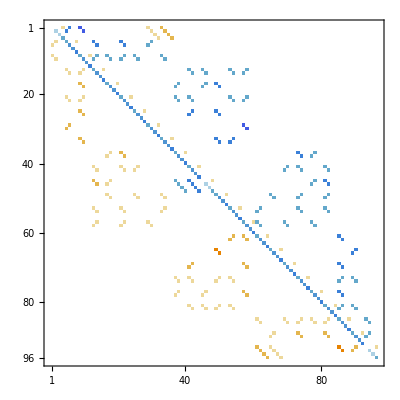

```mathematica
MatrixPlot[Transpose[Transpose[MFinal2][[2 ;; All]] +  1 Transpose[MFinalDOS][[2 ;; All]]]+ 1 B]
```

```mathematica
{Mf[[2]],Mf[[23]]}//MatrixForm
```

(H | gray0 | gray1 | gray2 | gray3 | αpink0 | αpink1 | αpink2 | αpink3 | βpink0 | βpink1 | βpink2 | βpink3 | αred0 | αred1 | αred2 | αred3 | βred0 | βred1 | βred2 | βred3 | αorange0 | αorange1 | αorange2 | αorange3 | βorange0 | βorange1 | βorange2 | βorange3 | αyellow0 | αyellow1 | αyellow2 | αyellow3 | βyellow0 | βyellow1 | βyellow2 | βyellow3 | αyellow green0 | αyellow green1 | αyellow green2 | αyellow green3 | βyellow green0 | βyellow green1 | βyellow green2 | βyellow green3 | navy green0 | navy green1 | navy green2 | navy green3 | αgreen0 | αgreen1 | αgreen2 | αgreen3 | βgreen0 | βgreen1 | βgreen2 | βgreen3 | γgreen0 | γgreen1 | γgreen2 | γgreen3 | αaqua0 | αaqua1 | αaqua2 | αaqua3 | βaqua0 | βaqua1 | βaqua2 | βaqua3 | αsky0 | αsky1 | αsky2 | αsky3 | βsky0 | βsky1 | βsky2 | βsky3 | αblue0 | αblue1 | αblue2 | αblue3 | βblue0 | βblue1 | βblue2 | βblue3 | αpurple0 | αpurple1 | αpurple2 | αpurple3 | βpurple0 | βpurple1 | βpurple2 | βpurple3 | lilac0 | lilac1 | lilac2 | lilac3
αorange0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Dimensions[Transpose[Transpose[MFinal2][[2 ;; All]] +  1 Transpose[MFinalDOS][[2 ;; All]]]+ 1 B]
```

{96,96}

```mathematica
Dimensions[Transpose[MFinal2][[2 ;; All]]]
```

{96,96}

```mathematica
NullSpace[Transpose[MFinal2][[2 ;; All]]]//MatrixForm
```

(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
IncReMatr=Abs[Re[Sign[Transpose[Transpose[MFinal2][[2 ;; All]] +  1 Transpose[MFinalDOS][[2 ;; All]]]+ 1 B]]];
IncImMatr=Im[Sign[Transpose[Transpose[MFinal2][[2 ;; All]] +  1 Transpose[MFinalDOS][[2 ;; All]]]+ 1 B]];
```

```mathematica
Abs[IncReMatr+IncImMatr];
```

## Graph from Oreshkov

```mathematica
MOresh[R]//MatrixForm
```

(0 | -6 | 0 | 0 | 3 R | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -R | -2 | -2 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | -R | 0 | 0 | -1 | -1 | -2 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | -R | 0 | -2 | 0 | -2 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | -R | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 2 | 0 | -R | 0 | 0 | 0 | -2 | -1 | 0 | 0
0 | 0 | 3 | 0 | 0 | -3 R | 0 | 0 | 0 | 0 | -3 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0 | -R | -1 | -1 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | -R | 0 | 0 | -2 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | -R | 0 | -2 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 2 | 0 | 0 | -R | -2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 2 | -R | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 R | 0 | 0 | 6 | 0)

{{0,1,0,0,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,0,0,0,0,0,0,0,0},{0,1,1,0,0,1,1,1,0,0,0,0,0},{0,1,0,1,0,1,0,1,0,0,0,0,0},{0,1,0,0,1,0,0,1,0,0,0,0,0},{0,0,1,1,0,1,0,0,0,1,1,0,0},{0,0,1,0,0,1,0,0,0,0,1,0,0},{0,0,1,1,1,0,0,1,1,1,1,0,0},{0,0,0,0,0,0,0,1,1,0,0,1,0},{0,0,0,0,0,1,0,1,0,1,0,1,0},{0,0,0,0,0,1,1,1,0,0,1,1,0},{0,0,0,0,0,0,0,0,1,1,1,1,1},{0,0,0,0,0,0,0,0,1,0,0,1,0}}

{{0,0,0,0,1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1,0,0,0,0}}

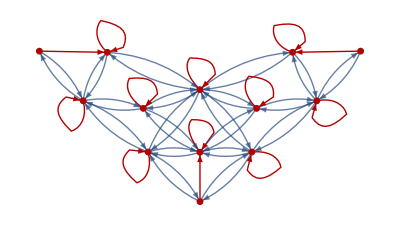

```mathematica
OreshDecohe=Abs[Re[Sign[ MOresh[1]]]]
OreshCorre=Abs[Sign[(MOresh[1]-MOresh[0])]]
HighlightGraph[AdjacencyGraph[OreshDecohe],{AdjacencyGraph[OreshCorre]}]
```

```mathematica
________________
```

```mathematica
Table[Sign[MOresh[1]][[i,j]],{i,1,13},{j,1,13}]
```

{{0,-1,0,0,1,0,0,0,0,0,0,0,0},{1,-1,-1,-1,-1,0,0,0,0,0,0,0,0},{0,1,-1,0,0,-1,-1,-1,0,0,0,0,0},{0,1,0,-1,0,-1,0,-1,0,0,0,0,0},{0,1,0,0,-1,0,0,-1,0,0,0,0,0},{0,0,1,1,0,-1,0,0,0,-1,-1,0,0},{0,0,1,0,0,-1,0,0,0,0,-1,0,0},{0,0,1,1,1,0,0,-1,-1,-1,-1,0,0},{0,0,0,0,0,0,0,1,-1,0,0,-1,0},{0,0,0,0,0,1,0,1,0,-1,0,-1,0},{0,0,0,0,0,1,1,1,0,0,-1,-1,0},{0,0,0,0,0,0,0,0,1,1,1,-1,-1},{0,0,0,0,0,0,0,0,1,0,0,1,0}}

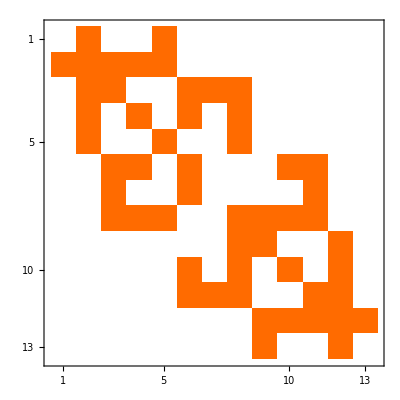

```mathematica
MatrixPlot[{{0,1,0,0,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,0,0,0,0,0,0,0,0},{0,1,1,0,0,1,1,1,0,0,0,0,0},{0,1,0,1,0,1,0,1,0,0,0,0,0},{0,1,0,0,1,0,0,1,0,0,0,0,0},{0,0,1,1,0,1,0,0,0,1,1,0,0},{0,0,1,0,0,1,0,0,0,0,1,0,0},{0,0,1,1,1,0,0,1,1,1,1,0,0},{0,0,0,0,0,0,0,1,1,0,0,1,0},{0,0,0,0,0,1,0,1,0,1,0,1,0},{0,0,0,0,0,1,1,1,0,0,1,1,0},{0,0,0,0,0,0,0,0,1,1,1,1,1},{0,0,0,0,0,0,0,0,1,0,0,1,0}}]
```

```mathematica
_____________________________
```

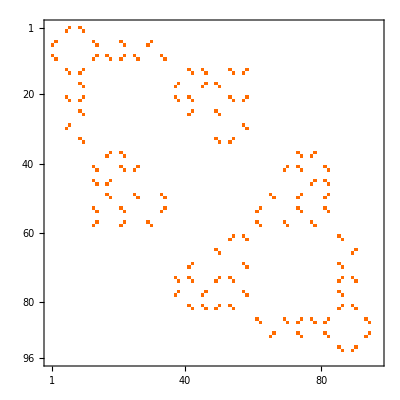

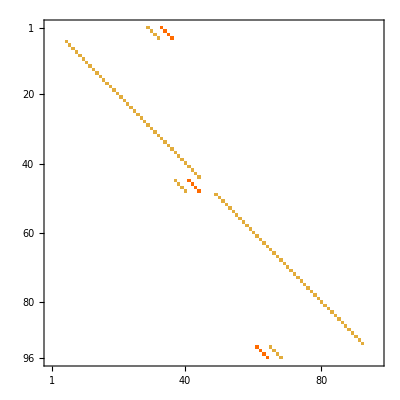

```mathematica
MatrixPlot[ReDecoherenceMat]
MatrixPlot[CorrectionMat]
```

## Graph for our case

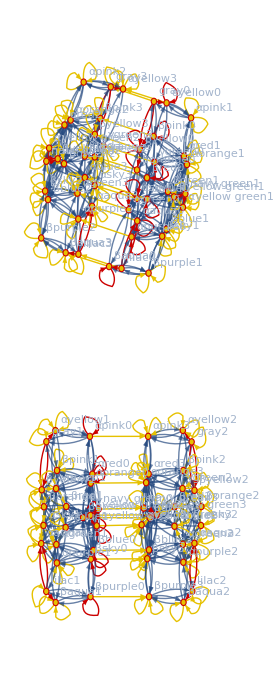

```mathematica
ReDecoherenceMat=Abs[Re[Sign[Transpose[Transpose[MFinal2][[2 ;; All]] ]]]];
ImDecoherenceMat=Abs[Im[Sign[Transpose[Transpose[MFinal2][[2 ;; All]] ]]]];
ReCoolMat=Abs[Re[Sign[Transpose[Transpose[MFinalDOS][[2 ;; All]] ]]]];
ImCoolMat=Abs[Im[Sign[Transpose[Transpose[MFinalDOS][[2 ;; All]] ]]]];
CorrectionMat=Abs[Re[B]];
(*IncImMatr=Abs[Im[Sign[Transpose[Transpose[MFinal2][[2 ;; All]] +  0Transpose[MFinalDOS][[2 ;; All]]]+ 0 B]]];
GG=AdjacencyGraph[ReDecoherenceMat+ CorrectionMat,VertexLabels->Table[i->colorlist[[i]],{i,96}],DirectedEdges->False,GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Left}]*)AdjacencyGraph[ReDecoherenceMat+ImDecoherenceMat+CorrectionMat,GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Left}];

HighlightGraph[AdjacencyGraph[ReDecoherenceMat+ImDecoherenceMat+ReCoolMat+ImCoolMat+CorrectionMat,VertexLabels->Table[i->colorlist[[i]],{i,96}]],{AdjacencyGraph[CorrectionMat],AdjacencyGraph[ReCoolMat+ImCoolMat]}]
```

```mathematica
colorlist
```

{gray0,gray1,gray2,gray3,αpink0,αpink1,αpink2,αpink3,βpink0,βpink1,βpink2,βpink3,αred0,αred1,αred2,αred3,βred0,βred1,βred2,βred3,αorange0,αorange1,αorange2,αorange3,βorange0,βorange1,βorange2,βorange3,αyellow0,αyellow1,αyellow2,αyellow3,βyellow0,βyellow1,βyellow2,βyellow3,αyellow green0,αyellow green1,αyellow green2,αyellow green3,βyellow green0,βyellow green1,βyellow green2,βyellow green3,navy green0,navy green1,navy green2,navy green3,αgreen0,αgreen1,αgreen2,αgreen3,βgreen0,βgreen1,βgreen2,βgreen3,γgreen0,γgreen1,γgreen2,γgreen3,αaqua0,αaqua1,αaqua2,αaqua3,βaqua0,βaqua1,βaqua2,βaqua3,αsky0,αsky1,αsky2,αsky3,βsky0,βsky1,βsky2,βsky3,αblue0,αblue1,αblue2,αblue3,βblue0,βblue1,βblue2,βblue3,αpurple0,αpurple1,αpurple2,αpurple3,βpurple0,βpurple1,βpurple2,βpurple3,lilac0,lilac1,lilac2,lilac3}

```mathematica
codewordcolor={"000000,0","000000,1","000000,2","000000,3","100000,0","100000,1","100000,2","010000,3","010000,0","010000,1","010000,2","010000,3","110000,0","110000,1","110000,2","110000,3","011000,0","011000,1","011000,2","011000,3","100010,0","100010,1","100010,2","100010,3","001010,0","001010,1","001010,2","001010,3","100100,0","100100,1","100100,2","100100,3","010010,0","010010,1","010010,2","010010,3","100011,0","100011,1","100011,2","100011,3","010101,0","010101,1","010101,2","010101,3","111000,0","111000,1","111000,2","111000,3","011001,0","011001,1","011001,2","011001,3","101001,0","101001,1","101001,2","101001,3","101100,0","101100,1","101100,2","101100,3","101101,0","101101,1","101101,2","101101,3","011011,0","011011,1","011011,2","011011,3","101110,0","101110,1","101110,2","101110,3","011110,0","011110,1","011110,2","011110,3","100111,0","100111,1","100111,2","100111,3","111001,0","111001,1","111001,2","111001,3","111110,0","111110,1","111110,2","111110,3","011111,0","011111,1","011111,2","011111,3","111111,0","111111,1","111111,2","111111,3"};
codewordcolor[[96]];
colorlist[[96]];
```

```mathematica
(*For[i=0,i<2^6,i++,For[j=0,j<4,j++,Print[{Append[IntegerDigits[i,2,6],j],colorfold[Append[IntegerDigits[i,2,6],j]]}]]]*)
For[i=0,i<2^6,i++,For[j=0,j<4,j++,If[colorfold[Append[IntegerDigits[i,2,6],j]]=="lilac"<>ToString[j],Print[{colorfold[Append[IntegerDigits[i,2,6],j]],Append[IntegerDigits[i,2,6],j]}]]]
]
```

{lilac0,{1,1,1,1,1,1,0}}

{lilac1,{1,1,1,1,1,1,1}}

{lilac2,{1,1,1,1,1,1,2}}

{lilac3,{1,1,1,1,1,1,3}}

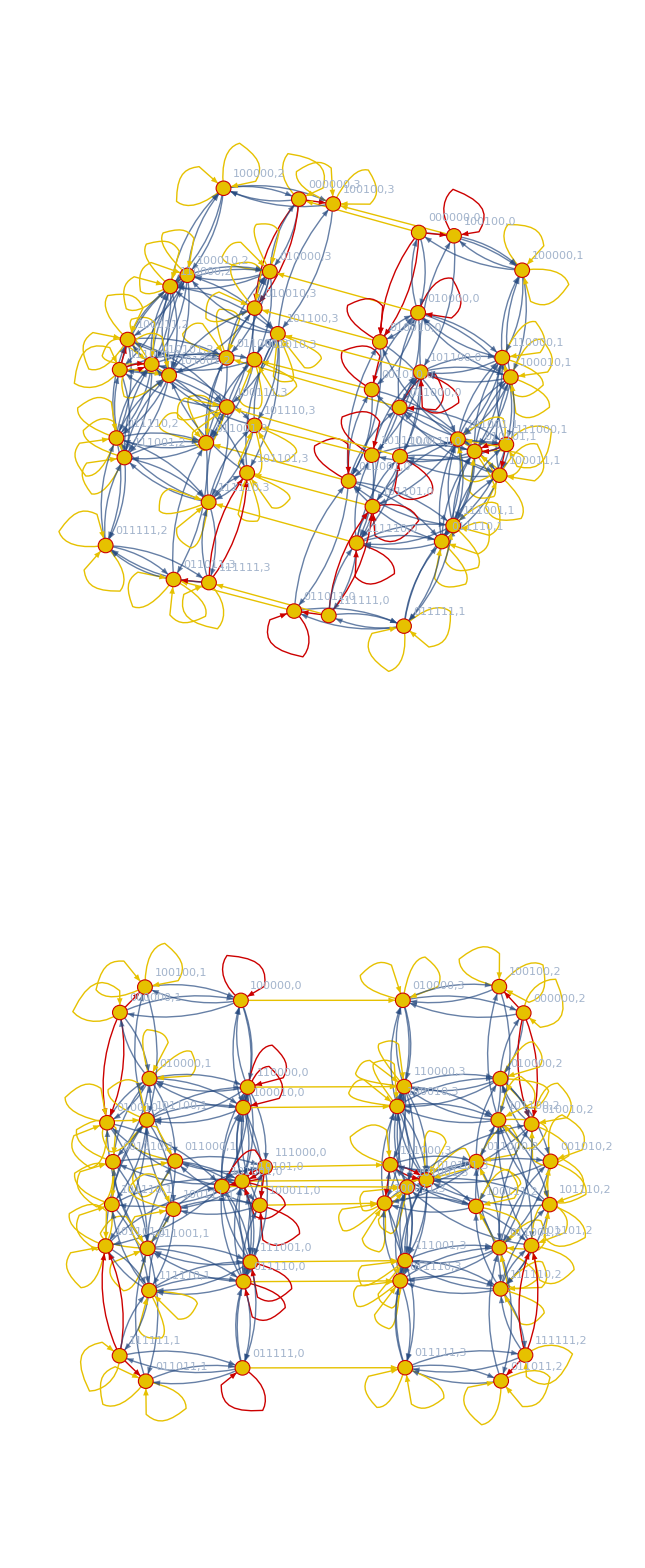

```mathematica
ReDecoherenceMat=Abs[Re[Sign[Transpose[Transpose[MFinal2][[2 ;; All]] ]]]];
ImDecoherenceMat=Abs[Im[Sign[Transpose[Transpose[MFinal2][[2 ;; All]] ]]]];
ReCoolMat=Abs[Re[Sign[Transpose[Transpose[MFinalDOS][[2 ;; All]] ]]]];
ImCoolMat=Abs[Im[Sign[Transpose[Transpose[MFinalDOS][[2 ;; All]] ]]]];
CorrectionMat=Abs[Re[B]];
(*IncImMatr=Abs[Im[Sign[Transpose[Transpose[MFinal2][[2 ;; All]] +  0Transpose[MFinalDOS][[2 ;; All]]]+ 0 B]]];
GG=AdjacencyGraph[ReDecoherenceMat+ CorrectionMat,VertexLabels->Table[i->colorlist[[i]],{i,96}],DirectedEdges->False,GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Left}]*)AdjacencyGraph[ReDecoherenceMat+ImDecoherenceMat+CorrectionMat,GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Left}];

HighlightGraph[AdjacencyGraph[ReDecoherenceMat+ImDecoherenceMat+ReCoolMat+ImCoolMat+CorrectionMat,VertexLabels->Table[i->codewordcolor[[i]],{i,96}]],{AdjacencyGraph[CorrectionMat],AdjacencyGraph[ReCoolMat+ImCoolMat]}]
```

```mathematica
___________________________
```

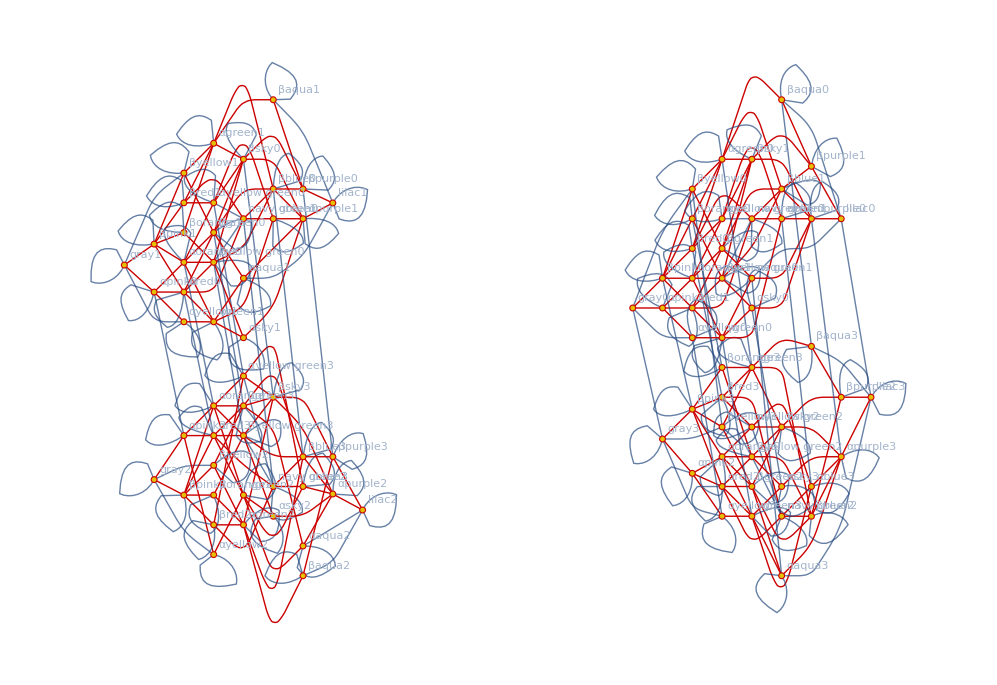

```mathematica
ReDecoherenceMat=Abs[Re[Sign[Transpose[Transpose[MFinal2][[2 ;; All]] ]]]];
ImDecoherenceMat=Abs[Im[Sign[Transpose[Transpose[MFinal2][[2 ;; All]] ]]]];
ReCoolMat=Abs[Re[Sign[Transpose[Transpose[MFinalDOS][[2 ;; All]] ]]]];
ImCoolMat=Abs[Im[Sign[Transpose[Transpose[MFinalDOS][[2 ;; All]] ]]]];
CorrectionMat=Abs[Re[B]];
(*IncImMatr=Abs[Im[Sign[Transpose[Transpose[MFinal2][[2 ;; All]] +  0Transpose[MFinalDOS][[2 ;; All]]]+ 0 B]]];*)
GG=AdjacencyGraph[ReDecoherenceMat+ ImDecoherenceMat+ReCoolMat+ImCoolMat+CorrectionMat,VertexLabels->Table[i->colorlist[[i]],{i,96}],DirectedEdges->False,GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Left}];
HighlightGraph[GG,{AdjacencyGraph[ReDecoherenceMat+ImDecoherenceMat],AdjacencyGraph[ReCoolMat]}]
```

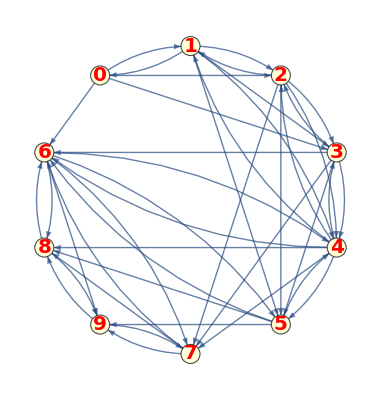
-Graphics--Graphics-

```mathematica
blocks={{0,1,2,3},{0,1,4,5},{0,2,4,6},{0,3,7,8},{0,5,7,9},{0,6,8,9},{1,2,7,8},{1,3,6,9},{1,4,7,9},{1,5,6,8},{2,3,5,9},{2,4,8,9},{2,5,6,7},{3,4,5,8},{3,4,6,7}};
edglst={0->1,1->2,2->3,0->1,1->4,4->5,0->2,2->4,4->6,0->3,3->7,7->9,0->6,6->8,8->9,1->2,2->7,7->8,1->3,3->6,6->9,1->4,4->7,7->9,1->5,5->6,6->8,2->3,3->5,5->9,2->4,4->8,8->9,2->5,5->6,6->7,3->4,4->5,5->8,3->4,4->6,6->7};
edglst2=Join@@(Tally[edglst]/. {Rule[a_,b_],2}:>{Rule[a,b],Rule[b,a]}/. {x_Rule,1}:>{x});
vopts={VertexStyle->LightYellow,VertexSize->0.20,VertexLabels->Placed["Name",{1/2,1/2}],VertexLabelStyle->Directive[20,Red,Bold,Italic]};

gg=Graph[edglst2,vopts,GraphLayout->"CircularEmbedding",VertexLabels->"Name"];
gg2=HighlightGraph[gg,(EdgeList[Subgraph[gg,#]]&/@blocks)];
Row[{gg,gg2}]
```